# Gaining a better understanding of how to use Mathematica for physics

Peter Cullen Burbery

I have decided I am going to gain a better understanding of how to use Mathematica for physics and dimensional analysis. I started solving some problems from the American Association of Physics Teacher 2011 F=ma exam and I realized that I'm not taking full advantage of the functionality in Mathematica so  I decided to create a new essay where I work on just using Mathematica and working through the documentation.

## Plan

I will be working through the Units&Quantities guide.

I will be using the SI as defined in the BIPM's SI brochure which came into effect on 20 May 2019 after the CGPM voted to redefine the SI in terms of physical constants in 2018 at the Palace of Versailles.

I will also be using the copy of the SI Brochure published by NIST.

I will also not be using the prefixes that are not powers of 10. There are four of them but I'm not going to mention them being I'm trying to phase them out.

I will also be using the proposed prefixes ronna, ronto, quecto and quetta that the CGPM will vote on in November. Hopefully they add ronna for 27, quetta for 30, ronto for -27 and quecto for -30.

I would also like to mention that time is not completely redefined. Time will be probably be redefined in 2035. The other six defining constants are set in stone.

## Unit and Quantity Input

## Quantity

I will work through the properties and relations section for Quantity.

```mathematica
Quantity[1,"Webers"]
```

1 Wb

```mathematica
Quantity[1.7,"Henries""Webers"/"Teslas"]
```

1.7 H Wb/T

```mathematica
Quantity[1.7,"Siemens"("Becquerels")^2/("Katals")^3]
```

1.7 Bq^2 S/kat^3

I can define an IndependentUnit:

```mathematica
Quantity[7,IndependentUnit["donuts"]]
```

7 donuts

I'm thinking of the topology of donuts and coffee cups where a donut is the same as a coffee cup as well as a torus:

```mathematica
Quantity[7,IndependentUnit["donuts"]IndependentUnit["coffeecups"]/IndependentUnit["toruses"]^2]
```

7 coffeecups donuts/toruses^2

Add prefixes:

```mathematica
Quantity[1.7,"Ronnameters"]
```

1.7 Rm

```mathematica
Quantity[3.9,"Rontokelvins"]
```

3.9 r K

```mathematica
Quantity[3.9,"Rontowebers"]
```

3.9 r Wb

I wonder if I can combine an SI prefix with a non SI unit that is accepted for use with the SI?

```mathematica
Quantity[3.9,"Yottaminute"]
```

3.9 Y min

Yes I can. That's cool.

In its one argument form Quantity automatically sets the magnitude to 1:

```mathematica
Quantity["Sieverts"]
```

1 Sv

```mathematica
Quantity["Grays"]
```

1 Gy

Quantity will accept Quantity arguments:

```mathematica
Quantity[Quantity["Farads"],("Seconds")^-1]
```

1 F/s

```mathematica
Quantity[Quantity["Henries"],IndependentUnit["oranges"]]
```

1 H oranges

```mathematica
Quantity[Quantity["Henries"],IndependentUnit["apples"]]
```

1 H apples

Addition of Quantity objects will use heuristics:

```mathematica
qb=Quantity[1,"Teslas"];
qc=Quantity[100,"Gauss"];
CompatibleUnitQ[qb,qc]
```

True

```mathematica
qb+qc
```

10100 G

Products also use heuristics:

```mathematica
qd=Quantity[1,"Kilometers"];
qf=Quantity[3000,"Meters"];
CompatibleUnitQ[qd,qf]
```

True

```mathematica
qd*qf
```

3 km^2

Quantity threads over lists:

```mathematica
Quantity[{1,2,3,{4,5,{6}}},"Hertz"]
```

{1 Hz,2 Hz,3 Hz,{4 Hz,5 Hz,{6 Hz}}}

I noticed that QuantityArraypaclet:ref/QuantityArray[mags,units] would correspond to Quantitypaclet:ref/Quantity[mags,Threaded[units]] if Quantitypaclet:ref/Quantity had the Listablepaclet:ref/Listable attribute, and I think this change should be made where Quantity has the attribute Listable.

Canonical unit strings are always plural. Unit descriptions will accurately reflect the singular form of a unit:

```mathematica
Quantity[1,"Webers"]
```

1 Wb

```mathematica
%//InputForm
```

Quantity[1, "Webers"]

```mathematica
Quantity[1,"Webers"]//ToString
```

1 weber

Since Quantitypaclet:ref/Quantity is HoldRestpaclet:ref/HoldRest, it can accept multiple unit strings of the same dimension:

```mathematica
Quantity[3.5,"Yottameters"/"Ronnameters"]
```

3.5 Ym/Rm

```mathematica
Quantity[12,"Zettagrams"/"Yottagrams"]
```

12 Zg/Yg

When quantities are multiplied, the resulting unit is not automatically simplified:

```mathematica
qg=Quantity[1,"Newtons"];
qh=Quantity[10,"Meters"];
qg*qh
```

10 m N

Use UnitSimplifypaclet:ref/UnitSimplify to get a simpler form of the unit:

```mathematica
UnitSimplify[%]
```

10 J

Use UnitConvertpaclet:ref/UnitConvert to normalize mixed Quantitypaclet:ref/Quantity expressions to non-mixed Quantitypaclet:ref/Quantity expressions:

```mathematica
q=Quantity[MixedMagnitude[Range[24,0,-3]],MixedUnit[{"Yottaseconds","Zettaseconds","Exaseconds","Petaseconds","Teraseconds","Gigaseconds","Megaseconds","Kiloseconds","Seconds"}]]
```

24 Ys21 Zs18 Es15 Ps12 Ts9 Gs6 Ms3 ks0 s yottaseconds,zettaseconds,exaseconds,petaseconds,teraseconds,gigaseconds,megaseconds,kiloseconds,seconds

```mathematica
UnitConvert[q]
```

24021018015012009006003000 s

```mathematica
UnitConvert[q,"Minutes"]
```

400350300250200150100050 min

## QuantityArray

A QuantityArraypaclet:ref/QuantityArray object is interpreted as an array of Quantitypaclet:ref/Quantity objects:

```mathematica
qJ=QuantityArray[RandomReal[1,{20,2}],{"Meters","Seconds"}]
```

QuantityArray[…]

It is an array:

```mathematica
ArrayQ[qJ]
```

True

It is a list of pairs; hence, a matrix, not a vector:

```mathematica
MatrixQ[qJ]
```

True

```mathematica
VectorQ[qJ]
```

False

It is an array of Quantitypaclet:ref/Quantity objects, not an array of numbers:

```mathematica
MatrixQ[qJ,QuantityQ]
```

True

```mathematica
MatrixQ[qJ,NumericQ]
```

False

The QuantityArraypaclet:ref/QuantityArray representation is memory efficient:

```mathematica
qK=QuantityArray[RandomReal[1,{100,100,2}],{"Meters","Seconds"}]
```

QuantityArray[…]

```mathematica
nqK=Normal[qa,QuantityArray];
```

It uses only 6% of the memory of the corresponding normal representation:

```mathematica
ByteCount[qK]/ByteCount[nqK]//N
```

ComplexInfinity

It also allows faster extraction of magnitudes and units:

```mathematica
QuantityMagnitude[qK];//AbsoluteTiming
```

{0.0001504,Null}

```mathematica
QuantityUnit[qJ];//AbsoluteTiming
```

{0.0001899,Null}

Compare to the slower extraction from the normal array of quantities:

```mathematica
QuantityMagnitude[nqK];//AbsoluteTiming
```

{0.0000192,Null}

```mathematica
QuantityUnit[nqK];//AbsoluteTiming
```

{0.0000208,Null}

A single quantity is automatically converted into a Quantitypaclet:ref/Quantity object:

```mathematica
QuantityArray[7,"Meters"]
```

7 m

```mathematica
%//InputForm
```

Quantity[7, "Meters"]

This is a list with one quantity:

```mathematica
QuantityArray[{7},"Meters"]
```

QuantityArray[…]

```mathematica
%//Normal
```

{7 m}

It can also be given as:

```mathematica
QuantityArray[{7},{"Meters"}]
```

QuantityArray[…]

```mathematica
%//Normal
```

{7 m}

During conversion, QuantityArraypaclet:ref/QuantityArray does not try to change units:

```mathematica
QuantityArray[{Quantity[1,"Meters"],Quantity[2,"Zettameters"]}]
```

QuantityArray[…]

UnitConvertpaclet:ref/UnitConvert will unify the units:

```mathematica
UnitConvert[%,"Meters"]
```

QuantityArray[…]

```mathematica
Normal[%]
```

{1 m,2000000000000000000000 m}

The QuantityArraypaclet:ref/QuantityArray structure is preserved in multiple operations. Take two arrays:

```mathematica
qL=QuantityArray[{{1,20},{3,40},{5,60},{7,50}},{"Meters","Seconds"}]
```

QuantityArray[…]

```mathematica
qM=QuantityArray[{{10,2},{20,2},{30,2},{40,2}},{"Zettameters","Zettaseconds"}]
```

QuantityArray[…]

Addition of QuantityArraypaclet:ref/QuantityArray objects of compatible units, automatically converting some of them:

```mathematica
qL+qM
```

QuantityArray[…]

Multiplication of QuantityArraypaclet:ref/QuantityArray objects of compatible dimensions:

```mathematica
qL qM
```

QuantityArray[…]

Tensor product of QuantityArraypaclet:ref/QuantityArray objects:

```mathematica
TensorProduct[qL,qM]
```

QuantityArray[…]

Transposition is special because it stores the permutation:

```mathematica
Transpose[qL]
```

QuantityArray[…]

```mathematica
%//InputForm
```

QuantityArray[StructuredArray`StructuredData[{2, 4}, 
  {{{1, 20}, {3, 40}, {5, 60}, {7, 50}}, 
   {"Meters", "Seconds"}, {{2}, {1}}}]]

Flattening is also special in that sense:

```mathematica
Flatten[qL]
```

QuantityArray[…]

```mathematica
%//InputForm
```

QuantityArray[StructuredArray`StructuredData[{8}, 
  {{{1, 20}, {3, 40}, {5, 60}, {7, 50}}, 
   {"Meters", "Seconds"}, {{1, 2}}}]]

Partition the array:

```mathematica
Partition[qL,2]
```

QuantityArray[…]

```mathematica
%//InputForm
```

QuantityArray[StructuredArray`StructuredData[{2, 2, 2}, 
  {{{{1, 20}, {3, 40}}, {{5, 60}, {7, 50}}}, 
   {"Meters", "Seconds"}, {{1}, {2}, {3}}}]]

Flatten it again:

```mathematica
Flatten[%%,1]
```

QuantityArray[…]

The result is an equivalent representation of the original quantity array:

```mathematica
%==qL
```

True

Take a QuantityArraypaclet:ref/QuantityArray object with compatible but different units:

```mathematica
qN=QuantityArray[{{1,2},{3,4},{5,6}},{"Meters","Yottameters"}]
```

QuantityArray[…]

CommonUnitspaclet:ref/CommonUnits will convert it into a single unit array:

```mathematica
CommonUnits[qN]
```

QuantityArray[…]

```mathematica
Normal[%]
```

{{1 m,2000000000000000000000000 m},{3 m,4000000000000000000000000 m},{5 m,6000000000000000000000000 m}}

To select the unit, use UnitConvertpaclet:ref/UnitConvert:

```mathematica
UnitConvert[qN,"Meters"]
```

QuantityArray[…]

```mathematica
Normal[%]
```

{{1 m,2000000000000000000000000 m},{3 m,4000000000000000000000000 m},{5 m,6000000000000000000000000 m}}

A QuantityArraypaclet:ref/QuantityArray object of infinite precision:

```mathematica
qP=QuantityArray[{{1,2},{3,4}},{"Meters","Seconds"}]
```

QuantityArray[…]

```mathematica
Precision[qP]
```

∞

Numericize to precision 20:

```mathematica
nqP=N[qP,20]
```

QuantityArray[…]

```mathematica
Precision[nqP]
```

20.

```mathematica
InputForm[nqP]
```

QuantityArray[StructuredArray`StructuredData[{2, 2}, 
  {{{1.`20., 2.`20.}, {3.`20., 4.`20.}}, 
   {"Meters", "Seconds"}, {{1}, {2}}}]]

The arithmetic operations take precision into account:

```mathematica
Precision[2. qP]
```

MachinePrecision

QuantityArraypaclet:ref/QuantityArray will automatically attempt to interpret an unknown unit string:

```mathematica
QuantityArray[RandomReal[1,10],"m"]
```

QuantityArray[…]

```mathematica
QuantityArray[{{1,20},{3,40},{5,60},{7,50}},{"m s^-1","V/A"}]
```

Possible Issues

Normalization of QuantityArraypaclet:ref/QuantityArray objects also normalizes purely numerical quantities such as percents:

```mathematica
qQ=QuantityArray[{10,30,79},"Percent"]
```

QuantityArray[…]

```mathematica
Normal[qQ]
```

{1/10,3/10,79/100}

Specify that only the QuantityArraypaclet:ref/QuantityArray structure should be normalized:

```mathematica
Normal[qQ,QuantityArray]
```

{10 %,30 %,79 %}

In details it mentions SparseArray is supported.

```mathematica
SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]]
```

SparseArray[…]

```mathematica
QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]
```

QuantityArray[…]

```mathematica
ByteCount[QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]]
```

25632

Find the determinant:

```mathematica
Det[QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]]
```

678629608419755514953266004896957820972161078160377361970324401521111792080121479864721936071815069425907219215791646774510151130705671056416094404541167439287735488353736963531288441938981088407654256240451529081607242659988552012480001287133802278572298314458227654950008738955663072953766341488209509227159933381319371567666804963833249523370831655778314080604712246344649628072459805028063160913071005795183295590443375991860551286230065601580359306757988823124262933259305966372664091680948986620887898883461227980556352852601733860114246410887151983493540958775872577571329277597701163671587052591794386970584444752423596023268793021595936555282977008138833858707329536639661377014042325817639809356799596347944462538427778375525904007169834445567450156949173690701738594584875536885957881452438269676946038980597530032671949818526703398270502591574889228837327819994695664173214894557366363343168494592437205324652573516528943874382178600874878024643322031797588414862315122048846223291257900756812820806739795819803783834366449110996030165071920678407750230118672657378102915524688059208755108467225277065866103666795739208709483959119145497860116133180335757702319385020561042517429031288526721801002679092058170909635701703382390753126302005323612316630558515594616479515096004453718500060291836932140612551722161051067379805065002788004096547708243964735215852734827632098700684466036892770059458754742495711074949314613079781545359495019757827538184361308856825999513366660884541936335491466045305322353749545362962683762333460252556042583248154845846566948014188971651057314058851019340282646752239847232045463969939303431371658607220786663205842510175297602195433569758123945251755043878718459161595137019904240640962465899496512410906852088532419874383895656303779315512987369934711061777117329635461569528504994783413643047392160871963795694958724055597996525917454740621526108635321204763824742430011606570436994644169759611263012712375861911682673548369764923418748711813157811279361700331599397588282864147719911156923709896847720603482450047076226728760035577410722701184878333100234780537897462936378382079055966277885316116887834607362114802378706815302650083359076798475953780285866955566883261644281750278358349579977889429105626865087038835977930842352223971442123281019745568694318200865586150762549114357677130353514342849892002965601064686292493671204318349298134598116662388818407027989992498970986262856712232401426575229549744739851333516937170071337085705197690437625282926914858257689908846227286051735284322402597283976180484905838486513162987381659809287870592690902387482033879184700359561190209417618607868793293476867624464497838299321267571049753373623085351455438610076341961842557148160442782839736179329056237366708383637405663196770746783100179128651460773512143616414356080816160456447832856222804164147618891013658880373227849181446498052320436905124576367614898030410445386643656246089772967461562154147355201124738052009172637452710027640262529821855681129322547617443299372089380860873141895162966481252930360380537684913059090577224188204179681342669502124011214018434733385892140553307905100266308832521127607403573729242486985024795253305646999864066282626291530104297235324933472771821035277094700384260778312268190937365143307612108901729316774669077441981239149913617114331308200242717771235228048768133852203532299832810943137983635951570 m^1000

Retrieve the timing:

```mathematica
Det[QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]]//RepeatedTiming
```

{0.851515,678629608419755514953266004896957820972161078160377361970324401521111792080121479864721936071815069425907219215791646774510151130705671056416094404541167439287735488353736963531288441938981088407654256240451529081607242659988552012480001287133802278572298314458227654950008738955663072953766341488209509227159933381319371567666804963833249523370831655778314080604712246344649628072459805028063160913071005795183295590443375991860551286230065601580359306757988823124262933259305966372664091680948986620887898883461227980556352852601733860114246410887151983493540958775872577571329277597701163671587052591794386970584444752423596023268793021595936555282977008138833858707329536639661377014042325817639809356799596347944462538427778375525904007169834445567450156949173690701738594584875536885957881452438269676946038980597530032671949818526703398270502591574889228837327819994695664173214894557366363343168494592437205324652573516528943874382178600874878024643322031797588414862315122048846223291257900756812820806739795819803783834366449110996030165071920678407750230118672657378102915524688059208755108467225277065866103666795739208709483959119145497860116133180335757702319385020561042517429031288526721801002679092058170909635701703382390753126302005323612316630558515594616479515096004453718500060291836932140612551722161051067379805065002788004096547708243964735215852734827632098700684466036892770059458754742495711074949314613079781545359495019757827538184361308856825999513366660884541936335491466045305322353749545362962683762333460252556042583248154845846566948014188971651057314058851019340282646752239847232045463969939303431371658607220786663205842510175297602195433569758123945251755043878718459161595137019904240640962465899496512410906852088532419874383895656303779315512987369934711061777117329635461569528504994783413643047392160871963795694958724055597996525917454740621526108635321204763824742430011606570436994644169759611263012712375861911682673548369764923418748711813157811279361700331599397588282864147719911156923709896847720603482450047076226728760035577410722701184878333100234780537897462936378382079055966277885316116887834607362114802378706815302650083359076798475953780285866955566883261644281750278358349579977889429105626865087038835977930842352223971442123281019745568694318200865586150762549114357677130353514342849892002965601064686292493671204318349298134598116662388818407027989992498970986262856712232401426575229549744739851333516937170071337085705197690437625282926914858257689908846227286051735284322402597283976180484905838486513162987381659809287870592690902387482033879184700359561190209417618607868793293476867624464497838299321267571049753373623085351455438610076341961842557148160442782839736179329056237366708383637405663196770746783100179128651460773512143616414356080816160456447832856222804164147618891013658880373227849181446498052320436905124576367614898030410445386643656246089772967461562154147355201124738052009172637452710027640262529821855681129322547617443299372089380860873141895162966481252930360380537684913059090577224188204179681342669502124011214018434733385892140553307905100266308832521127607403573729242486985024795253305646999864066282626291530104297235324933472771821035277094700384260778312268190937365143307612108901729316774669077441981239149913617114331308200242717771235228048768133852203532299832810943137983635951570 m^1000}

## QuantityDistribution

QuantityDistributionpaclet:ref/QuantityDistribution with dimensionless units will auto-evaluate to the magnitude distribution:

```mathematica
QuantityDistribution[GammaDistribution[2,3],"DimensionlessUnit"]
```

GammaDistribution[2,3]

```mathematica
QuantityDistribution[GammaDistribution[2,3],"Meters"/"Meters"]
```

GammaDistribution[2,3]

Use QuantityMagnitudepaclet:ref/QuantityMagnitude and QuantityUnitpaclet:ref/QuantityUnit to extract distribution and units:

```mathematica
qdist=NormalDistribution[Quantity[120, "Petameters"],Quantity[16, "Petameters"]]
```

QuantityDistribution[NormalDistribution[120,16], Pm]

```mathematica
{QuantityMagnitude[qdist],QuantityUnit[qdist]}
```

{NormalDistribution[120,16],Petameters}

QuantityDistributionpaclet:ref/QuantityDistribution[dist,unit] is equivalent to TransformedDistributionpaclet:ref/TransformedDistribution:

```mathematica
TransformedDistribution[Quantity[x,"Sieverts"],x\[Distributed]NormalDistribution[μ,σ]]
```

QuantityDistribution[NormalDistribution[μ,σ], Sv]

Skewness and kurtosis of a QuantityDistributionpaclet:ref/QuantityDistribution are unitless:

```mathematica
𝒟=QuantityDistribution[GumbelDistribution[20,3],"Watts"];
```

```mathematica
Skewness[𝒟]
```

-(12 √6 Zeta[3])/π^3

```mathematica
Kurtosis[𝒟]
```

27/5

Joint distribution of mass and acceleration:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[{200,9.81},{5,0.01},1/2],{"Grams","Meters"/"Seconds"^2}];
```

The unit of the moment of order (1,1) is the product of units of each component:

```mathematica
Moment[𝒟,{1,1}]
```

1962.03 g m/s^2

The moment can be interpreted as the expected value of force:

```mathematica
UnitSimplify[%]
```

1.96203 N

PDFpaclet:ref/PDF of a continuous distribution with units integrates to 1 over its domain:

```mathematica
𝒟=CauchyDistribution[Quantity[120, "Petameters"],Quantity[16, "Petameters"]]
```

QuantityDistribution[CauchyDistribution[120,16], Pm]

```mathematica
pdf=PDF[𝒟,Quantity[x,"Meters"]]
```

1/(16 π (1+1/256 (-120+x/1000000000000000)^2)) /Pm

Reciprocal units of the density function are canceled by the unit of the measure to give unitless antiderivative:

```mathematica
Integrate[pdf,Quantity[x,"Petameters"]]
```

-(1000000000000000 ArcTan[1/16 (120-x/1000000000000000)])/π

Total probability is equal to 1:

```mathematica
Integrate[pdf,{Quantity[x,"Meters"],Quantity[-∞, "Meters"],Quantity[+∞, "Meters"]}]
```

1

This is the start of the section on Possible Issues.

The dimensionality of the distribution and units must agree:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[r],{"Meters","Hertz","Watts"}];
DistributionParameterQ[𝒟]
```

False

Specify two units for two dimensions:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[r],{"Meters","Teslas"}];
Mean[𝒟]
```

{0 m,0 T}

The identical unit for all dimensions:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[r],"Volts"];
Mean[𝒟]
```

{0 V,0 V}

The unit conversion may map the data outside of the support of the distribution:

```mathematica
data=QuantityArray[RandomVariate[MultinomialDistribution[15,{.3,.7}],100],{"Grams","Teragrams"}];
```

Estimate a quantity distribution in kilograms:

```mathematica
EstimatedDistribution[data,QuantityDistribution[MultinomialDistribution[n,{p,q}],"Kilograms"]]
```

EstimatedDistribution[QuantityArray[…],QuantityDistribution[MultinomialDistribution[n,{p,q}], kg]]

Estimate using the units of the data:

```mathematica
EstimatedDistribution[data,MultinomialDistribution[n,{p,q}]]
```

QuantityDistribution[MultinomialDistribution[15,{0.301333,0.698667}],{ g, Tg}]

Then convert the distribution:

```mathematica
UnitConvert[%,"Kilograms"]
```

QuantityDistribution[TransformedDistribution[{x1/1000,1000000000 x2},{x1,x2}\[Distributed]MultinomialDistribution[15,{0.301333,0.698667}]], kg]

Setting fixed values for parameter estimation is unit dependent:

```mathematica
data=QuantityArray[RandomReal[{-1,1},10^2],"DegreesCelsius"]
```

QuantityArray[…]

```mathematica
distC=EstimatedDistribution[data,NormalDistribution[0,s]]
```

QuantityDistribution[NormalDistribution[0,0.54868], °C]

```mathematica
distK=EstimatedDistribution[UnitConvert[data,"DegreesKelvin"],NormalDistribution[0,s]]
```

QuantityDistribution[NormalDistribution[0,273.067], K]

Compare standard deviations:

```mathematica
{StandardDeviation[distC],UnitConvert[StandardDeviation[distK],"DegreesCelsius"]}
```

{0.54868 °C,-0.0831211 °C}

This is caused by:

```mathematica
{QuantityMagnitude[Quantity[0,"DegreesCelsius"]],QuantityMagnitude[Quantity[0,"DegreesFahrenheit"],"DegreesCelsius"]}
```

{0,-160/9}

Convert the whole quantity distribution instead:

```mathematica
UnitConvert[distK,"DegreesCelsius"]
```

QuantityDistribution[NormalDistribution[-5463/20,273.067], °C]

Use converted units in call to estimation:

```mathematica
distK2=EstimatedDistribution[UnitConvert[data,"DegreesKelvin"],NormalDistribution[QuantityMagnitude[Quantity[0,"DegreesKelvin"],"DegreesKelvin"],s]]
```

QuantityDistribution[NormalDistribution[0,273.067], K]

```mathematica
UnitConvert[distK2,"DegreesCelsius"]
```

QuantityDistribution[NormalDistribution[-5463/20,273.067], °C]

```mathematica
%==distC
```

QuantityDistribution[NormalDistribution[-5463/20,273.067], °C]==QuantityDistribution[NormalDistribution[0,0.54868], °C]

Hmm this should be True but I changed Fahrenheit to Kelvin so I might have messed something up.

The magnitude of the factorial moment of a QuantityDistributionpaclet:ref/QuantityDistribution coincides with the factorial moment of the magnitude distribution:

```mathematica
𝒟=QuantityDistribution[NormalDistribution[μ,σ],"Meters"]
```

QuantityDistribution[NormalDistribution[μ,σ], m]

```mathematica
FactorialMoment[𝒟,2]
```

(-μ+μ^2+σ^2) m^2

```mathematica
FactorialMoment[NormalDistribution[μ,σ],2]
```

-μ+μ^2+σ^2

Factorial moment expression is not homogeneous in the location and scale parameters, hence direct substitution of quantity parameters results in an error:

```mathematica
%/.{μ->Quantity[μ,"Meters"],σ->Quantity[σ,"Meters"]}
```

-μ m^2+(μ^2+σ^2) m^4

The error is in the message box but doesn't display directly.

## Quantity Components

## QuantityMagnitude

```mathematica
QuantityMagnitude[{Quantity[3.2, "Meters"],Quantity[34, "Kilograms"]}]
```

{3.2,34}

```mathematica
QuantityMagnitude[{{Quantity[40, "Webers"],Quantity[100, "Siemens"]},Quantity[4, "Henries"]}]
```

{{40,100},4}

```mathematica
QuantityMagnitude[{Quantity[1, "Hours"],Quantity[1, "Seconds"]},{"Days","Weeks","Decades"}]
```

{{1/24,1/168,5/438291},{1/86400,1/604800,1/315569520}}

```mathematica
Quantity[MixedMagnitude[{1002,80}],MixedUnit[{"Meters","Kilometers"}]]
```

2 81

```mathematica
QuantityMagnitude[%]
```

MixedMagnitude[{2,81}]

## QuantityUnit

```mathematica
QuantityUnit[Quantity[50, "Megameters"]]
```

Megameters

## UnitDimensions

UnitDimensionspaclet:ref/UnitDimensions returns the base dimension of a unit:

```mathematica
UnitDimensions[Quantity[3,"Spins"]]
```

{{LengthUnit,2},{MassUnit,1},{TimeUnit,-1}}

```mathematica
UnitDimensions[Quantity[7000,"Henries"]]
```

{{ElectricCurrentUnit,-2},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}}

The dimension pairs are returned lexically ordered:

```mathematica
UnitDimensions[Quantity[5,"Meters"*"Seconds"]]
```

{{LengthUnit,1},{TimeUnit,1}}

```mathematica
UnitDimensions[Quantity[5,"Seconds"*"Meters"]]
```

{{LengthUnit,1},{TimeUnit,1}}

UnitDimensionspaclet:ref/UnitDimensions returns the argument of an IndependentUnitpaclet:ref/IndependentUnit specification together with its power:

```mathematica
Quantity[3,"Kilometers"*IndependentUnit["myUnit"]^2]
```

3 km myUnit^2

```mathematica
UnitDimensions[%]
```

{{LengthUnit,1},{IndependentUnitDimension[myUnit],2}}

UnitDimensionspaclet:ref/UnitDimensions returns one dimension pair for a MixedUnitpaclet:ref/MixedUnit specification:

```mathematica
Quantity[MixedMagnitude[{5,10}],MixedUnit[{"Megameters","Meters"}]]
```

5 10

```mathematica
UnitDimensions[%]
```

{{LengthUnit,1}}

UnitDimensionspaclet:ref/UnitDimensions ignores the date in DatedUnitpaclet:ref/DatedUnit specifications:

```mathematica
UnitDimensions[DatedUnit["Meters",1889]]
```

{{LengthUnit,1}}

```mathematica
UnitDimensions[DatedUnit["USDollars",2000]]
```

{{MoneyUnit,1}}

An empty list is returned for units without dimension:

```mathematica
UnitDimensions[Quantity[72,"Percent"]]
```

{}

```mathematica
UnitDimensions[Quantity[98,"Scores"]]
```

{}

A unit given as a prefix only is dimensionless:

```mathematica
UnitDimensions[Quantity[100000,"Gigameters"]]
```

{{LengthUnit,1}}

```mathematica
UnitDimensions[Quantity[100,"Giga"]]
```

{}

UnitDimensionspaclet:ref/UnitDimensions will automatically attempt to interpret an unknown unit string:

```mathematica
KnownUnitQ["OddCandle"]
```

False

```mathematica
(*my example*)UnitDimensions["OddCandle"]
```

Quantity::unkunit: Unable to interpret unit specification OddCandle.

UnitDimensions[OddCandle]

```mathematica
(*my example*) KnownUnitQ["OldCandle"]
```

False

This documentation needs to be updated. The output I copied originally was

```mathematica
(*Documentation example*) UnitDimensions["OddCandle"]
```

{{LuminousIntensityUnit,1}}

```mathematica
(*Documentation example*) KnownUnitQ["OldCandle"]
```

True

This doesn't match the error that OddCandle could not be interpreted above.

UnitDimensionspaclet:ref/UnitDimensions threads over lists:

```mathematica
UnitDimensions[{Quantity[7, "Meters"],Quantity[8, "Bits"],Quantity[5, "Megagrams"]}]
```

{{{LengthUnit,1}},{{InformationUnit,1}},{{MassUnit,1}}}

```mathematica
UnitDimensions[{Quantity[7, "Minutes"],{Quantity[2, "Radians"]},Quantity[5, "Steradians"]}]
```

{{{TimeUnit,1}},{{{AngleUnit,1}}},{{AngleUnit,2}}}

Numerical values are considered dimensionless:

```mathematica
UnitDimensions[Pi]
```

{}

## QuantityQ

QuantityQpaclet:ref/QuantityQ returns Falsepaclet:ref/False for any expression whose head is not Quantitypaclet:ref/Quantity:

```mathematica
QuantityQ[2]
```

False

```mathematica
QuantityQ[x]
```

False

```mathematica
QuantityQ[{Quantity[7, "Weeks"],Quantity[2, "Hours"]}]
```

False

In particular, QuantityArraypaclet:ref/QuantityArray, QuantityVariablepaclet:ref/QuantityVariable, and QuantityDistributionpaclet:ref/QuantityDistribution are not QuantityQpaclet:ref/QuantityQ objects:

```mathematica
QuantityQ[QuantityArray[{2.3,1.5,9.0},"Meters"]]
```

False

```mathematica
QuantityQ[QuantityVariable["V","ElectricPotential"]]
```

False

```mathematica
QuantityQ[QuantityDistribution[NormalDistribution[12,6],Quantity[, "Centimeters"]]]
```

False

QuantityQpaclet:ref/QuantityQ returns Falsepaclet:ref/False for Quantitypaclet:ref/Quantity expressions with invalid arguments:

```mathematica
Quantity[2,x]
```

Quantity[2,x]

```mathematica
QuantityQ[%]
```

False

```mathematica
Quantity[2,Quantity["Meters"]]
```

Quantity[2,1 m]

```mathematica
QuantityQ[%]
```

False

QuantityQpaclet:ref/QuantityQ returns Truepaclet:ref/True only for Quantitypaclet:ref/Quantity expressions with valid arguments:

```mathematica
Quantity[2,"Meters"]
```

2 m

```mathematica
QuantityQ[%]
```

True

```mathematica
Quantity[2,IndependentUnit["myUnit"]^3]
```

2 myUnit^3

```mathematica
QuantityQ[%]
```

True

```mathematica
Quantity[MixedMagnitude[{5,10}],
MixedUnit[{"Meter","Millimeters"}]]
```

5 10

```mathematica
QuantityQ[%]
```

True

## KnownUnitQ

I will now focus on the Scope section instead of the Properties & Relations section.

Units represented by a single string:

```mathematica
KnownUnitQ["Meters"]
```

True

```mathematica
KnownUnitQ["Siemens"]
```

True

Products of known units:

```mathematica
KnownUnitQ["Newtons"*"Meters"]
```

True

```mathematica
KnownUnitQ["Watts"/"Meters"^2]
```

True

KnownUnitQpaclet:ref/KnownUnitQ returns Truepaclet:ref/True for valid IndependentUnitpaclet:ref/IndependentUnit specifications:

```mathematica
KnownUnitQ[IndependentUnit["myUnit"]]
```

True

```mathematica
KnownUnitQ[IndependentUnit["Unit1"]/IndependentUnit["Unit2"]^3]
```

True

It returns Falsepaclet:ref/False for invalid IndependentUnitpaclet:ref/IndependentUnit specifications:

```mathematica
KnownUnitQ[IndependentUnit[1]]
```

False

```mathematica
KnownUnitQ[IndependentUnit[unit]]
```

False

MixedUnitpaclet:ref/MixedUnit specifications of compatible units:

```mathematica
KnownUnitQ[MixedUnit[{"Gigameters","Millimeters"}]]
```

True

Incompatible units do not produce a valid MixedUnitpaclet:ref/MixedUnit specification:

```mathematica
KnownUnitQ[MixedUnit[{"Seconds","Millimeters"}]]
```

False

DatedUnitpaclet:ref/DatedUnit specifications:

```mathematica
KnownUnitQ[DatedUnit["USDollars", 1990]]
```

True

```mathematica
KnownUnitQ[DatedUnit["Euros", Today]]
```

True

Prefixes are dimensionless known units:

```mathematica
KnownUnitQ["Centi"]
```

True

```mathematica
KnownUnitQ["Mega"]
```

True

This function be helpful for making a prefix table where regex would be used to test if a string is a valid unit for example μΩ is a valid symbol for the micro-ohm, but ηρ is not a valid symbol.

Numeric expressions are not canonical units:

```mathematica
KnownUnitQ[1]
```

False

```mathematica
KnownUnitQ[Sqrt[2]]
```

False

## Quantity Display

## QuantityForm

```mathematica
QuantityForm[Quantity[3,"Siemens"/("Meters")^3],"LongForm"]
```

3 siemens per meter cubed

QuantityFormpaclet:ref/QuantityForm acts on all Quantitypaclet:ref/Quantity objects in an expression:

```mathematica
QuantityForm[{Quantity[4, "Joules"],Quantity[9, "Sieverts"],Quantity[3, "Ohms"]},{"Abbreviation","LongForm"}]
```

{4 J(joules),9 Sv(sieverts),3 Ω(ohms)}

```mathematica
QuantityForm[<|"Distance"->Quantity[260, "Miles"],"Duration"->Quantity[3, "Hours"]|>,"LongForm"]
```

<|Distance→260 miles,Duration→3 hours|>

Possible display forms are "Abbreviation" and "LongForm":

```mathematica
expr=Quantity[5,"Grams"/"Meters"^3]
```

5 g/m^3

```mathematica
QuantityForm[expr,"Abbreviation"]
```

5 g/m^3

```mathematica
QuantityForm[expr,"LongForm"]
```

5 grams per meter cubed

"LongForm" descriptions will select singular/plural tenses based on the value of each Quantitypaclet:ref/Quantity:

```mathematica
QuantityForm[Quantity[1,"Seconds"],{"LongForm"}]
```

1 second

```mathematica
QuantityForm[Quantity[.7,"Seconds"],{"LongForm"}]
```

0.7 seconds

"SingularForm" can be used with "LongForm" to force unit descriptions to be in singular tense:

```mathematica
QuantityForm[Quantity[.7,"Seconds"],{"LongForm","SingularForm"}]
```

0.7 second

If the first argument is a canonical unit, QuantityFormpaclet:ref/QuantityForm will print with the specified form of the unit:

```mathematica
QuantityForm["Meters",{"Abbreviation","LongForm"}]
```

m(meters)

QuantityFormpaclet:ref/QuantityForm works with MixedUnitpaclet:ref/MixedUnit specifications:

```mathematica
Quantity[MixedMagnitude[{1,2}],MixedUnit[{"Exameters","Petameters"}]]
```

1 2

```mathematica
QuantityForm[%,{"Abbreviation","LongForm"}]
```

1 Em2 Pm(exameters,petameters)

## TargetUnits

TargetUnitspaclet:ref/TargetUnits can be used to specify which units to use in the visualization:

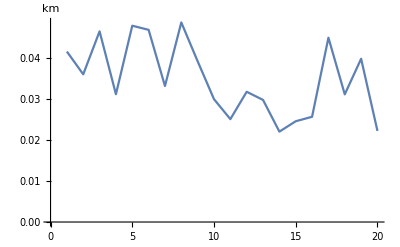

```mathematica
ListLinePlot[Quantity[RandomReal[{20,50},{20}],"Meters"],TargetUnits->"Kilometers",AxesLabel->Automatic]
```

TargetUnitspaclet:ref/TargetUnits can also be used to specify units for purely numerical data:

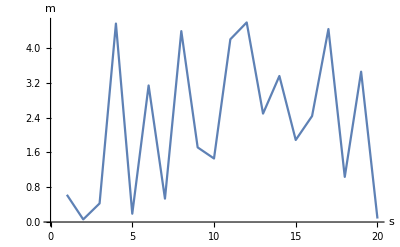

```mathematica
ListLinePlot[RandomReal[{0,5},{20}],TargetUnits->{"Seconds","Meters"},AxesLabel->Automatic]
```

## Unit Conversion

First I can set the unit system to metric.

```mathematica
$UnitSystem="Metric"
```

Metric

Verify Mathematica is using the metric system:

```mathematica
$UnitSystem
```

Metric

## UnitConvert

The first argument of UnitConvertpaclet:ref/UnitConvert can be given as a unit string:

```mathematica
UnitConvert["Grays"]
```

1 m^2/s^2

```mathematica
UnitConvert["Joules"]
```

1 kg m^2/s^2

The targetunit specification can be a product or quotient of strings:

```mathematica
UnitConvert[Quantity[1, "Joules"],"Newtons"*"Gigameters"]
```

1/1000000000 Gm N

```mathematica
UnitConvert[Quantity[1, ("Kilograms")/("Meters")^3],"Petagrams"/"Exameters"^3]
```

1000000000000000000000000000000000000000000 Pg/Em^3

An independent unit can only be converted to itself and multiples or submultiples of itself:

```mathematica
UnitConvert[Quantity[12, "Kilo" IndependentUnit["Stamps"]]]
```

12000 Stamps

```mathematica
UnitConvert[Quantity[1, "Mega" IndependentUnit["Coins"]],"Kilo"IndependentUnit["Coins"]]
```

1000 k Coins

I want to add my own example of oranges:

```mathematica
UnitConvert[Quantity[1, "Yotta" IndependentUnit["Oranges"]],"Zetta"IndependentUnit["Oranges"]]
```

1000 Z Oranges

```mathematica
UnitConvert[Quantity[1, "Tera" IndependentUnit["Apples"]],"Peta"IndependentUnit["Apples"]]
```

1/1000 P Apples

The second argument of UnitConvertpaclet:ref/UnitConvert can be a MixedUnitpaclet:ref/MixedUnit specification:

```mathematica
UnitConvert[Quantity[134963702,"Seconds"],
MixedUnit[{"Megaseconds","Kiloseconds","Seconds"}]]
```

134 963

The units given in a MixedUnitpaclet:ref/MixedUnit specification do not need to be ordered:

```mathematica
UnitConvert[Quantity[134963702,"Seconds"],
MixedUnit[{"Seconds","Kiloseconds","Megaseconds"}]]
```

702 963

UnitConvertpaclet:ref/UnitConvert can convert mixed Quantitypaclet:ref/Quantity objects:

```mathematica
Quantity[MixedMagnitude[{5,10}],MixedUnit[{"Petaseconds","Teraseconds"}]]
```

5 10

```mathematica
UnitConvert[%,MixedUnit[{"Gigaseconds","Seconds"}]]
```

5010000 0

UnitConvertpaclet:ref/UnitConvert will automatically attempt to interpret an unknown unit string:

```mathematica
KnownUnitQ["OddCandle"]
```

False

```mathematica
UnitConvert[Quantity[1, "Candelas"],"OddCandle"]
```

Quantity::unkunit: Unable to interpret unit specification OddCandle.

UnitConvert[1 cd,OddCandle]

The documentation has the following output which is different from my output with the interpretation error:

```mathematica
UnitConvert[Quantity[1, "Candelas"],"OddCandle"]
```

0.98 old candles

```mathematica
KnownUnitQ["OldCandle"]
```

True

When the target unit is specified as a Quantitypaclet:ref/Quantity object, its magnitude will be ignored:

```mathematica
UnitConvert[Quantity[1000, "Petameters"],"Meters"]
```

1000000000000000000 m

```mathematica
UnitConvert[Quantity[1000, "Petameters"],Quantity[1000, "Meters"]]
```

1000000000000000000 m

The "SIBase" unit for "InformationUnit" is "Bits":

```mathematica
UnitConvert[Quantity[16, "Gigaoctets"]]
```

128000000000 b

The "SIBase" unit for "MoneyUnit" is "USDollars":

```mathematica
UnitConvert[Quantity[100, "BritishPounds"]]
```

113.14 $

```mathematica
UnitConvert[Quantity["500.00", "Euros"]]
```

491.75 $

UnitConvertpaclet:ref/UnitConvert threads over lists:

```mathematica
UnitConvert[{Quantity[7, "Minutes"],Quantity[9, "Daltons"],Quantity[150, "PlanckLength"]}]
```

{420 s,1.49448516×10^-26 kg,2.424×10^-33 m}

## CompatibleUnitQ

CompatibleUnitQpaclet:ref/CompatibleUnitQ returns Truepaclet:ref/True when its elements have the same UnitDimensionspaclet:ref/UnitDimensions:

```mathematica
CompatibleUnitQ[Quantity[10, "Meters"],Quantity[1, "Kilometers"]]
```

True

```mathematica
UnitDimensions/@{Quantity[10, "Meters"],Quantity[1, "Kilometers"]}
```

{{{LengthUnit,1}},{{LengthUnit,1}}}

An IndependentUnitpaclet:ref/IndependentUnit object is only compatible with itself:

```mathematica
CompatibleUnitQ[IndependentUnit["donuts"],IndependentUnit["donuts"]]
```

True

```mathematica
CompatibleUnitQ[Quantity[3,IndependentUnit["donuts"]],Quantity[-2,"Nano"IndependentUnit["donuts"]]]
```

True

Known units are not compatible with IndependentUnitpaclet:ref/IndependentUnit objects of the same name:

```mathematica
CompatibleUnitQ["Meters",IndependentUnit["Meters"]]
```

False

Numeric expressions are treated as dimensionless quantities:

```mathematica
CompatibleUnitQ[Quantity[50,"Percent"],π]
```

True

CompatibleUnitQpaclet:ref/CompatibleUnitQ will automatically attempt to interpret an unknown unit string:

```mathematica
KnownUnitQ["Henryes"]
```

False

```mathematica
CompatibleUnitQ["Seconds"/"Siemens","Henryes"]
```

True

```mathematica
KnownUnitQ["Henries"]
```

True

CompatibleUnitQpaclet:ref/CompatibleUnitQ with one argument is similar to KnownUnitQpaclet:ref/KnownUnitQ:

```mathematica
{CompatibleUnitQ["Meters"],KnownUnitQ["Meters"]}
```

{True,True}

CompatibleUnitQpaclet:ref/CompatibleUnitQ accepts numeric expressions:

```mathematica
{CompatibleUnitQ[3],KnownUnitQ[3]}
```

{True,False}

CompatibleUnitQpaclet:ref/CompatibleUnitQ attempts to interpret unknown unit strings:

```mathematica
{CompatibleUnitQ["second"],KnownUnitQ["second"]}
```

{True,False}

If elements other than quantities and units are present, CompatibleUnitQpaclet:ref/CompatibleUnitQ returns Falsepaclet:ref/False:

```mathematica
CompatibleUnitQ[Quantity[1,"Watts"],x]
```

False

```mathematica
CompatibleUnitQ[x]
```

False

## CommonUnits

CommonUnitspaclet:ref/CommonUnits converts quantities sharing the same UnitDimensionspaclet:ref/UnitDimensions:

```mathematica
CommonUnits[{Quantity[0.5, "Teslas"],Quantity[200, "Gausses"],Quantity[1000, ("Webers")/("Megameters")^2]}]
```

{5000. G,200 G,1/100000 G}

```mathematica
UnitDimensions/@{Quantity[0.5, "Teslas"],Quantity[200, "Gausses"],Quantity[1000, ("Webers")/("Megameters")^2]}
```

{{{ElectricCurrentUnit,-1},{MassUnit,1},{TimeUnit,-2}},{{ElectricCurrentUnit,-1},{MassUnit,1},{TimeUnit,-2}},{{ElectricCurrentUnit,-1},{MassUnit,1},{TimeUnit,-2}}}

CommonUnitspaclet:ref/CommonUnits acts on subsets of quantities sharing the same UnitDimensionspaclet:ref/UnitDimensions:

```mathematica
CommonUnits[{Quantity[3., ("Meters")/("Seconds")],Quantity[0.23, "Kilograms"],Quantity[, "SpeedOfLight"],Quantity[, "PlanckMass"]}]
```

{1.00069×10^-8 c,230. g, c,0.00002176 g}

```mathematica
GroupBy[{Quantity[3., ("Meters")/("Seconds")],Quantity[0.23, "Kilograms"],Quantity[, "SpeedOfLight"],Quantity[, "PlanckMass"]},UnitDimensions]
```

<|{{LengthUnit,1},{TimeUnit,-1}}→{3. m/s, c},{{MassUnit,1}}→{0.23 kg, m_P}|>

CommonUnitspaclet:ref/CommonUnits converts quantities with dimensionless units to pure numbers:

```mathematica
{Quantity[7,"Percent"],Quantity[3,"Dozens"],Quantity[34,"PartsPerMillion"]}
```

{7 %,3 doz.,34 ppm}

```mathematica
%//CommonUnits
```

{7/100,36,17/500000}

## UnitSimplify

UnitSimplifypaclet:ref/UnitSimplify threads over lists:

```mathematica
UnitSimplify[{Quantity[11, ("Seconds")/("Farads")],Quantity[4, "Kilograms" "Sieverts"],Quantity[5, ("Meters")^2 "Pascals"]}]
```

{11 Ω,4 J,5 N}

```mathematica
UnitSimplify[{Quantity[3, "Farads" "Joules"],{Quantity[27, ("Webers")/("Henries")]},Quantity[14, "Amperes" "Ohms"]}]
```

{3 C^2,{27 A},14 V}

## Quantities with Uncertainty

## Around

Square an Aroundpaclet:ref/Around object, using a first-order series approximation:

```mathematica
Around[10,1]^2
```

100.20.

Perform the corresponding exact computation using TransformedDistributionpaclet:ref/TransformedDistribution:

```mathematica
dist=TransformedDistribution[s^2,s\[Distributed]NormalDistribution[10,1]]
```

NoncentralChiSquareDistribution[1,100]

```mathematica
Around[Mean[dist],StandardDeviation[dist]]
```

101.20.

Using a higher-order series expansion gives a better approximation to the exact result:

```mathematica
AroundReplace[s^2,s->Around[10,1],2]
```

101.20.

Using Aroundpaclet:ref/Around directly on the asymmetric distribution returns an object with asymmetric uncertainty:

```mathematica
Around[dist]
```

100.19.21.

Take a normal distribution and simulate it:

```mathematica
dist=NormalDistribution[5,0.3];
```

```mathematica
scalars=RandomVariate[dist,100];
```

Aroundpaclet:ref/Around[scalars] estimates the mean and standard deviation of the distribution:

```mathematica
Around[scalars]
```

5.020.30

Aroundpaclet:ref/Around[dist] gives the true parameters in the distribution dist:

```mathematica
Around[dist]
```

5.000.30

MeanAroundpaclet:ref/MeanAround[scalars] describes the mean of the distribution and the standard error of the mean:

```mathematica
MeanAround[scalars]
```

5.0180.030

## VectorAround

Take a multinormal distribution for 2D vectors and simulate it:

```mathematica
vdist=MultinormalDistribution[{5,-4},{{0.3,-0.1},{-0.1,0.2}}];
```

```mathematica
Dimensions[vectors=RandomVariate[vdist,100]]
```

{100,2}

VectorAroundpaclet:ref/VectorAround[vectors] estimates the mean and covariance matrix of the distribution:

```mathematica
VectorAround[vectors]
```

VectorAround[{4.9646,-3.93113},{{0.315601,-0.111265},{-0.111265,0.205629}}]

MeanAroundpaclet:ref/MeanAround[vectors] describes the mean of the distribution and the covariance matrix associated with that mean:

```mathematica
MeanAround[vectors]
```

VectorAround[{4.9646,-3.93113},{{0.00315601,-0.00111265},{-0.00111265,0.00205629}}]

## MeanAround

Take a normal distribution and simulate it:

```mathematica
dist=NormalDistribution[5,0.3];
```

```mathematica
scalars=RandomVariate[dist,100];
```

Aroundpaclet:ref/Around[scalars] estimates the mean and standard deviations of the distribution:

```mathematica
Around[scalars]
```

5.010.26

Aroundpaclet:ref/Around[dist] gives the true parameters in the distribution dist:

```mathematica
Around[dist]
```

5.000.30

MeanAroundpaclet:ref/MeanAround[scalars] describes the mean of the distribution and the standard error of the mean:

```mathematica
MeanAround[scalars]
```

5.0140.026

Take a multinormal distribution for 2D vectors and simulate it:

```mathematica
vdist=MultinormalDistribution[{5,-4},{{0.3,-0.1},{-0.1,0.2}}];
```

```mathematica
Dimensions[vectors=RandomVariate[vdist,100]]
```

{100,2}

VectorAroundpaclet:ref/VectorAround[vectors] estimates the mean and covariance matrices of the distribution:

```mathematica
VectorAround[vectors]
```

VectorAround[{4.95536,-4.02319},{{0.322527,-0.113698},{-0.113698,0.254214}}]

MeanAroundpaclet:ref/MeanAround[scalars] describes the mean of the distribution and the covariance matrix associated with that mean:

```mathematica
MeanAround[vectors]
```

VectorAround[{4.95536,-4.02319},{{0.00322527,-0.00113698},{-0.00113698,0.00254214}}]

## AroundReplace

AroundReplacepaclet:ref/AroundReplace[expr,rules] is not equivalent to ReplaceAllpaclet:ref/ReplaceAll[expr,rules] in general:

```mathematica
expr=p q/(p+q);
rules={p->Around[p0,δp],q->Around[q0,δq]};
$Assumptions=(p|q|p0|q0|δp|δq)∈Reals;
```

```mathematica
AroundReplace[expr,rules]//Simplify
```

(p0 q0)/(p0+q0)(√(q0^4 δp^2+p0^4 δq^2))/(p0+q0)^2

```mathematica
ReplaceAll[expr,rules]//Simplify
```

(p0 q0)/(p0+q0)√((q0^2 (p0+q0)^2 δp^2+p0^2 (p0+q0)^2 δq^2+p0^2 q0^2 (δp^2+δq^2))/(p0+q0)^4)

They coincide if each replaced variable appears once in the original expression:

```mathematica
ReplaceAll[1/(1/p+1/q),rules]//Simplify
```

(p0 q0)/(p0+q0)(√(q0^4 δp^2+p0^4 δq^2))/(p0+q0)^2

## Physical Quantities

## QuantityVariable

A QuantityVariablepaclet:ref/QuantityVariable represents a variable associated with a particular physical quantity:

```mathematica
QuantityVariable["V","ElectricPotential"]
```

V ElectricPotential

QuantityVariablepaclet:ref/QuantityVariable can be used to specify values in FormulaDatapaclet:ref/FormulaData:

```mathematica
FormulaData["KineticEnergy",{QuantityVariable["K","Energy"]->Quantity[10,"Joules"],QuantityVariable["m","Mass"]->Quantity[10,"Grams"]}]
```

v Speed==-20 √5 m/s||v Speed==20 √5 m/s

QuantityVariableIdentifierpaclet:ref/QuantityVariableIdentifier can be used to extract the symbol from a QuantityVariablepaclet:ref/QuantityVariable:

I don't know why this is giving an error because the documentation doesn't have any error.

```mathematica
var=QuantityVariable["I","Current"]
```

I Current

```mathematica
QuantityVariableIdentifier[var]
```

I

The physical quantity can be recovered with QuantityVariablePhysicalQuantitypaclet:ref/QuantityVariablePhysicalQuantity:

```mathematica
QuantityVariablePhysicalQuantity[var]
```

Current

```mathematica
LinguisticAssistant
```

ElectricPotential

Create a QuantityVariablepaclet:ref/QuantityVariable using a combination of physical quantities:

```mathematica
QuantityVariable["x","Mass"*"Distance"]
```

x Mass Distance

Use a list of unit dimensions to set a physical quantity instead:

```mathematica
QuantityVariable["y",{{"LengthUnit",2},{"MassUnit",-1}}]
```

y {{LengthUnit,2},{MassUnit,-1}}

### Properties & Relations (8)

QuantityVariableIdentifierpaclet:ref/QuantityVariableIdentifier can be used to extract the symbol from a QuantityVariablepaclet:ref/QuantityVariable:

```mathematica
var=QuantityVariable["I","Current"]
```

I Current

```mathematica
QuantityVariableIdentifier[var]
```

I

The physical quantity can be recovered with QuantityVariablePhysicalQuantitypaclet:ref/QuantityVariablePhysicalQuantity:

```mathematica
QuantityVariablePhysicalQuantity[var]
```

Current

FormulaDatapaclet:ref/FormulaData returns QuantityVariablepaclet:ref/QuantityVariable objects:

```mathematica
InputForm[FormulaData["OhmsLaw"]]
```

QuantityVariable["V", "ElectricPotential"] == 
 QuantityVariable["I", "ElectricCurrent"]*
  QuantityVariable["R", "ElectricResistance"]

The physical quantities used within QuantityVariablepaclet:ref/QuantityVariable can be used to search for formulas using FormulaLookuppaclet:ref/FormulaLookup:

```mathematica
FormulaLookup[All,5,RequiredPhysicalQuantities->{"Volume","Mass","Speed"}]
```

{{MeanFreePath,Volume,Diameter},{MeanFreePath,Volume,Radius}}

Find all the results.

```mathematica
FormulaLookup[All,All,RequiredPhysicalQuantities->{"Volume","Mass","Speed"}]
```

{{MeanFreePath,Volume,Diameter},{MeanFreePath,Volume,Radius}}

### SI Base Units formulas

#### Time

Look up formulas for time:

```mathematica
AssociationMap[FormulaData,FormulaLookup[All,All,RequiredPhysicalQuantities->{"Time"}]]
```

<|CompoundAnnualGrowthRate→CAGR MultiplicativeConstants==-1+((V_f Money)/(V_i Money))^(yr/(T Time)),DrakeEquation→N MultiplicativeConstants==L Time f_c MultiplicativeConstants f_i MultiplicativeConstants f_l MultiplicativeConstants f_p MultiplicativeConstants n_e MultiplicativeConstants R^* Frequency,DrivingDistanceSpeedTime→d Distance==t Time v Speed,DurationBasedHedgeRatio→N^* MultiplicativeConstants==(P Money D_P Time)/(D_F Time F_C Money),ElectricalEnergy→E Energy==I ElectricCurrent t Time V ElectricPotential,EquivalentSoundLevel→L_eq IndependentPhysicalQuantity[logarithmic sound pressure]==Log[(t_on Time)/(T Time)] (10/Log[10] decibels sound pressure level)+L_s IndependentPhysicalQuantity[logarithmic sound pressure],ExposureValue→EV MultiplicativeConstants==Log[(( s) (N MultiplicativeConstants)^2)/(t Time)]/Log[2],FourierNumberMassTransfer→Fo^* FourierNumberMassTransfer==(D DiffusionCoefficient t Time)/(l Length)^2,HamCookingTime→t Time==T Time ((1 /lb) W Mass)^(2/3),Impulse→I Impulse==F Force t Time,LuminosityEnergy→E Energy==L StellarLuminosity t Time,MinimumPowerRequiredToMoveObject→P Power==(4 (D Distance)^2 m Mass)/(t Time)^3,PageSpeed→p PageCount==ppt PageRate T Time,PopulationGrowth→N MultiplicativeConstants==(K MultiplicativeConstants N_0 MultiplicativeConstants)/(ⅇ^(-r GrowthConstant t Time) (K MultiplicativeConstants-N_0 MultiplicativeConstants)+N_0 MultiplicativeConstants),PresentValueFutureValueContinuousDates→FV Money==ⅇ^((1 per year) i MultiplicativeConstants T Time) PV Money,ProbabilityOfExceedance→{N_a Frequency==(N MultiplicativeConstants)/(T_o Time),P MultiplicativeConstants==1-ⅇ^(-N_a Frequency T_p Time),T_x Time==1/(N_a Frequency)},Projectile→{h Height==((v Speed)^2 Sin[α Angle]^2)/(2 g GravitationalAcceleration),x Distance==((v Speed)^2 Sin[2 α Angle])/(g GravitationalAcceleration),T Time==(2 v Speed Sin[α Angle])/(g GravitationalAcceleration)},RuleOfSeventy→T_d Time==(4900 %)/(i MultiplicativeConstants),RunningInTheRain→{t Time==(d Distance)/(v Speed),v_x Speed==-Cos[θ Angle] Cos[ϕ Angle] v_r Speed,v_y Speed==-Cos[θ Angle] v_r Speed Sin[ϕ Angle],v_z Speed==-v_r Speed Sin[θ Angle],ρ MultiplicativeConstants==(i RainfallIntensity)/Abs[v_r Speed],w_x Volume==(Abs[-v Speed+v_x Speed] d Distance H Height W Length ρ MultiplicativeConstants)/(v Speed),w_y Volume==(Abs[v_y Speed] d Distance D Length H Height ρ MultiplicativeConstants)/(v Speed),w_z Volume==(Abs[v_z Speed] d Distance D Length W Length ρ MultiplicativeConstants)/(v Speed),w_T Volume==w_x Volume+w_y Volume+w_z Volume},SeriesResistorCapacitorCircuit→τ Time==C ElectricCapacitance R ElectricResistance,SeriesResistorInductorCircuit→τ Time==(L MagneticInductance)/(R ElectricResistance),SIModel→(I MultiplicativeConstants)/(N MultiplicativeConstants)==(ⅇ^((1 per day) t Time β MultiplicativeConstants) I_0 MultiplicativeConstants)/(N MultiplicativeConstants-I_0 MultiplicativeConstants+ⅇ^((1 per day) t Time β MultiplicativeConstants) I_0 MultiplicativeConstants),TimeDilationRelativistic→t Time==(t_0 Time)/(√(1+(-1 /c^2) (v Speed)^2)),TurkeyCookingTime→{t Time==T Time ((1/20 /lb) W Mass)^(2/3),t_stuffing Time==30 min+T Time ((1/20 /lb) W Mass)^(2/3)},TurkeyFryingTime→t Time==(3.5 min/lb) W Mass,TurkeySmokingTime→t Time==(0.5 h/lb) W Mass,WaterHammerSlow→ΔP Pressure==P Pressure+((10.08 s^2 lbf/ft^4) L Length v Speed)/(t Time),WordSpeed→w WordCount==T Time wpt WordRate,{AverageAngularVelocity,Angles}→ω̄ AngularVelocity==(θ_f Angle-θ_i Angle)/(t Time),{AverageAngularVelocity,AngularDisplacement}→ω̄ AngularVelocity==(θ Angle)/(t Time),{AverageAngularVelocity,Velocities}→1/2 (ω_f AngularVelocity+ω_i AngularVelocity)==(θ Angle)/(t Time),{AverageSpeed,Positions}→v̄ Speed==(x_f Length-x_i Length)/(t Time),{AverageSpeed,Speeds}→1/2 (v_f Speed+v_i Speed)==(d Distance)/(t Time),{AverageSpeed,TotalDistance}→v̄ Speed==(d Distance)/(t Time),{BenchStepping,StepCount}→sc StepCount==sr StepRate t Time,{BenchStepping,StepHeight}→sc StepCount==sr StepRate t Time,{BenchStepping,StepRate}→sc StepCount==sr StepRate t Time,{Bicycling,Pace}→d Distance P Slowness==t Time,{Bicycling,Speed}→d Distance==t Time v Speed,{CrossCountrySkiing,Pace}→d Distance P Slowness==t Time,{CrossCountrySkiing,Speed}→d Distance==t Time v Speed,{DataSpeed,DataRate}→I Information==R InformationRate T Time,{DataSpeed,DownstreamRate}→I Information==T Time uR InformationRate,{DataSpeed,UpstreamRate}→I Information==dR InformationRate T Time,{DeborahNumber,MixingTime}→D DeborahNumber==(τ_mix Time)/(τ_pol Time),{DeborahNumber,MolecularTimescale}→D DeborahNumber==(τ_m Time)/(t_p Time),{DeborahNumber,RelaxationTimescale}→D DeborahNumber==(t_c Time)/(t_p Time),{DefrostingTime,Air}→t_R Time==(1/5 days/lb) W Mass,{DefrostingTime,Water}→t_CW Time==(30 min/lb) W Mass,{DistanceSpeedTime,Acceleration}→d Distance==1/2 a Acceleration (t Time)^2,{DistanceSpeedTime,ConstantSpeed}→d Distance==t Time v Speed,{DistanceSpeedTime,InitialPosition}→x_f Length==t Time v Speed+x_i Length,{DistanceSpeedTimeCircularForm,AngularAcceleration}→θ Angle==1/2 (t Time)^2 α AngularAcceleration,{DistanceSpeedTimeCircularForm,ConstantSpeed}→θ Angle==t Time ω AngularVelocity,{DistanceSpeedTimeCircularForm,InitialAngle}→θ_f Angle==t Time ω AngularVelocity+θ_i Angle,{EllipticalMachine,Cadence}→d Distance==(18 in/stride) c StrideRate t Time,{EllipticalMachine,Pace}→d Distance P Slowness==t Time,{EllipticalMachine,Speed}→d Distance==t Time v Speed,{EllipticalMachine,StrideLength}→d Distance==(1 /stride) c StrideRate sl Length t Time,{EquivalentSoundLevel,Pressure}→L_eq LogarithmicSoundPressureLevel==Log[((1/400 /μPa^2) (P Pressure)^2 t_on Time)/(T Time)] (10/Log[10] decibels sound pressure level),{ExponentialDecay,HalfLife}→{N/N_0 MultiplicativeConstants==ⅇ^(-T Time λ ExponentialDecayConstant),λ ExponentialDecayConstant==Log[2]/(t_(1/2) HalfLife)},{ExponentialDecay,Lifetime}→{N/N_0 MultiplicativeConstants==ⅇ^(-T Time λ ExponentialDecayConstant),λ ExponentialDecayConstant==1/(τ Lifetime)},{FourierNumber,ThermalConductivity}→Fo FourierNumberHeatTransfer==(k ThermalConductivity t Time)/(c SpecificHeatCapacity (l Length)^2 ρ MassDensity),{FourierNumber,ThermalDiffusivity}→Fo FourierNumberHeatTransfer==(t Time α ThermalDiffusivity)/(l Length)^2,{FourierNumberHeatTransfer,ThermalConductivity}→Fo FourierNumberHeatTransfer==(k ThermalConductivity t Time)/(c SpecificHeatCapacity (l Length)^2 ρ MassDensity),{FourierNumberHeatTransfer,ThermalDiffusivity}→Fo FourierNumberHeatTransfer==(t Time α ThermalDiffusivity)/(l Length)^2,{HeatTransferCoefficient,HeatTransferred}→h HeatTransferCoefficient==(Q Heat)/(A Area Δt Time ΔT TemperatureDifference),{Impulse,Force}→I Impulse==F Force t Time,{JoulesLaw,ElectricCurrent}→Q Heat==(I ElectricCurrent)^2 R ElectricResistance t Time,{JoulesLaw,ElectricPotential}→Q Heat==(t Time (U ElectricPotentialDifference)^2)/(R ElectricResistance),{MythOfTheNines,Annually}→ADT Time==( yr) (1-A MultiplicativeConstants),{MythOfTheNines,Monthly}→MDT Time==( mo) (1-A MultiplicativeConstants),{MythOfTheNines,Weekly}→WDT Time==( wk) (1-A MultiplicativeConstants),{OscillationEnergy,Phase}→{K Energy==(A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2 Sin[ϕ Angle+t Time ω AngularFrequency]^2,U Energy==Cos[ϕ Angle+t Time ω AngularFrequency]^2 (A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2,E TotalEnergy==K Energy+U Energy},{OscillationEnergy,Standard}→{K Energy==(A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2 Sin[t Time ω AngularFrequency]^2,U Energy==Cos[t Time ω AngularFrequency]^2 (A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2,E TotalEnergy==K Energy+U Energy},{PhysicalActivityEnergyExpenditure,Averaged}→{E FoodEnergy==(12.6 /kg) EE HumanCaloricEnergyExpenditure t Time (W Mass)^2 (1/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass)+1/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass)),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{PhysicalActivityEnergyExpenditure,Female}→{E FoodEnergy==((25.2 /kg) EE HumanCaloricEnergyExpenditure t Time (W Mass)^2)/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{PhysicalActivityEnergyExpenditure,Male}→{E FoodEnergy==((25.2 /kg) EE HumanCaloricEnergyExpenditure t Time (W Mass)^2)/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{PresentValueFutureValueDates,CompoundingFrequencyDiscrete}→FV Money==(1+(i MultiplicativeConstants)/(f MultiplicativeConstants))^(f Frequency T Time) PV Money,{PresentValueFutureValueDates,Standard}→FV Money==(1+(i MultiplicativeConstants)/12)^((12 per year) T Time) PV Money,{QTCorrection,HeartRate}→QTc Time==(QT Time)/(2 √15 √((beats/min)/(HR BeatRate))),{QTCorrection,RRInterval}→QTc Time==(QT Time)/(√((1 per second) RR Time)),{RadiocarbonYears,RadiocarbonAmounts}→t[BP] Time==Log[(N Amount)/(N_0 Amount)] (-8033. yr),{RadiocarbonYears,SampleC14Ratio}→t[BP] Time==Log[N/N_0 MultiplicativeConstants] (-8033. yr),{RowingMachine,Pace}→d Distance P Slowness==t Time,{RowingMachine,Speed}→d Distance==t Time v Speed,{Running,Pace}→d Distance P Slowness==t Time,{Running,Speed}→d Distance==t Time v Speed,{SpeedAccelerationTime,DeltaSpeed}→Δv Speed==a Acceleration t Time,{SpeedAccelerationTime,InitialSpeed}→v_f Speed==a Acceleration t Time+v_i Speed,{SpeedAccelerationTime,NoInitialSpeed}→v Speed==a Acceleration t Time,{SpeedAccelerationTimeCircularForm,InitialAngularSpeed}→ω_f AngularVelocity==t Time α AngularAcceleration+ω_i AngularVelocity,{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed}→ω AngularVelocity==t Time α AngularAcceleration,{StairClimbing,StairsClimbed}→sc StepCount==sr StepRate t Time,{StairClimbing,StepHeight}→sc StepCount==sr StepRate t Time,{StairClimbing,StepRate}→sc StepCount==sr StepRate t Time,{StoppingDistance,FixedFrictionCoefficient}→{x Distance==t_r Time v_0 Speed+(v_0 Speed)^2/(2 g GravitationalAcceleration μ MultiplicativeConstants),t Time==t_r Time+(v_0 Speed)/(g GravitationalAcceleration μ MultiplicativeConstants)},{StoppingDistance,FrictionCoefficient}→{x Distance==t_r Time v_0 Speed+(v_0 Speed)^2/(2 g GravitationalAcceleration μ MultiplicativeConstants),t Time==t_r Time+(v_0 Speed)/(g GravitationalAcceleration μ MultiplicativeConstants)},{Swimming,Pace}→d Distance P Slowness==t Time,{Swimming,Speed}→d Distance==t Time v Speed,{TimeDilationGravitational,Gravity}→t Time==(t_0 Time)/(√(1+(-2 /c^2) g GravitationalAcceleration r Radius)),{Walking,Pace}→d Distance P Slowness==t Time,{Walking,Speed}→d Distance==t Time v Speed,{WeightTrainingExerciseEnergyExpenditure,Averaged}→{E FoodEnergy==(13.23 Cal/(kg^2 h metabolic equivalent)) MR MetabolicRate t Time (W Mass)^2 (1/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass)+1/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass)),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{WeightTrainingExerciseEnergyExpenditure,Female}→{E FoodEnergy==((26.46 Cal/(kg^2 h metabolic equivalent)) MR MetabolicRate t Time (W Mass)^2)/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{WeightTrainingExerciseEnergyExpenditure,Male}→{E FoodEnergy==((26.46 Cal/(kg^2 h metabolic equivalent)) MR MetabolicRate t Time (W Mass)^2)/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{AverageAngularVelocity,Velocities,Angles}→1/2 (ω_f AngularVelocity+ω_i AngularVelocity)==(θ_f Angle-θ_i Angle)/(t Time),{AverageSpeed,Speeds,Positions}→1/2 (v_f Speed+v_i Speed)==(x_f Length-x_i Length)/(t Time),{DistanceSpeedTime,Acceleration,InitialPosition}→x_f Length==1/2 a Acceleration (t Time)^2+x_i Length,{DistanceSpeedTime,Acceleration,InitialSpeed}→d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration}→θ_f Angle==1/2 (t Time)^2 α AngularAcceleration+θ_i Angle,{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration}→θ Angle==1/2 (t Time)^2 α AngularAcceleration+t Time ω_i AngularVelocity,{HohmannTransferTime,OrbitalRadii,GravitationalParameter}→t_H Time==(π √((r_1 Length+r_2 Length)^3/(μ StandardGravitationalParameter)))/(2 √2),{HohmannTransferTime,OrbitalRadii,Mass}→t_H Time==(π √(((1 /G) (r_1 Length+r_2 Length)^3)/(M Mass)))/(2 √2),{HohmannTransferTime,SemimajorAxis,GravitationalParameter}→t_H Time==(π √((a_H Length)^3/(μ StandardGravitationalParameter)))/(2 √2),{HohmannTransferTime,SemimajorAxis,Mass}→t_H Time==(π √(((1 /G) (a_H Length)^3)/(M Mass)))/(2 √2),{JoulesLaw,ElectricCurrent,Power}→{Q Heat==P Power t Time,P Power==(I ElectricCurrent)^2 R ElectricResistance},{JoulesLaw,ElectricPotential,Power}→{Q Heat==P Power t Time,P Power==(U ElectricPotentialDifference)^2/(R ElectricResistance)},{MechanicalPower,Work,Time}→P Power==(W Work)/(t Time),{TimeDilationGravitational,Mass,Radius}→t Time==(t_0 Time)/(√(1+((-2 G/c^2) M Mass)/(r Radius))),{UncertaintyPrinciple,Energy,Time}→ΔE Energy Δt Time≥1/(4 π) h,{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition}→x_f Length==1/2 a Acceleration (t Time)^2+t Time v_i Speed+x_i Length,{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration}→θ_f Angle==1/2 (t Time)^2 α AngularAcceleration+θ_i Angle+t Time ω_i AngularVelocity,{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,SpeedDistance}→{a Acceleration==(( g) m Mass (r Radius)^2 s MultiplicativeConstants)/((I MomentOfInertia+m Mass (r Radius)^2) √(1+(s MultiplicativeConstants)^2)),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,SpeedDistance}→{a Acceleration==(( g) s MultiplicativeConstants)/(√(1+(s MultiplicativeConstants)^2) (1+σ_shape MultiplicativeConstants)),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,SpeedDistance}→{a Acceleration==(( g) m Mass (r Radius)^2 Sin[θ Angle])/(I MomentOfInertia+m Mass (r Radius)^2),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,SpeedDistance}→{a Acceleration==(( g) Sin[θ Angle])/(1+σ_shape MultiplicativeConstants),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→{a Acceleration==(g GravitationalAcceleration m Mass (r Radius)^2 s MultiplicativeConstants)/((I MomentOfInertia+m Mass (r Radius)^2) √(1+(s MultiplicativeConstants)^2)),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance}→{a Acceleration==(g GravitationalAcceleration s MultiplicativeConstants)/(√(1+(s MultiplicativeConstants)^2) (1+σ_shape MultiplicativeConstants)),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→{a Acceleration==(g GravitationalAcceleration m Mass (r Radius)^2 Sin[θ Angle])/(I MomentOfInertia+m Mass (r Radius)^2),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance}→{a Acceleration==(g GravitationalAcceleration Sin[θ Angle])/(1+σ_shape MultiplicativeConstants),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed}|>

#### Length

```mathematica
AssociationMap[FormulaData,FormulaLookup[All,All,RequiredPhysicalQuantities->{"Length"}]]
```

<|AcceleratingFrequency→N_f AcceleratingFrequency==√(((l Length)^3 Δρ MassDensity (ω AngularVelocity)^2)/(γ SurfaceTension)),ArchimedesNumber→Ar ArchimedesNumber==(g GravitationalAcceleration (l Length)^3 (ρ MassDensity-ρ_0 MassDensity) ρ_0 MassDensity)/(η DynamicViscosity)^2,AxialMemberDeformation→δ Length==(L Length P Force)/(A Area E YoungModulus),BejanNumberHeatTransfer→Be BejanNumberHeatTransfer==((L Length)^2 ΔP Pressure)/(α ThermalDiffusivity η DynamicViscosity),BiotNumberHeatTransfer→Bi BiotNumberHeatTransfer==(K HeatTransferCoefficient l Length)/(k ThermalConductivity),BlasiusBoundaryLayerThickness→δ Thickness==4.9 √((x Length η DynamicViscosity)/(ρ MassDensity U_∞ Speed)),BlasiusDisplacementThickness→δ_1 Thickness==1.72 √((x Length η DynamicViscosity)/(ρ MassDensity U_∞ Speed)),BondNumber→Eo BondNumber==(g GravitationalAcceleration (l Length)^2 Δρ MassDensity)/(γ SurfaceTension),BoussinesqNumber→Bs BoussinesqNumber==(w Speed)^2/(2 g GravitationalAcceleration l Length),CableCapacitance→C ElectricCapacitance==(2 π L Length ϵ ElectricPermittivity)/Log[(R_1 Radius)/(R_2 Radius)],CentrifugalPump→P Power==(g GravitationalAcceleration h Length q VolumeFlowRate ρ MassDensity)/(η MultiplicativeConstants),ChandrasekharNumber→Q ChandrasekharNumber==((B MagneticFluxDensity)^2 (l Length)^2 σ ElectricConductivity)/(ν KinematicViscosity ρ MassDensity),CircularCoilMaximalMagneticInduction→B MagneticFluxDensity==(Log[(2 R Radius+r Radius √(((l Length)^2+4 (R Radius)^2)/(r Radius)^2))/((2+√(4+(l Length)^2/(r Radius)^2)) r Radius)] (1/2 μ_0) I ElectricCurrent N MultiplicativeConstants)/(-r Radius+R Radius),CloudBaseHeight→H_b Length==(124.673 m/K) (T_db Temperature-T_dew Temperature),CoaxialCableSelfInductance→L MagneticInductance==Log[(R_1 Radius)/(R_2 Radius)] (1/(2 π) μ_0) l Length,CowlingNumber1→Co_1 CowlingNumber1==((B MagneticFluxDensity)^2 l Length σ ElectricConductivity)/(v Speed ρ MassDensity),CuboidMomentOfInertia→I_z MomentOfInertia==1/12 m Mass ((l Length)^2+(w Width)^2),DebyeLengthElectrolyte→κ^-1 Length==(√(((1 k ε_0/(N_A e^2)) T Temperature ϵ_r MultiplicativeConstants)/(I AmountConcentration)))/(√2),DebyeLengthPlasma→λ_D Length==√(((1 k ε_0/e^2) T_e Temperature)/(n_e InverseVolume)),DebyeLengthSemiconductor→L_D Length==√(((1 k ε_0/e^2) T Temperature ϵ_r MultiplicativeConstants)/(N_dop InverseVolume)),DepthOfField→{DoF Length==D_F Length-D_N Length,D_F Length==((f Length)^2 s Length)/((f Length)^2-c Length N MultiplicativeConstants (-f Length+s Length)),D_N Length==((f Length)^2 s Length)/((f Length)^2+c Length N MultiplicativeConstants (-f Length+s Length))},DoyleLogRule→V Volume==(1/16 bd ft/ft) (-4+(1 per inch) d Diameter)^2 L Length,EarthquakeFaultSlip→{MD Length==10^(-5.46+0.82 M_w MultiplicativeConstants) ( m),AD Length==10^(-4.8+0.69 M_w MultiplicativeConstants) ( m)},EarthquakeRuptureLength→{SRL Length==10^(-3.22+0.69 M_w MultiplicativeConstants) ( km),RLD Length==10^(-1.88+0.5 M_w MultiplicativeConstants) ( km)},EkmanNumber→Ek EkmanNumber==(ν KinematicViscosity)/((l Length)^2 Ω AngularVelocity),EllipseArea→A Area==π a Length b Length,EllipseEccentricity→e MultiplicativeConstants==(√((a Length)^2-(b Length)^2))/(a Length),EllipsoidVolume→V Volume==4/3 π a Length b Length c Length,EllipticalLaminaMomentOfInertia→I_z MomentOfInertia==1/4 ((a Length)^2+(b Length)^2) m Mass,EllipticOrbitFormula→{A Length==a Length (1+e MultiplicativeConstants),P Length==a Length (1-e MultiplicativeConstants)},EotvosNumber→Bo BondNumber==(g GravitationalAcceleration (l Length)^2 Δρ MassDensity)/(γ SurfaceTension),FieldOfView→{V_v Height==(h Height)/(M MultiplicativeConstants),M MultiplicativeConstants==(f Length)/(-f Length+s Length)},FNumber→N_f MultiplicativeConstants==(f Length)/(D Diameter),FourierNumberMassTransfer→Fo^* FourierNumberMassTransfer==(D DiffusionCoefficient t Time)/(l Length)^2,FroudeNumber→Fr_1 FroudeNumberMassTransfer==(v Speed)/(√(g GravitationalAcceleration l Length)),GoldenRatio→{(a+b Length)/(a Length)==GoldenRatio,(a Length)/(b Length)==GoldenRatio},GraetzNumberHeatTransfer→Gz GraetzNumberHeatTransfer==(c SpecificHeatCapacity d Diameter l Length v Speed ρ MassDensity)/(k ThermalConductivity L Length),GrashofNumber→Gr GrashofNumberHeatTransfer==(g GravitationalAcceleration (l Length)^3 γ VolumetricThermalExpansionCoefficient ΔT TemperatureDifference)/(ν KinematicViscosity)^2,HartmannNumber→Ha HartmannNumber==B MagneticFluxDensity l Length √((σ ElectricConductivity)/(ν KinematicViscosity ρ MassDensity)),HelmholtzResonatorFrequency→f Frequency==(√((A Area)/(L Length V Volume)) v_s Speed)/(2 π),HexagonAreaMomentOfInertia→J PlanarAreaMomentOfInertia==5/16 √3 (a Length)^4,HohmannAngularAlignment→α Angle==π (1-(√((1+(r_1 Length)/(r_2 Length))^3))/(2 √2)),HollowCylinderMechanicalStress→{σ_θ Stress==(P Pressure r Length)/(t Length),σ_z Stress==(P Pressure r Length)/(2 t Length),σ_r Stress==-(P Pressure)/2},HyperfocalDistance→h Distance==(f Length)^2/(c Length N MultiplicativeConstants),InclinedSpanSag→{D Length==((-1+Cosh[(√((h Length)^2+(S Length)^2) w ForceGradient)/(2 H Force)]) H Force)/(w ForceGradient),x_L Length==1/2 (1+(h Length)/(4 D Length)) S Length,x_R Length==1/2 (1-(h Length)/(4 D Length)) S Length,L Length==S Length+((w ForceGradient)^2 ((x_L Length)^3+(x_R Length)^3))/(6 (H Force)^2),D_R Length==(w ForceGradient (x_R Length)^2)/(2 H Force),D_L Length==(w ForceGradient (x_L Length)^2)/(2 H Force),T_L Force==H Force+w ForceGradient D_L Length,T_R Force==H Force+w ForceGradient D_R Length,T_av Force==-0.5 D Length w ForceGradient+0.5 (T_L Force+T_R Force)},IndicatedHorsepower→{A Area==(π (B Length)^2)/4,N AngularFrequency==(rpm RevolutionRate)/2,P Power==(1/33000 min hp/(in lbf rev)) A Area K MultiplicativeConstants L Length N AngularFrequency P Pressure},InternationalQuarterInchLogRule→V Volume==( bd ft) ((-1.9284 per foot^2) d Diameter L Length+(7.1712 per foot^3) (d Diameter)^2 L Length+(0.3214 per inch) L Length t LengthRatio+(-0.1992 per inch^2) d Diameter L Length t LengthRatio+(-0.9648 per foot^2) (L Length)^2 t LengthRatio+(7.1712 per foot^3) d Diameter (L Length)^2 t LengthRatio+(1.91232 per foot) L Length (t LengthRatio)^2+(-0.0996 per inch^2) (L Length)^2 (t LengthRatio)^2+(0.00138333 per inch^3) (L Length)^3 (t LengthRatio)^2),KeplersFirstLaw→r Radius==(a Length (1-(e MultiplicativeConstants)^2))/(1+Cos[θ Angle] e MultiplicativeConstants),KnoopHardness→HK Pressure==(P Force)/((L Length)^2 C_p MultiplicativeConstants),KnudsenNumber→Kn_1 KnudsenNumber==(λ MeanFreePath)/(l Length),LaplaceNumber→La LaplaceNumber==(l Length γ SurfaceTension ρ MassDensity)/(η DynamicViscosity)^2,LawOfCosines→(c Length)^2==(a Length)^2-2 Cos[γ Angle] a Length b Length+(b Length)^2,LawOfSines→Sin[α Angle]/(a Length)==Sin[β Angle]/(b Length),LawOfTangents→(a Length-b Length)/(a Length+b Length)==Cot[1/2 (α Angle+β Angle)] Tan[1/2 (α Angle-β Angle)],LengthContractionRelativistic→l Length==√(1+(-1 /c^2) (v Speed)^2) l_0 Length,LevelSpanSag→{D Length==((-1+Cosh[(S Length w ForceGradient)/(2 H Force)]) H Force)/(w ForceGradient),L Length==(2 H Force Sinh[(S Length w ForceGradient)/(2 H Force)])/(w ForceGradient),T Force==H Force+D Length w ForceGradient},ManningFormula→{v Speed==(( m^(1/3)/s) ((A Area)/(P Length))^(2/3) √(S MultiplicativeConstants))/(n ManningRoughnessCoefficient),Q VolumeFlowRate==A Area v Speed},MirrorEquationsConcave→{1/(i Distance)+1/(o Distance)==1/(f Length),M MultiplicativeConstants==-(i Distance)/(o Distance)},MirrorEquationsConvex→{1/(i Distance)+1/(o Distance)==-1/(f Length),M MultiplicativeConstants==-(i Distance)/(o Distance)},MultipleLens→{1/(i_1 Distance)+1/(o_1 Distance)==1/(f_1 Length),o_2 Distance==d Distance-i_1 Distance,1/(i_2 Distance)+1/(o_2 Distance)==1/(f_2 Length)},NozzlePressureDrop→V Speed==√(((3125/18 ft^4/(s^2 ozf)) D Diameter P Pressure)/(L Length)),NusseltNumberHeatTransfer→Nu NusseltNumberHeatTransfer==(K HeatTransferCoefficient l Length)/(k ThermalConductivity),OpticalPower→C OpticalPower==1/(f Length),ParallelAxisTheorem→I_∥ MomentOfInertia==m Mass (r Length)^2+I_CM MomentOfInertia,ParallelWiresSelfInductance→L MagneticInductance==Log[(d Distance)/(r Radius)] (1/π μ_0) l Length,PaschensLaw→V ElectricPotential==(( V/(m atm)) a MultiplicativeConstants d Length P Pressure)/Log[( per meterper atmosphere) b MultiplicativeConstants d Length P Pressure],PecletNumberMassTransfer→Pe^* PecletNumberMassTransfer==(l Length v Speed)/(D DiffusionCoefficient),PentagonAreaMomentOfInertia→J PlanarAreaMomentOfInertia==1/96 √(265+118 √5) (a Length)^4,PointMassMomentOfInertia→I MomentOfInertia==m Mass (r Length)^2,PoissonRatio→ν PoissonRatio==-(L Length δw Width)/(W Width δl Length),ProjectileSlantRange→R_s Length==(2 Cos[α Angle]^2 (v Speed)^2 (Tan[α Angle]-Tan[θ Angle]) √(1+Tan[θ Angle]^2))/(g GravitationalAcceleration),PythagoreanTheorem→(a Length)^2+(b Length)^2==(c Length)^2,RangeToAircraft→R_s Length==(-1 a) Sin[θ Angle]+√((2 a) h Length+(h Length)^2+( a^2) Sin[θ Angle]^2),RectangleArea→A Area==L Length W Width,RectangleAreaMomentOfInertia→J PlanarAreaMomentOfInertia==1/12 B Length (H Height)^3,RegularNGonArea→A Area==1/4 Cot[π/(n MultiplicativeConstants)] (a Length)^2 n MultiplicativeConstants,Resistance→R ElectricResistance==(L Length ρ ElectricResistivity)/(A Area),ReynoldsMagneticNumber→Rm ReynoldsMagneticNumber==l Length v Speed μ MagneticPermeability σ ElectricConductivity,RightTriangleSides→{a Length==Cos[θ Angle] h Length,o Length==h Length Sin[θ Angle]},RoomArea→A Area==L Length W Width,RossbyNumber→Ro RossbyNumber==(Csc[θ Angle] (1/2 rev) v Speed)/(l Length omega RevolutionRate),RunningInTheRain→{t Time==(d Distance)/(v Speed),v_x Speed==-Cos[θ Angle] Cos[ϕ Angle] v_r Speed,v_y Speed==-Cos[θ Angle] v_r Speed Sin[ϕ Angle],v_z Speed==-v_r Speed Sin[θ Angle],ρ MultiplicativeConstants==(i RainfallIntensity)/Abs[v_r Speed],w_x Volume==(Abs[-v Speed+v_x Speed] d Distance H Height W Length ρ MultiplicativeConstants)/(v Speed),w_y Volume==(Abs[v_y Speed] d Distance D Length H Height ρ MultiplicativeConstants)/(v Speed),w_z Volume==(Abs[v_z Speed] d Distance D Length W Length ρ MultiplicativeConstants)/(v Speed),w_T Volume==w_x Volume+w_y Volume+w_z Volume},ScribnerLogRule→V Volume==(1 bd ft) ((-0.269 per foot) L Length+(-0.124 per footper inch) d Diameter L Length+(7.1136 per foot^3) (d Diameter)^2 L Length),SingleLayerCircularCoilSelfInductance→L MagneticInductance==1/(l Length)(1/3 μ_0) (N MultiplicativeConstants)^2 (r Radius)^2 (-(8 r Radius)/(l Length)+1/(r Radius)^2(l Length)^2 √(1+(4 (r Radius)^2)/(l Length)^2) (EllipticK[(4 (r Radius)^2)/((l Length)^2 (1+(4 (r Radius)^2)/(l Length)^2))]+EllipticE[(4 (r Radius)^2)/((l Length)^2 (1+(4 (r Radius)^2)/(l Length)^2))] (-1+(4 (r Radius)^2)/(l Length)^2))),SingleLayerCircularCoilSmallRadiusSelfInductance→L MagneticInductance==((π μ_0) (N MultiplicativeConstants)^2 (r Radius)^2)/(l Length),SingleLayerRectangularCoilSelfInductance→L MagneticInductance==1/(l Length)^2(1/(3 π) μ_0) (-(a Length)^3-(b Length)^3+3 π a Length b Length l Length-3 (ArcSinh[(b Length)/(a Length)] (a Length)^2 b Length-ArcSinh[(b Length)/(√((a Length)^2+(l Length)^2))] (a Length)^2 b Length+ArcSinh[(a Length)/(b Length)] a Length (b Length)^2-ArcSinh[(a Length)/(√((b Length)^2+(l Length)^2))] a Length (b Length)^2+2 ArcTan[(a Length b Length)/(l Length √((a Length)^2+(b Length)^2+(l Length)^2))] a Length b Length l Length-ArcSinh[(a Length)/(l Length)] a Length (l Length)^2+ArcSinh[(a Length)/(√((b Length)^2+(l Length)^2))] a Length (l Length)^2-ArcSinh[(b Length)/(l Length)] b Length (l Length)^2+ArcSinh[(b Length)/(√((a Length)^2+(l Length)^2))] b Length (l Length)^2)+(a Length)^2 (√((a Length)^2+(b Length)^2)+√((a Length)^2+(l Length)^2)-√((a Length)^2+(b Length)^2+(l Length)^2))+(b Length)^2 (√((a Length)^2+(b Length)^2)+√((b Length)^2+(l Length)^2)-√((a Length)^2+(b Length)^2+(l Length)^2))+2 (l Length)^2 (l Length-√((a Length)^2+(l Length)^2)-√((b Length)^2+(l Length)^2)+√((a Length)^2+(b Length)^2+(l Length)^2))) (N MultiplicativeConstants)^2,SolidEllipsoidMomentOfInertia→I_z MomentOfInertia==1/5 ((a Length)^2+(b Length)^2) m Mass,SpheroidVolume→V Volume==4/3 π (a Length)^2 c Length,SpringMaximumForce→F_max Force==((d Diameter)^4 E YoungModulus (L Length-d Diameter n MultiplicativeConstants))/(16 (-d Diameter+D Diameter)^3 n MultiplicativeConstants (1+ν PoissonRatio)),SpringMaximumShearStress→τ Stress==(d Diameter D Diameter ((0.615 d Diameter)/(D Diameter)+(-1+(4 D Diameter)/(d Diameter))/(-4+(4 D Diameter)/(d Diameter))) E YoungModulus (L Length-d Diameter n MultiplicativeConstants))/(2 π (-d Diameter+D Diameter)^3 n MultiplicativeConstants (1+ν PoissonRatio)),StrehlRatio→S StrehlRatio==ⅇ^(-(4 π^2 (σ Length)^2)/(λ Wavelength)^2),StrouhalNumber→Sr StrouhalNumber==(l Length ν Frequency)/(v Speed),SubjectMagnification→M MultiplicativeConstants==(f Length)/(-f Length+s Length),TelescopeMagnifyingPower→M MultiplicativeConstants==(f_o Length)/(f_e Length),ThermalDeformation→δ Length==L Length (-T Temperature+T_2 Temperature) α_l LinearThermalExpansionCoefficient,ThinLensEquation→1/(i Distance)+1/(o Distance)==1/(f Length),ThinRodMomentOfInertia→{I_∥ MomentOfInertia==0,I_⊥ MomentOfInertia==1/12 (l Length)^2 m Mass},Torsion→ϕ Angle==(L Length T Torque)/(G Stress J PlanarAreaMomentOfInertia),TrapezoidArea→A Area==1/2 h Height (b_1 Length+b_2 Length),TrapezoidAreaMomentOfInertia→J PlanarAreaMomentOfInertia==((H Height)^3 ((B Length)^2+4 B Length b_2 Length+(b_2 Length)^2))/(36 (B Length+b_2 Length)),TriangleAreaBH→A Area==(b Length h Height)/2,TriangleAreaMomentOfInertia→J PlanarAreaMomentOfInertia==1/36 B Length (H Height)^3,TriangleAreaSSS→{s Length==1/2 (a Length+b Length+c Length),A Area==√(s Length (-a Length+s Length) (-b Length+s Length) (-c Length+s Length))},TriangularPlateMomentOfInertia→I_z MomentOfInertia==1/36 ((a Length)^2+(b Length)^2+(c Length)^2) m Mass,TwoInfinitelyLongParallelWires→ΔF Force==((1/(2 π) μ_0) ΔL Length I_1 ElectricCurrent I_2 ElectricCurrent)/(d Distance),VectorProjection→x Length==Cos[θ Angle] L Length,VickersHardness→HV Pressure==(2 Cos[22 °] F Force)/(d Length)^2,WaistToHipRatio→WHR MultiplicativeConstants==(w Length)/(h Length),WaterHammerSlow→ΔP Pressure==P Pressure+((10.08 s^2 lbf/ft^4) L Length v Speed)/(t Time),WeberNumber→We WeberNumber==(l Length (v Speed)^2 ρ MassDensity)/(γ SurfaceTension),WheelAndAxleMechanicalAdvantage→MA MultiplicativeConstants==(r_w Radius)/(r_a Length),YoungsModulus→E YoungModulus==(L Length P Force)/(A Area δ Length),ZeissFormula→d_CoC Length==(d Length)/1730,{AngleOfView,Height}→α_v Angle==2 ArcTan[(h Height)/(2 f Length)],{AngleOfView,Width}→α_h Angle==2 ArcTan[(w Width)/(2 f Length)],{AverageSpeed,Positions}→v̄ Speed==(x_f Length-x_i Length)/(t Time),{BodensteinNumber,ThermalConductivity}→Bd BodensteinNumber==(k ThermalConductivity)/(c SpecificHeatCapacity l Length v Speed ρ MassDensity),{BodensteinNumber,ThermalDiffusivity}→Bd BodensteinNumber==(α ThermalDiffusivity)/(l Length v Speed),{BrownellKatzNumber,Viscosity}→BK BrownellKatzNumber==(g GravitationalAcceleration (l Length)^2 w Speed η DynamicViscosity ρ MassDensity)/(γ SurfaceTension)^2,{CircularOrbitSpeed,OrbitRadius}→v_c Speed==√((( G) m Mass)/(r Length)),{CuboidVolumeDepth,LengthDepth}→V Volume==D Depth H Height L Length,{CuboidVolumeWidth,LengthWidth}→V Volume==H Height L Length W Width,{DarcysLaw,PressureDifference}→Q VolumeFlowRate==-(A Area ΔP Pressure κ HydraulicPermeability)/(L Length η DynamicViscosity),{DinosaurWalkingSpeed,FootLength}→v Speed==((0.0493776 g^0.5) (SL Length)^1.67)/(L Length)^1.17,{DinosaurWalkingSpeed,HipHeight}→v Speed==((0.25 g^0.5) (SL Length)^1.67)/(HH Height)^1.17,{DistanceSpeedTime,InitialPosition}→x_f Length==t Time v Speed+x_i Length,{ElasticCollision2D,Radius}→{v_(1,f) Speed==(√((m_1 Mass)^2-2 Cos[2 ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]] m_1 Mass m_2 Mass+(m_2 Mass)^2) v_(1,i) Speed)/(m_1 Mass+m_2 Mass),v_(2,f) Speed==(2 m_1 Mass √(1-(b Length)^2/(r_1 Radius+r_2 Radius)^2) v_(1,i) Speed)/(m_1 Mass+m_2 Mass),θ_(1,f) Angle==ArcTan[(1 /kg) (m_1 Mass-Cos[2 ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]] m_2 Mass),(1 /kg) m_2 Mass Sin[2 ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]]],θ_(2,f) Angle==ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]},{EllipticalMachine,StrideLength}→d Distance==(1 /stride) c StrideRate sl Length t Time,{EllipticCylinderVolume,Mass}→M Mass==π a Length b Length L Length ρ MassDensity,{EllipticCylinderVolume,Volume}→V Volume==π a Length b Length L Length,{EngineeringStrain,LengthDifference}→ϵ MultiplicativeConstants==(δl Length)/(L Length),{EngineeringStrain,Lengths}→ϵ MultiplicativeConstants==(l Length-L Length)/(L Length),{EulerNumber,FrictionForce}→Eu EulerNumber==(F_f Force)/((l Length)^2 (v Speed)^2 ρ MassDensity),{FourierNumber,ThermalConductivity}→Fo FourierNumberHeatTransfer==(k ThermalConductivity t Time)/(c SpecificHeatCapacity (l Length)^2 ρ MassDensity),{FourierNumber,ThermalDiffusivity}→Fo FourierNumberHeatTransfer==(t Time α ThermalDiffusivity)/(l Length)^2,{FourierNumberHeatTransfer,ThermalConductivity}→Fo FourierNumberHeatTransfer==(k ThermalConductivity t Time)/(c SpecificHeatCapacity (l Length)^2 ρ MassDensity),{FourierNumberHeatTransfer,ThermalDiffusivity}→Fo FourierNumberHeatTransfer==(t Time α ThermalDiffusivity)/(l Length)^2,{GalileiNumber,CharacteristicLength}→Ga GalileiNumber==(g GravitationalAcceleration (l Length)^3)/(ν KinematicViscosity)^2,{HarmonicOscillator,Pendulum}→{ω AngularFrequency==ω_0 AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length))},{HohmannEntranceDeltaV,GravitationalParameter}→Δv_1 Speed==√((μ StandardGravitationalParameter)/(r_1 Length)) (-1+√2 √((r_2 Length)/(r_1 Length+r_2 Length))),{HohmannEntranceDeltaV,Mass}→Δv_1 Speed==√((( G) M Mass)/(r_1 Length)) (-1+√2 √((r_2 Length)/(r_1 Length+r_2 Length))),{HohmannExitDeltaV,GravitationalParameter}→Δv_2 Speed==√((μ StandardGravitationalParameter)/(r_2 Length)) (1-√2 √((r_1 Length)/(r_1 Length+r_2 Length))),{HohmannExitDeltaV,Mass}→Δv_2 Speed==√((( G) M Mass)/(r_2 Length)) (1-√2 √((r_1 Length)/(r_1 Length+r_2 Length))),{HohmannTotalDeltaV,GravitationalParameter}→Δv_total Speed==√((μ StandardGravitationalParameter)/(r_2 Length)) (1-√2 √((r_1 Length)/(r_1 Length+r_2 Length)))+√((μ StandardGravitationalParameter)/(r_1 Length)) (-1+√2 √((r_2 Length)/(r_1 Length+r_2 Length))),{HohmannTotalDeltaV,Mass}→Δv_total Speed==√((( G) M Mass)/(r_2 Length)) (1-√2 √((r_1 Length)/(r_1 Length+r_2 Length)))+√((( G) M Mass)/(r_1 Length)) (-1+√2 √((r_2 Length)/(r_1 Length+r_2 Length))),{HookesLaw,Force}→F Force==k SpringConstant x Length,{HookesLaw,PotentialEnergy}→U Energy==1/2 k SpringConstant (x Length)^2,{HorizontalCylinderLateralSurfaceArea,Diameter}→S Area==π d Diameter L Length,{HorizontalCylinderLateralSurfaceArea,Radius}→S Area==2 π L Length r Radius,{HorizontalCylinderTotalSurfaceArea,Diameter}→S Area==π d Diameter ((d Diameter)/2+L Length),{HorizontalCylinderTotalSurfaceArea,Radius}→S Area==2 π r Radius (L Length+r Radius),{HorizontalCylinderVolume,Diameter}→V Volume==1/4 π (d Diameter)^2 L Length,{HorizontalCylinderVolume,Radius}→V Volume==π L Length (r Radius)^2,{InclinedPlaneMechanicalAdvantage,LengthHeight}→MA MultiplicativeConstants==(l Length)/(h Length),{JeansLength,SoundSpeed}→R_J Length==√π c SoundSpeed √((1 /G)/(ρ MassDensity)),{KeplersThirdLaw,Masses}→(T Period)^2==((4 π^2 /G) (a Length)^3)/(m_1 Mass+m_2 Mass),{KeplersThirdLaw,SingleMass}→(T Period)^2==((4 π^2 /G) (a Length)^3)/(m_1 Mass),{KeplersThirdLaw,Sun}→(T Period)^2==(4 π^2 /(M_☉ G)) (a Length)^3,{LensMakerEquation,AmbientMediumRefractiveIndex}→1/(f Length)==(-1+(n_l MultiplicativeConstants)/(n_m MultiplicativeConstants)) (1/(r_1 Length)-1/(r_2 Length)+(d Length (n_l MultiplicativeConstants-n_m MultiplicativeConstants))/(n_l MultiplicativeConstants r_1 Length r_2 Length)),{LensMakerEquation,Standard}→1/(f Length)==(-1+n_l MultiplicativeConstants) (1/(r_1 Length)-1/(r_2 Length)+(d Length (-1+n_l MultiplicativeConstants))/(n_l MultiplicativeConstants r_1 Length r_2 Length)),{LorentzForce,Current}→F_L Force==B MagneticFluxDensity I ElectricCurrent l Length,{MultipleLensInContact,FourLenses}→{1/(f Length)==1/(f_1 Length)+1/(f_2 Length)+1/(f_3 Length)+1/(f_4 Length),1/(i Distance)+1/(o Distance)==1/(f Length)},{MultipleLensInContact,ThreeLenses}→{1/(f Length)==1/(f_1 Length)+1/(f_2 Length)+1/(f_3 Length),1/(i Distance)+1/(o Distance)==1/(f Length)},{MultipleLensInContact,TwoLenses}→{1/(f Length)==1/(f_1 Length)+1/(f_2 Length),1/(i Distance)+1/(o Distance)==1/(f Length)},{NumericalAperture,ApertureDiameter}→NA MultiplicativeConstants==(D Diameter)/(2 √(1+(D Diameter)^2/(4 (f Length)^2)) f Length),{ParallelPlateCapacitance,ElectricPermittivity}→C ElectricCapacitance==(A Area ϵ ElectricPermittivity)/(d Length),{ParallelPlateCapacitance,RelativeElectricPermittivity}→C ElectricCapacitance==(( ε_0) A Area ϵ_r MultiplicativeConstants)/(d Length),{ParallelPlateCapacitance,VacuumPermittivity}→C ElectricCapacitance==(( ε_0) A Area)/(d Length),{PecletNumber,ThermalConductivity}→Pe PecletNumberHeatTransfer==(c SpecificHeatCapacity l Length v Speed ρ MassDensity)/(k ThermalConductivity),{PecletNumber,ThermalDiffusivity}→Pe PecletNumberHeatTransfer==(l Length v Speed)/(α ThermalDiffusivity),{Pendulum,MomentOfInertia}→{T Period==4 EllipticK[Sin[(θ_0 Angle)/2]^2] √((I MomentOfInertia)/(g GravitationalAcceleration l Length m Mass)),f Frequency==1/(T Period),v_max Speed==√2 √((1-Cos[θ_0 Angle]) g GravitationalAcceleration l Length)},{Pendulum,Standard}→{T Period==4 EllipticK[Sin[(θ_0 Angle)/2]^2] √((l Length)/(g GravitationalAcceleration)),f Frequency==1/(T Period),v_max Speed==√2 √((1-Cos[θ_0 Angle]) g GravitationalAcceleration l Length)},{PendulumSmallOscillations,MomentOfInertia}→{T Period==2 π √((I MomentOfInertia)/(g GravitationalAcceleration l Length m Mass)),f Frequency==1/(T Period),v_max Speed==√2 √((1-Cos[θ_0 Angle]) g GravitationalAcceleration l Length)},{PendulumSmallOscillations,Standard}→{T Period==2 π √((l Length)/(g GravitationalAcceleration)),f Frequency==1/(T Period),v_max Speed==√2 √((1-Cos[θ_0 Angle]) g GravitationalAcceleration l Length)},{PixelConverter,StandardPixelDensity}→{em MultiplicativeConstants==(px IndependentPhysicalQuantity[pixel count])/(px_P IndependentPhysicalQuantity[pixel count]),p MultiplicativeConstants==(100 %) em MultiplicativeConstants,pt IndependentPhysicalQuantity[point count]==((72 points/in) px IndependentPhysicalQuantity[pixel count])/(d_px IndependentPhysicalQuantity[pixels]/Length)},{PoiseuillesLaw,Diameter}→Q VolumeFlowRate==(π (D Diameter)^4 ΔP Pressure)/(128 L Length η DynamicViscosity),{PoiseuillesLaw,Radius}→Q VolumeFlowRate==(π (R Radius)^4 ΔP Pressure)/(8 L Length η DynamicViscosity),{RayleighNumber,ThermalConductivity}→Ra RayleighNumber==(c SpecificHeatCapacity g GravitationalAcceleration (l Length)^3 γ VolumetricThermalExpansionCoefficient ΔT TemperatureDifference (ρ MassDensity)^2)/(k ThermalConductivity η DynamicViscosity),{RayleighNumber,ThermalDiffusivity}→Ra RayleighNumber==(g GravitationalAcceleration (l Length)^3 γ VolumetricThermalExpansionCoefficient ΔT TemperatureDifference)/(α ThermalDiffusivity ν KinematicViscosity),{ResonantCavity,Conductivity}→{f Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√π √(( μ_0) f Frequency σ_c ElectricConductivity))},{ResonantCavity,Resistivity}→{f Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==(√(((1 /μ_0) ρ_c ElectricResistivity)/(f Frequency)))/(√π)},{ResonantCavityDielectric,Conductivity}→{f Frequency==(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2))/(2 √(( μ_0) ϵ ElectricPermittivity)),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√π √(( μ_0) f Frequency σ_c ElectricConductivity))},{ResonantCavityDielectric,Resistivity}→{f Frequency==(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2))/(2 √(( μ_0) ϵ ElectricPermittivity)),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==(√(((1 /μ_0) ρ_c ElectricResistivity)/(f Frequency)))/(√π)},{ReynoldsNumber,DynamicViscosity}→Re ReynoldsNumber==(l Length v Speed ρ MassDensity)/(η DynamicViscosity),{ReynoldsNumber,KinematicViscosity}→Re ReynoldsNumber==(l Length v Speed)/(ν KinematicViscosity),{RossiterCoefficient,Frequency}→f Frequency==(v Speed (n MultiplicativeConstants-γ MultiplicativeConstants))/(l Length (Ma MachNumber+1/(κ MultiplicativeConstants))),{ScrewMechanicalAdvantage,Lead}→MA MultiplicativeConstants==(π d Length)/(l Length),{SeismicMoment,RuptureArea}→{M_0 Energy==A Area G ShearModulus D̄ Length,M_w MultiplicativeConstants==2/3 (-9.1+Log[(1 /J) M_0 Energy]/Log[10])},{SolidCylinderSelfCapacitance,ElectricPermittivity}→C ElectricCapacitance==(8+4.1 ((l Length)/(r Radius))^0.76) r Radius ϵ ElectricPermittivity,{SolidCylinderSelfCapacitance,RelativeElectricPermittivity}→C ElectricCapacitance==( ε_0) (8+4.1 ((l Length)/(r Radius))^0.76) r Radius ϵ_r MultiplicativeConstants,{SolidCylinderSelfCapacitance,VacuumPermittivity}→C ElectricCapacitance==( ε_0) (8+4.1 ((l Length)/(r Radius))^0.76) r Radius,{SpotImageSize,LensFocalLength}→(d Diameter)/(f Length)==(2 BesselJZero[1,1] λ LightWavelength)/(π D Diameter),{TwoCylindersCapacitance,ElectricPermittivity}→C ElectricCapacitance==(π l Length ϵ ElectricPermittivity)/ArcCosh[(d Distance)/(2 r Radius)],{TwoCylindersCapacitance,RelativeElectricPermittivity}→C ElectricCapacitance==((π ε_0) l Length ϵ_r MultiplicativeConstants)/ArcCosh[(d Distance)/(2 r Radius)],{TwoCylindersCapacitance,VacuumPermittivity}→C ElectricCapacitance==((π ε_0) l Length)/ArcCosh[(d Distance)/(2 r Radius)],{VisViva,GravitationalParameter}→v Speed==√((-1/(a Length)+2/(r Length)) μ StandardGravitationalParameter),{VisViva,Mass}→v Speed==√(( G) M Mass (-1/(a Length)+2/(r Length))),{WedgeMechanicalAdvantage,LengthThickness}→MA MultiplicativeConstants==(l Length)/(w Length),{AverageSpeed,Speeds,Positions}→1/2 (v_f Speed+v_i Speed)==(x_f Length-x_i Length)/(t Time),{CircleChord,Angle,Radius}→a Length==2 R Radius Sin[(θ Angle)/2],{CircleChord,Apothem,Sagitta}→a Length==2 √((h Length)^2+2 h Length r Length),{DistanceSpeedTime,Acceleration,InitialPosition}→x_f Length==1/2 a Acceleration (t Time)^2+x_i Length,{HarmonicOscillator,Pendulum,Damping}→{ω AngularFrequency==√(1-(ζ MultiplicativeConstants)^2) ω_0 AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length))},{HarmonicOscillator,Pendulum,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length)),A MultiplicativeConstants==(A_d MultiplicativeConstants)/Abs[1-(ω_d AngularFrequency)^2/(ω_0 AngularFrequency)^2],ϕ Angle==π HeavisideTheta[( s^2/rad^2) (-(ω_0 AngularFrequency)^2+(ω_d AngularFrequency)^2)]},{HarmonicOscillator,Pendulum,FrequencyPeriod}→{ω AngularFrequency==ω_0 AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period)},{HohmannTransferTime,OrbitalRadii,GravitationalParameter}→t_H Time==(π √((r_1 Length+r_2 Length)^3/(μ StandardGravitationalParameter)))/(2 √2),{HohmannTransferTime,OrbitalRadii,Mass}→t_H Time==(π √(((1 /G) (r_1 Length+r_2 Length)^3)/(M Mass)))/(2 √2),{HohmannTransferTime,SemimajorAxis,GravitationalParameter}→t_H Time==(π √((a_H Length)^3/(μ StandardGravitationalParameter)))/(2 √2),{HohmannTransferTime,SemimajorAxis,Mass}→t_H Time==(π √(((1 /G) (a_H Length)^3)/(M Mass)))/(2 √2),{JeansLength,Temperature,MeanMass}→R_J Length==1/2 √(15/π) √((( k/G) T Temperature)/(μ Mass ρ MassDensity)),{LorentzForce,Current,Angle}→F_L Force==B MagneticFluxDensity I ElectricCurrent l Length Sin[θ Angle],{SeismicMoment,RuptureLength,RuptureWidth}→{M_0 Energy==G ShearModulus L Length W Width D̄ Length,M_w MultiplicativeConstants==2/3 (-9.1+Log[(1 /J) M_0 Energy]/Log[10])},{SpeedAccelerationDistance,InitialPosition,FinalPosition}→(v_f Speed)^2==(v_i Speed)^2+2 a Acceleration (x_f Length-x_i Length),{WaveGuideRectangular,Frequency,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2)},{WaveGuideRectangular,Frequency,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangular,Wavelength,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangular,Wavelength,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2)},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition}→x_f Length==1/2 a Acceleration (t Time)^2+t Time v_i Speed+x_i Length,{HarmonicOscillator,Pendulum,Damping,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length)),A MultiplicativeConstants==(A_d MultiplicativeConstants (ω_0 AngularFrequency)^2)/(√(4 (ζ MultiplicativeConstants)^2 (ω_0 AngularFrequency)^2 (ω_d AngularFrequency)^2+((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2)^2)),ϕ Angle==ArcTan[( s^2/rad^2) ((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2),(2 s^2/rad^2) ζ MultiplicativeConstants ω_0 AngularFrequency ω_d AngularFrequency]},{HarmonicOscillator,Pendulum,FrequencyPeriod,Damping}→{ω AngularFrequency==√(1-(ζ MultiplicativeConstants)^2) ω_0 AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period)},{HarmonicOscillator,Pendulum,FrequencyPeriod,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period),A MultiplicativeConstants==(A_d MultiplicativeConstants)/Abs[1-(ω_d AngularFrequency)^2/(ω_0 AngularFrequency)^2],ϕ Angle==π HeavisideTheta[( s^2/rad^2) (-(ω_0 AngularFrequency)^2+(ω_d AngularFrequency)^2)]},{WaveGuideRectangularAttenuation,Frequency,Conductivity,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√((π μ_0) f Frequency σ_c ElectricConductivity)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) (((1+(b Length)/(a Length)) (f_c Frequency)^2)/(f Frequency)^2+(((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(f_c Frequency)^2/(f Frequency)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)) R_s ElectricResistance)/(b Length √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Conductivity,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√((π μ_0) f Frequency σ_c ElectricConductivity)),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Resistivity,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√(((1/π /μ_0) ρ_c ElectricResistivity)/(f Frequency)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) (((1+(b Length)/(a Length)) (f_c Frequency)^2)/(f Frequency)^2+(((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(f_c Frequency)^2/(f Frequency)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)) R_s ElectricResistance)/(b Length √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Resistivity,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√(((1/π /μ_0) ρ_c ElectricResistivity)/(f Frequency)),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Wavelength,Conductivity,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==√(((1/π /(μ_0 c)) λ Wavelength)/(σ_c ElectricConductivity)),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_c Wavenumber==((2 √ε_0/√μ_0) R_s ElectricResistance ((((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(λ Wavelength)^2/(λ_c Wavelength)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)+((1+(b Length)/(a Length)) (λ Wavelength)^2)/(λ_c Wavelength)^2))/(b Length √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Conductivity,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==√(((1/π /(μ_0 c)) λ Wavelength)/(σ_c ElectricConductivity)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Resistivity,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√((1/π /(μ_0 c)) λ Wavelength ρ_c ElectricResistivity),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_c Wavenumber==((2 √ε_0/√μ_0) R_s ElectricResistance ((((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(λ Wavelength)^2/(λ_c Wavelength)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)+((1+(b Length)/(a Length)) (λ Wavelength)^2)/(λ_c Wavelength)^2))/(b Length √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Resistivity,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√((1/π /(μ_0 c)) λ Wavelength ρ_c ElectricResistivity),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{HarmonicOscillator,Pendulum,FrequencyPeriod,Damping,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((g GravitationalAcceleration)/(l Length)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period),A MultiplicativeConstants==(A_d MultiplicativeConstants (ω_0 AngularFrequency)^2)/(√(4 (ζ MultiplicativeConstants)^2 (ω_0 AngularFrequency)^2 (ω_d AngularFrequency)^2+((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2)^2)),ϕ Angle==ArcTan[( s^2/rad^2) ((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2),(2 s^2/rad^2) ζ MultiplicativeConstants ω_0 AngularFrequency ω_d AngularFrequency]}|>

#### Mass

```mathematica
AssociationMap[FormulaData,FormulaLookup[All,All,RequiredPhysicalQuantities->{"Mass"}]]
```

<|BlackHoleHawkingRadiationPower→P Power==(1/(15360 π) ℏ c^6/G^2)/(M Mass)^2,BlackHoleLifetime→t Age==(5120 π G^2/(ℏ c^4)) (M Mass)^3,BodyMassIndex→BMI MultiplicativeConstants==(( m^2/kg) W Mass)/(H Height)^2,Buoyancy→{F_net Force==-B Force+g GravitationalAcceleration m_b Mass,B Force==g GravitationalAcceleration ρ MassDensity V_f Volume,R MultiplicativeConstants==(V_f Volume)/(V_b Volume)},BurpeeRepetitions→E FoodEnergy==(0.0065 Cal/(kg burpee)) r BurpeeCount W Mass,CerenkovRadiation→{γ RelativisticGamma==1+((1 /c^2) K Energy)/(m Mass),v_p Speed==( c) √(1-1/(γ RelativisticGamma)^2),θ Angle==ArcCos[c/(n MultiplicativeConstants v_p Speed)],c_m Speed==c/(n MultiplicativeConstants)},ComptonWavelength→λ_C Wavelength==(h/c)/(m Mass),ConeMomentOfInertia→{I_∥ MomentOfInertia==3/10 m Mass (r Radius)^2,I_⊥ MomentOfInertia==3/80 m Mass ((h Height)^2+4 (r Radius)^2)},CrunchRepetitions→E FoodEnergy==(0.0032 Cal/(kg crunch)) r CrunchCount W Mass,CuboidMomentOfInertia→I_z MomentOfInertia==1/12 m Mass ((l Length)^2+(w Width)^2),CyclotronFrequency→ν Frequency==(B MagneticFluxDensity q ElectricCharge)/(2 π m Mass),CylinderMomentOfInertia→{I_∥ MomentOfInertia==1/2 m Mass (r Radius)^2,I_⊥ MomentOfInertia==1/12 m Mass ((h Height)^2+3 (r Radius)^2)},DiskMomentOfInertia→{I_∥ MomentOfInertia==1/2 m Mass (r Radius)^2,I_⊥ MomentOfInertia==1/4 m Mass (r Radius)^2},DNAMassToMoleConverter→n Amount==(m Mass)/(M MolarMass N MultiplicativeConstants),ElasticCollision→{v_(1,f) Speed==(m_1 Mass v_(1,i) Speed+m_2 Mass v_(2,i) Speed+m_2 Mass (-v_(1,i) Speed+v_(2,i) Speed))/(m_1 Mass+m_2 Mass),v_(2,f) Speed==(m_1 Mass v_(1,i) Speed+m_1 Mass (v_(1,i) Speed-v_(2,i) Speed)+m_2 Mass v_(2,i) Speed)/(m_1 Mass+m_2 Mass)},EllipticalLaminaMomentOfInertia→I_z MomentOfInertia==1/4 ((a Length)^2+(b Length)^2) m Mass,EscapeVelocity→v Speed==√2 √((( G) m Mass)/(r Radius)),FreeWaterDeficit→FWD Volume==(0.6 L/kg) W Mass (-1+(Na_c AmountConcentration)/(Na_i AmountConcentration)),GravitationalPotentialEnergy→U Energy==g GravitationalAcceleration h Height m Mass,GravitationalRedshift→1+z MultiplicativeConstants==√(1/(1+((-2 G/c^2) m Mass)/(R Radius))),HamCookingTime→t Time==T Time ((1 /lb) W Mass)^(2/3),IVInfusionRate→rate VolumeFlowRate==(d IVFlowRate W Mass)/(c MassDensity),JumpingJackRepetitions→E FoodEnergy==(0.0023 Cal/(kg jumping jack)) r JumpingJackCount W Mass,KineticEnergy→K Energy==1/2 m Mass (v Speed)^2,KineticEnergyRelativistic→{K Energy==( c^2) m Mass (-1+γ RelativisticGamma),γ RelativisticGamma==1/(√(1+(-1 /c^2) (v Speed)^2))},MassDensity→ρ MassDensity==(M Mass)/(V Volume),MassLuminosityRelationship→L StellarLuminosity==( L_☉) ((1 /M_☉) M Mass)^3.5,MinimumPowerRequiredToMoveObject→P Power==(4 (D Distance)^2 m Mass)/(t Time)^3,MomentOfInertiaRatio→γ MomentOfInertiaRatio==(I MomentOfInertia)/(m Mass (R Radius)^2),NewtonsLawOfUniversalGravitation→F Force==(( G) m_1 Mass m_2 Mass)/(r Distance)^2,NewtonsSecondLawConstantMass→F Force==a Acceleration m Mass,ParallelAxisTheorem→I_∥ MomentOfInertia==m Mass (r Length)^2+I_CM MomentOfInertia,PointMassMomentOfInertia→I MomentOfInertia==m Mass (r Length)^2,PullUpRepetitions→E FoodEnergy==(0.0064 Cal/(kg pull-up)) r PullUpCount W Mass,PushUpRepetitions→E FoodEnergy==(0.0048 Cal/(kg push-up)) r PushUpCount W Mass,ReducedMass→m_12 Mass==(m_1 Mass m_2 Mass)/(m_1 Mass+m_2 Mass),RocketEquation→v_f Speed==Log[(m_i Mass)/(m_f Mass)] v_e Speed+v_i Speed,Rolling→{E_k Energy==1/2 m Mass (v Speed)^2+1/2 I MomentOfInertia (ω AngularFrequency)^2,v Speed==r Radius ω AngularFrequency},SitUpRepetitions→E FoodEnergy==(0.0039 Cal/(kg sit-up)) r SitUpCount W Mass,SodiumDeficit→NaD Amount==(0.6 L/kg) W Mass (-Na_c AmountConcentration+Na_i AmountConcentration),SolidEllipsoidMomentOfInertia→I_z MomentOfInertia==1/5 ((a Length)^2+(b Length)^2) m Mass,SphereMomentOfInertia→I MomentOfInertia==2/5 m Mass (r Radius)^2,ThermalSpeed→v_rms Speed==√3 √((( k) T Temperature)/(m Mass)),ThinRodMomentOfInertia→{I_∥ MomentOfInertia==0,I_⊥ MomentOfInertia==1/12 (l Length)^2 m Mass},TriangularPlateMomentOfInertia→I_z MomentOfInertia==1/36 ((a Length)^2+(b Length)^2+(c Length)^2) m Mass,TurkeyCookingTime→{t Time==T Time ((1/20 /lb) W Mass)^(2/3),t_stuffing Time==30 min+T Time ((1/20 /lb) W Mass)^(2/3)},TurkeyFryingTime→t Time==(3.5 min/lb) W Mass,TurkeySmokingTime→t Time==(0.5 h/lb) W Mass,UniformDensitySphereGravitationalBindingEnergy→U Energy==((3/5 G) (m Mass)^2)/(r Radius),{BlackHoleEntropy,AngularMomentum}→S Entropy==(π k c^3/(G ℏ)) (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))^2),{BlackHoleEntropy,Charge}→S Entropy==(π k c^3/(G ℏ)) (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2,{BlackHoleEntropy,Standard}→S Entropy==(4 π k G/(ℏ c)) (M Mass)^2,{BlackHoleEventHorizonArea,AngularMomentum}→A Area==4 π (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))^2),{BlackHoleEventHorizonArea,Charge}→A Area==4 π (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2),{BlackHoleEventHorizonArea,Standard}→A Area==(16 π G^2/c^4) (M Mass)^2,{BlackHoleEventHorizonRadius,AngularMomentum}→r Radius==( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2),{BlackHoleEventHorizonRadius,Charge}→r Radius==( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2),{BlackHoleEventHorizonRadius,Standard}→r Radius==(2 G/c^2) M Mass,{BlackHoleSurfaceGravity,AngularMomentum}→k GravitationalAcceleration==(( c^2) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{BlackHoleSurfaceGravity,Charge}→k GravitationalAcceleration==(( c^2) √(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{BlackHoleSurfaceGravity,Standard}→k GravitationalAcceleration==(1/4 c^4/G)/(M Mass),{BlackHoleTemperature,AngularMomentum}→T Temperature==((1/(2 π) ℏ c/k) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{BlackHoleTemperature,Charge}→T Temperature==((1/(2 π) ℏ c/k) √(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{BlackHoleTemperature,Standard}→T Temperature==(1/(8 π) ℏ c^3/(k G))/(M Mass),{BoseCondensationTemperature,NumberDensity}→T_c Temperature==(((2 π)/Zeta[3/2]^(2/3) ℏ^2/k) ((n InverseVolume)/(1+2 s MultiplicativeConstants))^(2/3))/(m Mass),{BoseCondensationTemperature,Pressure}→T_c Temperature==(((2 π)/Zeta[3/2]^(2/3) ℏ^2/k) (((1 /k) P Pressure)/((1+2 s MultiplicativeConstants) T_c Temperature))^(2/3))/(m Mass),{BoseCondensationTemperature,Volume}→T_c Temperature==(((2 π)/Zeta[3/2]^(2/3) ℏ^2/k) ((N MultiplicativeConstants)/((1+2 s MultiplicativeConstants) V Volume))^(2/3))/(m Mass),{BussardRamjet,MatterDrive}→{W_∞ Speed==( c) √((2-ϵ MultiplicativeConstants) ϵ MultiplicativeConstants),W Speed==(v Speed)/(√(1+(-1 /c^2) (v Speed)^2)),a Acceleration==(( c) A Area W Speed ((-1 /c) W Speed+√((1 /c^2) (W Speed)^2+(2-ϵ MultiplicativeConstants) ϵ MultiplicativeConstants)) ρ MassDensity)/(m Mass),a_∞ Acceleration==((1/2 c^2) A Area (2-ϵ MultiplicativeConstants) ϵ MultiplicativeConstants ρ MassDensity)/(m Mass)},{BussardRamjet,PhotonDrive}→{W_∞ Speed==( c) ϵ MultiplicativeConstants,W Speed==(v Speed)/(√(1+(-1 /c^2) (v Speed)^2)),a Acceleration==((1 c^2) A Area W Speed ϵ MultiplicativeConstants ρ MassDensity)/(m Mass (W Speed+√(1 c^2+(W Speed)^2))),a_∞ Acceleration==((1/2 c^2) A Area ϵ MultiplicativeConstants ρ MassDensity)/(m Mass)},{CentripetalForce,AngularVelocity}→F Force==(1 per radian^2) m Mass r Radius (ω AngularVelocity)^2,{CentripetalForce,RotationSpeed}→F Force==(m Mass (v Speed)^2)/(r Radius),{CircularOrbitInMagneticField,Speed}→r Radius==(m Mass v Speed)/(B MagneticFluxDensity q ElectricCharge),{CircularOrbitSpeed,Altitude}→v_c Speed==√((( G) m Mass)/(h Height+r_cb Radius)),{CircularOrbitSpeed,OrbitRadius}→v_c Speed==√((( G) m Mass)/(r Length)),{ComptonShift,Wavelengths}→-λ Wavelength+λ' LightWavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass),{ComptonShift,WavelengthShift}→Δλ Wavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass),{CoriolisEffect,Force}→{a_C Acceleration==2 v Speed ω AngularVelocity,F_C Force==m Mass a_C Acceleration,ω AngularVelocity==(2 π rad/rev) n RevolutionRate},{DefrostingTime,Air}→t_R Time==(1/5 days/lb) W Mass,{DefrostingTime,Water}→t_CW Time==(30 min/lb) W Mass,{DopplerBroadening,Frequency}→{σ_f Frequency==√((( k/c^2) T Temperature)/(m Mass)) f_s Frequency,Δf_FWHM Frequency==2 √(2 Log[2]) √((( k/c^2) T Temperature)/(m Mass)) f_s Frequency},{DopplerBroadening,Wavelength}→{σ_λ Wavelength==√((( k/c^2) T Temperature)/(m Mass)) λ_s Wavelength,Δλ_FWHM Wavelength==2 √(2 Log[2]) √((( k/c^2) T Temperature)/(m Mass)) λ_s Wavelength},{ElasticCollision2D,Angle}→{v_(1,f) Speed==(√((m_1 Mass)^2-2 Cos[2 θ Angle] m_1 Mass m_2 Mass+(m_2 Mass)^2) v_(1,i) Speed)/(m_1 Mass+m_2 Mass),v_(2,f) Speed==(2 Cos[θ Angle] m_1 Mass v_(1,i) Speed)/(m_1 Mass+m_2 Mass),θ_(1,f) Angle==ArcTan[(1 /kg) (m_1 Mass-Cos[2 θ Angle] m_2 Mass),(1 /kg) m_2 Mass Sin[2 θ Angle]],θ_(2,f) Angle==θ Angle},{ElasticCollision2D,Radius}→{v_(1,f) Speed==(√((m_1 Mass)^2-2 Cos[2 ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]] m_1 Mass m_2 Mass+(m_2 Mass)^2) v_(1,i) Speed)/(m_1 Mass+m_2 Mass),v_(2,f) Speed==(2 m_1 Mass √(1-(b Length)^2/(r_1 Radius+r_2 Radius)^2) v_(1,i) Speed)/(m_1 Mass+m_2 Mass),θ_(1,f) Angle==ArcTan[(1 /kg) (m_1 Mass-Cos[2 ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]] m_2 Mass),(1 /kg) m_2 Mass Sin[2 ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]]],θ_(2,f) Angle==ArcSin[(b Length)/(r_1 Radius+r_2 Radius)]},{EllipticCylinderVolume,Mass}→M Mass==π a Length b Length L Length ρ MassDensity,{EnergyRelativistic,MovingMass}→E Energy==(( c^2) m Mass)/(√(1+(-1 /c^2) (v Speed)^2)),{EnergyRelativistic,RestMass}→E Energy==( c^2) m Mass,{FermiEnergy,NumberDensity}→E_f Energy==(((3^(2/3) π^(4/3))/2^(1/3) ℏ^2) ((n InverseVolume)/(1+2 s MultiplicativeConstants))^(2/3))/(m Mass),{FermiEnergy,Volume}→E_f Energy==(((3^(2/3) π^(4/3))/2^(1/3) ℏ^2) ((N MultiplicativeConstants)/((1+2 s MultiplicativeConstants) V Volume))^(2/3))/(m Mass),{FuelUsed,Mass}→FE FuelEconomy==(735. g/L) FEM FuelEconomyPerMass,{GravitationalAcceleration,Radius}→g GravitationalAcceleration==(( G) M Mass)/(r Radius)^2,{GyromagneticRatio,Generic}→γ GyromagneticRatio==(g MultiplicativeConstants Q ElectricCharge)/(2 m Mass),{HarmonicOscillator,Spring}→{ω AngularFrequency==ω_0 AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass))},{HohmannEntranceDeltaV,Mass}→Δv_1 Speed==√((( G) M Mass)/(r_1 Length)) (-1+√2 √((r_2 Length)/(r_1 Length+r_2 Length))),{HohmannExitDeltaV,Mass}→Δv_2 Speed==√((( G) M Mass)/(r_2 Length)) (1-√2 √((r_1 Length)/(r_1 Length+r_2 Length))),{HohmannTotalDeltaV,Mass}→Δv_total Speed==√((( G) M Mass)/(r_2 Length)) (1-√2 √((r_1 Length)/(r_1 Length+r_2 Length)))+√((( G) M Mass)/(r_1 Length)) (-1+√2 √((r_2 Length)/(r_1 Length+r_2 Length))),{IdealGasSpeedOfSoundTemperature,BoltzmannConstant}→v_s Speed==√((( k) T Temperature γ MultiplicativeConstants)/(m Mass)),{Impulse,Speed}→I Impulse==m Mass v_f Speed-m Mass v_i Speed,{JeansMass,SoundSpeed}→M_J Mass==((π/6 /G^(3/2)) (c SoundSpeed)^3)/(√(ρ MassDensity)),{KeplersThirdLaw,Masses}→(T Period)^2==((4 π^2 /G) (a Length)^3)/(m_1 Mass+m_2 Mass),{KeplersThirdLaw,SingleMass}→(T Period)^2==((4 π^2 /G) (a Length)^3)/(m_1 Mass),{LarmorFrequency,ParticleProperties}→{ω AngularFrequency==B MagneticFluxDensity γ GyromagneticRatio,γ GyromagneticRatio==(g MultiplicativeConstants Q ElectricCharge)/(2 m Mass),ν Frequency==(ω AngularFrequency)/(2 π)},{Momentum,KineticEnergy}→p Momentum==√2 √(K Energy m Mass),{Momentum,Speed}→p Momentum==m Mass v Speed,{MomentumRelativistic,KineticEnergy}→K Energy==( c) √(-2 K Energy m Mass+(p Momentum)^2),{MomentumRelativistic,Velocity}→p Momentum==(m Mass v Speed)/(√(1+(-1 /c^2) (v Speed)^2)),{OneRepMax,Brzycki}→RM Mass==((36 reps) W_l Mass)/(37 reps-r RepCount),{OneRepMax,Epley}→RM Mass==(1+(1/30 /rep) r RepCount) W_l Mass,{OscillationEnergy,Phase}→{K Energy==(A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2 Sin[ϕ Angle+t Time ω AngularFrequency]^2,U Energy==Cos[ϕ Angle+t Time ω AngularFrequency]^2 (A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2,E TotalEnergy==K Energy+U Energy},{OscillationEnergy,Standard}→{K Energy==(A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2 Sin[t Time ω AngularFrequency]^2,U Energy==Cos[t Time ω AngularFrequency]^2 (A WaveAmplitude)^2 m Mass (ω AngularFrequency)^2,E TotalEnergy==K Energy+U Energy},{ParticleCollision,Inelastic}→m_1 Mass v_(1,i) Speed+m_2 Mass v_(2,i) Speed==(m_1 Mass+m_2 Mass) v_f Speed,{Pendulum,MomentOfInertia}→{T Period==4 EllipticK[Sin[(θ_0 Angle)/2]^2] √((I MomentOfInertia)/(g GravitationalAcceleration l Length m Mass)),f Frequency==1/(T Period),v_max Speed==√2 √((1-Cos[θ_0 Angle]) g GravitationalAcceleration l Length)},{PendulumSmallOscillations,MomentOfInertia}→{T Period==2 π √((I MomentOfInertia)/(g GravitationalAcceleration l Length m Mass)),f Frequency==1/(T Period),v_max Speed==√2 √((1-Cos[θ_0 Angle]) g GravitationalAcceleration l Length)},{PhysicalActivityEnergyExpenditure,Averaged}→{E FoodEnergy==(12.6 /kg) EE HumanCaloricEnergyExpenditure t Time (W Mass)^2 (1/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass)+1/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass)),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{PhysicalActivityEnergyExpenditure,Female}→{E FoodEnergy==((25.2 /kg) EE HumanCaloricEnergyExpenditure t Time (W Mass)^2)/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{PhysicalActivityEnergyExpenditure,Male}→{E FoodEnergy==((25.2 /kg) EE HumanCaloricEnergyExpenditure t Time (W Mass)^2)/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{SackurTetrodeEquation,InternalEnergy}→S Entropy==(5/2+Log[(8 π^(3/2) (((1 /h^2) m Mass U Energy)/(N MultiplicativeConstants))^(3/2) V Volume)/(3 √3 N MultiplicativeConstants)]) ( k) N MultiplicativeConstants,{ShakingDogFrequency,FemaleAnimal}→f Frequency==(11.9636 kg^0.22 Hz)/(M Mass)^0.22,{ShakingDogFrequency,MaleAnimal}→f Frequency==(11.9636 kg^0.22 Hz)/(M Mass)^0.22,{ThermalDeBroglieWavelength,MassiveParticle}→Λ Wavelength==(1/(√(2 π)) h)/(√(( k) m Mass T Temperature)),{ThermalSpeed,Mass}→v_rms Speed==√3 √((( k) T Temperature)/(m Mass)),{TurkeyPortions,Adults}→W Mass==( lb) A MultiplicativeConstants P MultiplicativeConstants,{VisViva,Mass}→v Speed==√(( G) M Mass (-1/(a Length)+2/(r Length))),{Weight,GravitationalAcceleration}→W Weight==g GravitationalAcceleration m Mass,{Weight,StandardGravitationalAcceleration}→W Weight==( g) m Mass,{WeightOnMassiveBodies,Height}→W Force==(( G) m Mass M Mass)/(h Height+r Radius)^2,{WeightOnMassiveBodies,Surface}→W Force==(( G) m Mass M Mass)/(r Radius)^2,{WeightTrainingExerciseEnergyExpenditure,Averaged}→{E FoodEnergy==(13.23 Cal/(kg^2 h metabolic equivalent)) MR MetabolicRate t Time (W Mass)^2 (1/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass)+1/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass)),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{WeightTrainingExerciseEnergyExpenditure,Female}→{E FoodEnergy==((26.46 Cal/(kg^2 h metabolic equivalent)) MR MetabolicRate t Time (W Mass)^2)/(655.096+(-4.6756 per year) age Age+(1.8496 /cm) H Height+(9.5634 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{WeightTrainingExerciseEnergyExpenditure,Male}→{E FoodEnergy==((26.46 Cal/(kg^2 h metabolic equivalent)) MR MetabolicRate t Time (W Mass)^2)/(66.473+(-6.755 per year) age Age+(5.0033 /cm) H Height+(13.7516 /kg) W Mass),ΔW Mass==(1/3500 lb/Cal) E FoodEnergy,VO_2 Volume==(200 mL/Cal) E FoodEnergy},{Work,Acceleration}→W Work==a Acceleration d Distance m Mass,{Work,Gravity}→W Work==( g) h Height m Mass,{BasalMetabolicRate,Female,Harris-Benedict}→BMR DietaryEnergyIntakeRate==655.096 Cal/day+(1.8496 Cal/(cm day)) H Height+(-0.0128099 Cal/day^2) t Age+(9.5634 Cal/(kg day)) W Mass,{BasalMetabolicRate,Female,Mifflin}→BMR DietaryEnergyIntakeRate==-161. Cal/day+(6.25 Cal/(cm day)) H Height+(-0.0134795 Cal/day^2) t Age+(9.99 Cal/(kg day)) W Mass,{BasalMetabolicRate,Male,Harris-Benedict}→BMR DietaryEnergyIntakeRate==66.473 Cal/day+(5.0033 Cal/(cm day)) H Height+(-0.0185068 Cal/day^2) t Age+(13.7516 Cal/(kg day)) W Mass,{BasalMetabolicRate,Male,Mifflin}→BMR DietaryEnergyIntakeRate==5 Cal/day+(6.25 Cal/(cm day)) H Height+(-0.0134795 Cal/day^2) t Age+(9.99 Cal/(kg day)) W Mass,{BlackHoleEntropy,Charge,AngularMomentum}→S Entropy==(π k c^3/(G ℏ)) (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2),{BlackHoleEventHorizonArea,Charge,AngularMomentum}→A Area==4 π (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2,{BlackHoleEventHorizonRadius,Charge,AngularMomentum}→r Radius==( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2),{BlackHoleSurfaceGravity,Charge,AngularMomentum}→k GravitationalAcceleration==((1/2 c^4/G) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))/(M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))),{BlackHoleTemperature,Charge,AngularMomentum}→T Temperature==((1/(4 π) ℏ c^3/(k G)) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))/(M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))),{DeBroglieRelations,AngularFrequency,Momentum}→ω AngularFrequency==((1/2 /ℏ) (p Momentum)^2)/(m Mass),{DeBroglieRelations,AngularFrequency,Velocity}→ω AngularFrequency==(1/2 /ℏ) m Mass (v Speed)^2,{DeBroglieRelations,Frequency,Momentum}→f Frequency==((1/2 /h) (p Momentum)^2)/(m Mass),{DeBroglieRelations,Frequency,Velocity}→f Frequency==(1/2 /h) m Mass (v Speed)^2,{DeBroglieRelations,Wavelength,KineticEnergy}→λ Wavelength==(1/(√2) h)/(√(K Energy m Mass)),{DeBroglieRelations,Wavelength,Velocity}→λ Wavelength==h/(m Mass v Speed),{DeBroglieRelationsRelativistic,AngularFrequency,Momentum}→ω AngularFrequency==(1 /ℏ) ((-1 c^2) m Mass+√(( c^4) (m Mass)^2+( c^2) (p Momentum)^2)),{DeBroglieRelationsRelativistic,AngularFrequency,Velocity}→ω AngularFrequency==(( c^2/ℏ) m Mass)/(√(1+(-1 /c^2) (v Speed)^2)),{DeBroglieRelationsRelativistic,Frequency,Momentum}→f Frequency==(1 /h) ((-1 c^2) m Mass+√(( c^4) (m Mass)^2+( c^2) (p Momentum)^2)),{DeBroglieRelationsRelativistic,Frequency,Velocity}→f Frequency==(( c^2/h) m Mass)/(√(1+(-1 /c^2) (v Speed)^2)),{DeBroglieRelationsRelativistic,Wavelength,KineticEnergy}→λ Wavelength==(h c)/(√((K Energy)^2+(2 c^2) K Energy m Mass)),{DeBroglieRelationsRelativistic,Wavelength,Velocity}→λ Wavelength==(( h) √(1+(-1 /c^2) (v Speed)^2))/(m Mass v Speed),{GravitationalAcceleration,Radius,Height}→g GravitationalAcceleration==(Piecewise[{{(( G) M Mass)/(h Height+r Radius)^2, h Height≥0}, {(( G) M Mass (h Height+r Radius))/(r Radius)^3, -r Radius≤h Height<0}, {0, True}}]),{HarmonicOscillator,Spring,Damping}→{ω AngularFrequency==√(1-(ζ MultiplicativeConstants)^2) ω_0 AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass))},{HarmonicOscillator,Spring,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass)),A MultiplicativeConstants==(A_d MultiplicativeConstants)/Abs[1-(ω_d AngularFrequency)^2/(ω_0 AngularFrequency)^2],ϕ Angle==π HeavisideTheta[( s^2/rad^2) (-(ω_0 AngularFrequency)^2+(ω_d AngularFrequency)^2)]},{HarmonicOscillator,Spring,FrequencyPeriod}→{ω AngularFrequency==ω_0 AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period)},{HeatTransferEquation,TemperatureDifference,Mass}→Q Heat==m Mass ΔT TemperatureDifference c_P SpecificHeatCapacity,{HohmannTransferTime,OrbitalRadii,Mass}→t_H Time==(π √(((1 /G) (r_1 Length+r_2 Length)^3)/(M Mass)))/(2 √2),{HohmannTransferTime,SemimajorAxis,Mass}→t_H Time==(π √(((1 /G) (a_H Length)^3)/(M Mass)))/(2 √2),{JeansLength,Temperature,MeanMass}→R_J Length==1/2 √(15/π) √((( k/G) T Temperature)/(μ Mass ρ MassDensity)),{JeansMass,Temperature,MeanMass}→M_J Mass==(5 √(15/π) (T Temperature)^(3/2) ((k/G)/(μ Mass))^(3/2))/(2 √(ρ MassDensity)),{MeanFreePath,ElectronDensity,Diameter}→{λ MeanFreePath==1/(√2 π (d Diameter)^2 n InverseVolume),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==1/3 m Mass n InverseVolume λ MeanFreePath v̄ Speed},{MeanFreePath,ElectronDensity,Radius}→{λ MeanFreePath==1/(4 √2 π n InverseVolume (r Radius)^2),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==1/3 m Mass n InverseVolume λ MeanFreePath v̄ Speed},{MeanFreePath,Pressure,Diameter}→{λ MeanFreePath==((1/(√2 π) k) T Temperature)/((d Diameter)^2 P Pressure),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==((1/3 /k) m Mass P Pressure λ MeanFreePath v̄ Speed)/(T Temperature)},{MeanFreePath,Pressure,Radius}→{λ MeanFreePath==((1/(4 √2 π) k) T Temperature)/(P Pressure (r Radius)^2),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==((1/3 /k) m Mass P Pressure λ MeanFreePath v̄ Speed)/(T Temperature)},{MeanFreePath,Volume,Diameter}→{λ MeanFreePath==(V Volume)/(√2 π (d Diameter)^2 N MultiplicativeConstants),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==(m Mass N MultiplicativeConstants λ MeanFreePath v̄ Speed)/(3 V Volume)},{MeanFreePath,Volume,Radius}→{λ MeanFreePath==(V Volume)/(4 √2 π N MultiplicativeConstants (r Radius)^2),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==(m Mass N MultiplicativeConstants λ MeanFreePath v̄ Speed)/(3 V Volume)},{ParticleCollision,Elastic,CoefficientOfRestitution}→{m_1 Mass v_(1,i) Speed+m_2 Mass v_(2,i) Speed==m_1 Mass v_(1,f) Speed+m_2 Mass v_(2,f) Speed,C_R MultiplicativeConstants==(-v_(1,f) Speed+v_(2,f) Speed)/(v_(1,i) Speed-v_(2,i) Speed)},{SackurTetrodeEquation,InternalEnergy,Temperature}→{S Entropy==(5/2+Log[(8 π^(3/2) (((1 /h^2) m Mass U Energy)/(N MultiplicativeConstants))^(3/2) V Volume)/(3 √3 N MultiplicativeConstants)]) ( k) N MultiplicativeConstants,U Energy==(3/2 k) N MultiplicativeConstants T Temperature},{SackurTetrodeEquation,ThermalDeBroglieWavelength,Temperature}→{S Entropy==(5/2+Log[(V Volume)/(N MultiplicativeConstants (Λ Wavelength)^3)]) ( k) N MultiplicativeConstants,Λ Wavelength==(1/(√(2 π)) h)/(√(( k) m Mass T Temperature))},{TimeDilationGravitational,Mass,Radius}→t Time==(t_0 Time)/(√(1+((-2 G/c^2) M Mass)/(r Radius))),{TurkeyPortions,Adults,Children}→W Mass==(0.5 lb) C MultiplicativeConstants+( lb) A MultiplicativeConstants P MultiplicativeConstants,{TurkeyPortions,Adults,Teenagers}→W Mass==( lb) P MultiplicativeConstants (A MultiplicativeConstants+T MultiplicativeConstants),{HarmonicOscillator,Spring,Damping,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass)),A MultiplicativeConstants==(A_d MultiplicativeConstants (ω_0 AngularFrequency)^2)/(√(4 (ζ MultiplicativeConstants)^2 (ω_0 AngularFrequency)^2 (ω_d AngularFrequency)^2+((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2)^2)),ϕ Angle==ArcTan[( s^2/rad^2) ((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2),(2 s^2/rad^2) ζ MultiplicativeConstants ω_0 AngularFrequency ω_d AngularFrequency]},{HarmonicOscillator,Spring,FrequencyPeriod,Damping}→{ω AngularFrequency==√(1-(ζ MultiplicativeConstants)^2) ω_0 AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period)},{HarmonicOscillator,Spring,FrequencyPeriod,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period),A MultiplicativeConstants==(A_d MultiplicativeConstants)/Abs[1-(ω_d AngularFrequency)^2/(ω_0 AngularFrequency)^2],ϕ Angle==π HeavisideTheta[( s^2/rad^2) (-(ω_0 AngularFrequency)^2+(ω_d AngularFrequency)^2)]},{HeatTransferEquation,InitialTemperature,FinalTemperature,Mass}→Q Heat==m Mass c_P SpecificHeatCapacity (T_f Temperature-T_i Temperature),{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia}→a Acceleration==(( g) m Mass (r Radius)^2 s MultiplicativeConstants)/((I MomentOfInertia+m Mass (r Radius)^2) √(1+(s MultiplicativeConstants)^2)),{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia}→a Acceleration==(( g) m Mass (r Radius)^2 Sin[θ Angle])/(I MomentOfInertia+m Mass (r Radius)^2),{TurkeyPortions,Adults,Children,Teenagers}→W Mass==(0.5 lb) C MultiplicativeConstants+( lb) P MultiplicativeConstants (A MultiplicativeConstants+T MultiplicativeConstants),{HarmonicOscillator,Spring,FrequencyPeriod,Damping,Driving}→{ω AngularFrequency==ω_d AngularFrequency,ω_0 AngularFrequency==√((k SpringConstant)/(m Mass)),ω AngularFrequency==2 π f Frequency,f Frequency==1/(T Period),A MultiplicativeConstants==(A_d MultiplicativeConstants (ω_0 AngularFrequency)^2)/(√(4 (ζ MultiplicativeConstants)^2 (ω_0 AngularFrequency)^2 (ω_d AngularFrequency)^2+((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2)^2)),ϕ Angle==ArcTan[( s^2/rad^2) ((ω_0 AngularFrequency)^2-(ω_d AngularFrequency)^2),(2 s^2/rad^2) ζ MultiplicativeConstants ω_0 AngularFrequency ω_d AngularFrequency]},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration}→a Acceleration==(g GravitationalAcceleration m Mass (r Radius)^2 s MultiplicativeConstants)/((I MomentOfInertia+m Mass (r Radius)^2) √(1+(s MultiplicativeConstants)^2)),{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,SpeedDistance}→{a Acceleration==(( g) m Mass (r Radius)^2 s MultiplicativeConstants)/((I MomentOfInertia+m Mass (r Radius)^2) √(1+(s MultiplicativeConstants)^2)),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration}→a Acceleration==(g GravitationalAcceleration m Mass (r Radius)^2 Sin[θ Angle])/(I MomentOfInertia+m Mass (r Radius)^2),{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,SpeedDistance}→{a Acceleration==(( g) m Mass (r Radius)^2 Sin[θ Angle])/(I MomentOfInertia+m Mass (r Radius)^2),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→{a Acceleration==(g GravitationalAcceleration m Mass (r Radius)^2 s MultiplicativeConstants)/((I MomentOfInertia+m Mass (r Radius)^2) √(1+(s MultiplicativeConstants)^2)),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→{a Acceleration==(g GravitationalAcceleration m Mass (r Radius)^2 Sin[θ Angle])/(I MomentOfInertia+m Mass (r Radius)^2),d Distance==1/2 a Acceleration (t Time)^2+t Time v_i Speed,v_f Speed==a Acceleration t Time+v_i Speed}|>

#### Electric Units

The SI base unit for electricity is ampere for electric current, but I'm curious what formulas have electric resistance instead.

```mathematica
AssociationMap[FormulaData,FormulaLookup[All,All,RequiredPhysicalQuantities->{"ElectricResistance"}]]
```

<|DifferentialAmplifier→{V_out ElectricPotential==-(R_f ElectricResistance V_1 ElectricPotential)/(R_1 ElectricResistance)+((R_1 ElectricResistance+R_f ElectricResistance) R_g ElectricResistance V_2 ElectricPotential)/(R_1 ElectricResistance (R_2 ElectricResistance+R_g ElectricResistance)),A MultiplicativeConstants==Abs[(V_out ElectricPotential)/(V_1 ElectricPotential-V_2 ElectricPotential)]},InstrumentationAmplifier→{V_out ElectricPotential==(R_3 ElectricResistance (1+(2 R_1 ElectricResistance)/(R_gain ElectricResistance)) (-V_1 ElectricPotential+V_2 ElectricPotential))/(R_2 ElectricResistance),A MultiplicativeConstants==(V_out ElectricPotential)/(-V_1 ElectricPotential+V_2 ElectricPotential)},InvertingAmplifier→{V_out ElectricPotential==-(R_2 ElectricResistance V_in ElectricPotential)/(R_1 ElectricResistance),A MultiplicativeConstants==(R_2 ElectricResistance)/(R_1 ElectricResistance)},JohnsonNyquistNoisePowerSpectralDensity→(v̄)_n^2 ElectricVoltageNoisePowerIntensity==(4 k) R ElectricResistance T Temperature,JohnsonNyquistNoiseVoltage→V_n ElectricPotential==2 √(( k) R ElectricResistance T Temperature Δf Frequency),NoninvertingAmplifier→{V_out ElectricPotential==(1+(R_2 ElectricResistance)/(R_1 ElectricResistance)) V_in ElectricPotential,A MultiplicativeConstants==1+(R_2 ElectricResistance)/(R_1 ElectricResistance)},OhmsLaw→V ElectricPotential==I ElectricCurrent R ElectricResistance,ParallelResistorCapacitorCircuit→{I_r ElectricCurrent==(V_in ElectricPotential)/(R ElectricResistance),I_c ElectricCurrent==2 π C ElectricCapacitance f Frequency V_in ElectricPotential},ParallelResistorInductorCapacitorCircuit→{PF MultiplicativeConstants==1/(√((2 π C ElectricCapacitance f Frequency-1/(2 π f Frequency L MagneticInductance))^2+1/(R ElectricResistance)^2) R ElectricResistance),Tan[ϕ Angle]==(2 π C ElectricCapacitance f Frequency-1/(2 π f Frequency L MagneticInductance)) R ElectricResistance,Q MultiplicativeConstants==√((C ElectricCapacitance)/(L MagneticInductance)) R ElectricResistance,ω_0 AngularFrequency==1/(√(C ElectricCapacitance L MagneticInductance))},ParallelResistorInductorCircuit→{I_r ElectricCurrent==(V_in ElectricPotential)/(R ElectricResistance),I_l ElectricCurrent==(V_in ElectricPotential)/(2 π f Frequency L MagneticInductance)},PowerResistanceCurrent→P Power==(I ElectricCurrent)^2 R ElectricResistance,PowerResistanceVoltage→P Power==(V ElectricPotential)^2/(R ElectricResistance),Resistance→R ElectricResistance==(L Length ρ ElectricResistivity)/(A Area),ResistanceParallel→1/(R ElectricResistance)==1/(R_1 ElectricResistance)+1/(R_2 ElectricResistance),ResistanceSeries→R ElectricResistance==R_1 ElectricResistance+R_2 ElectricResistance,SeriesResistorCapacitorCircuit→τ Time==C ElectricCapacitance R ElectricResistance,SeriesResistorInductorCapacitorCircuit→{PF MultiplicativeConstants==(R ElectricResistance)/(√((-1/(2 π C ElectricCapacitance f Frequency)+2 π f Frequency L MagneticInductance)^2+(R ElectricResistance)^2)),Tan[ϕ Angle]==(-1/(2 π C ElectricCapacitance f Frequency)+2 π f Frequency L MagneticInductance)/(R ElectricResistance),Q MultiplicativeConstants==(√((L MagneticInductance)/(C ElectricCapacitance)))/(R ElectricResistance),ω_0 AngularFrequency==1/(√(C ElectricCapacitance L MagneticInductance))},SeriesResistorInductorCircuit→τ Time==(L MagneticInductance)/(R ElectricResistance),{JoulesLaw,ElectricCurrent}→Q Heat==(I ElectricCurrent)^2 R ElectricResistance t Time,{JoulesLaw,ElectricPotential}→Q Heat==(t Time (U ElectricPotentialDifference)^2)/(R ElectricResistance),{ResonantCavity,Conductivity}→{f Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√π √(( μ_0) f Frequency σ_c ElectricConductivity))},{ResonantCavity,Resistivity}→{f Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==(√(((1 /μ_0) ρ_c ElectricResistivity)/(f Frequency)))/(√π)},{ResonantCavityDielectric,Conductivity}→{f Frequency==(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2))/(2 √(( μ_0) ϵ ElectricPermittivity)),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√π √(( μ_0) f Frequency σ_c ElectricConductivity))},{ResonantCavityDielectric,Resistivity}→{f Frequency==(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2))/(2 √(( μ_0) ϵ ElectricPermittivity)),λ Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2+(p MultiplicativeConstants)^2/(c Length)^2)),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==(√(((1 /μ_0) ρ_c ElectricResistivity)/(f Frequency)))/(√π)},{JoulesLaw,ElectricCurrent,Power}→{Q Heat==P Power t Time,P Power==(I ElectricCurrent)^2 R ElectricResistance},{JoulesLaw,ElectricPotential,Power}→{Q Heat==P Power t Time,P Power==(U ElectricPotentialDifference)^2/(R ElectricResistance)},{WaveGuideRectangular,Frequency,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2)},{WaveGuideRectangular,Frequency,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangular,Wavelength,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangular,Wavelength,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2)},{WaveGuideRectangularAttenuation,Frequency,Conductivity,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√((π μ_0) f Frequency σ_c ElectricConductivity)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) (((1+(b Length)/(a Length)) (f_c Frequency)^2)/(f Frequency)^2+(((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(f_c Frequency)^2/(f Frequency)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)) R_s ElectricResistance)/(b Length √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Conductivity,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√((π μ_0) f Frequency σ_c ElectricConductivity)),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Resistivity,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√(((1/π /μ_0) ρ_c ElectricResistivity)/(f Frequency)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) (((1+(b Length)/(a Length)) (f_c Frequency)^2)/(f Frequency)^2+(((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(f_c Frequency)^2/(f Frequency)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)) R_s ElectricResistance)/(b Length √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Resistivity,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√(((1/π /μ_0) ρ_c ElectricResistivity)/(f Frequency)),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Wavelength,Conductivity,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==√(((1/π /(μ_0 c)) λ Wavelength)/(σ_c ElectricConductivity)),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_c Wavenumber==((2 √ε_0/√μ_0) R_s ElectricResistance ((((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(λ Wavelength)^2/(λ_c Wavelength)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)+((1+(b Length)/(a Length)) (λ Wavelength)^2)/(λ_c Wavelength)^2))/(b Length √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Conductivity,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==√(((1/π /(μ_0 c)) λ Wavelength)/(σ_c ElectricConductivity)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Resistivity,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√((1/π /(μ_0 c)) λ Wavelength ρ_c ElectricResistivity),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_c Wavenumber==((2 √ε_0/√μ_0) R_s ElectricResistance ((((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(λ Wavelength)^2/(λ_c Wavelength)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)+((1+(b Length)/(a Length)) (λ Wavelength)^2)/(λ_c Wavelength)^2))/(b Length √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Resistivity,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√((1/π /(μ_0 c)) λ Wavelength ρ_c ElectricResistivity),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))}|>

#### Temperature

```mathematica
AssociationMap[FormulaData,FormulaLookup[All,All,RequiredPhysicalQuantities->{"Temperature"}]]
```

<|AdiabaticProcess→{P_f Pressure (V_f Volume)^(γ HeatCapacityRatio)==P_i Pressure (V_i Volume)^(γ HeatCapacityRatio),T_f Temperature (V_f Volume)^(-1+γ HeatCapacityRatio)==T_i Temperature (V_i Volume)^(-1+γ HeatCapacityRatio),W Work==(P_f Pressure V_f Volume-P_i Pressure V_i Volume)/(-1+γ HeatCapacityRatio),Q Heat==0,ΔS Entropy==0},ArrheniusNumber→α ArrheniusNumber==((1 /R) E_a ActivationEnergy)/(T Temperature),AtkinsonCycle→η ThermalEfficiency==1-(γ HeatCapacityRatio (r MultiplicativeConstants-((r MultiplicativeConstants T_h Temperature)/(T_c Temperature))^(1/(γ HeatCapacityRatio))))/((r MultiplicativeConstants)^(γ HeatCapacityRatio)-(r MultiplicativeConstants T_h Temperature)/(T_c Temperature)),BoseEinsteinDistribution→OverBar[n_i] MultiplicativeConstants==(1+2 s MultiplicativeConstants)/(-1+ⅇ^(((1 /k) (-n Amount μ ChemicalPotential+E_i Energy))/(T Temperature))),BoyleNumber→B_o BoyleNumber==(T_B Temperature)/(T_crit Temperature),BrinkmanNumber→Br BrinkmanNumber==1/(k ThermalConductivity (-T_f Temperature+T_w Temperature))(1 K/_Δ^◦(StringDrop[Missing[KeyAbsent,KelvinsDifference][UnitShortName],1])_) (v Speed)^2 η DynamicViscosity,CharlesLaw→(V_i Volume)/(T_i Temperature)==(V_f Volume)/(T_f Temperature),CloudBaseHeight→H_b Length==(124.673 m/K) (T_db Temperature-T_dew Temperature),CombinedGasLaw→(P_i Pressure V_i Volume)/(T_i Temperature)==(P_f Pressure V_f Volume)/(T_f Temperature),DebyeLengthElectrolyte→κ^-1 Length==(√(((1 k ε_0/(N_A e^2)) T Temperature ϵ_r MultiplicativeConstants)/(I AmountConcentration)))/(√2),DebyeLengthPlasma→λ_D Length==√(((1 k ε_0/e^2) T_e Temperature)/(n_e InverseVolume)),DebyeLengthSemiconductor→L_D Length==√(((1 k ε_0/e^2) T Temperature ϵ_r MultiplicativeConstants)/(N_dop InverseVolume)),DieselCycle→η ThermalEfficiency==1-(r MultiplicativeConstants T_c Temperature (1-(((r MultiplicativeConstants)^(1-γ HeatCapacityRatio) T_h Temperature)/(T_c Temperature))^(γ HeatCapacityRatio)))/(γ HeatCapacityRatio ((r MultiplicativeConstants)^(γ HeatCapacityRatio) T_c Temperature-r MultiplicativeConstants T_h Temperature)),DolbearsLaw→T Temperature==(50+1/4 (-40+N MultiplicativeConstants)) °F,EricssonCycle→η ThermalEfficiency==1-(T_c Temperature)/(T_h Temperature),FirstOrderArrheniusEquation→k FirstOrderRateConstant==ⅇ^(((-1 /R) E_a ActivationEnergy)/(T Temperature)) A FirstOrderArrheniusFactor,FouriersLaw→q HeatFlux==-(k ThermalConductivity (-T Temperature+T_2 Temperature))/(x Distance),GayLussacsLaw→(P_i Pressure)/(T_i Temperature)==(P_f Pressure)/(T_f Temperature),HypsometricEquation→P_2 Pressure==ⅇ^(((-0.00348428 kg K g/J) (H_2 Height-H_r Height))/(T_r Temperature)) P_r Pressure,IsobaricProcess→{(T_f Temperature)/(V_f Volume)==(T_i Temperature)/(V_i Volume),P_f Pressure==P_i Pressure,W Work==-P_i Pressure (V_f Volume-V_i Volume),Q Heat==C_P HeatCapacity (T_f Temperature-T_i Temperature),ΔS Entropy==Log[(T_f Temperature)/(T_i Temperature)] C_P HeatCapacity},IsochoricProcess→{(T_f Temperature)/(P_f Pressure)==(T_i Temperature)/(P_i Pressure),V_f Volume==V_i Volume,W Work==0,Q Heat==C_V HeatCapacity (T_f Temperature-T_i Temperature),ΔS Entropy==Log[(T_f Temperature)/(T_i Temperature)] C_V HeatCapacity},IsothermalProcess→{P_f Pressure V_f Volume==P_i Pressure V_i Volume,T_f Temperature==T_i Temperature,W Work==-Log[(V_f Volume)/(V_i Volume)] P_i Pressure V_i Volume,Q Heat==Log[(V_f Volume)/(V_i Volume)] P_i Pressure V_i Volume,ΔS Entropy==(Log[(V_f Volume)/(V_i Volume)] P_i Pressure V_i Volume)/(T_i Temperature)},JohnsonNyquistNoisePowerSpectralDensity→(v̄)_n^2 ElectricVoltageNoisePowerIntensity==(4 k) R ElectricResistance T Temperature,JohnsonNyquistNoiseVoltage→V_n ElectricPotential==2 √(( k) R ElectricResistance T Temperature Δf Frequency),LenoirCycle→η ThermalEfficiency==1-(γ HeatCapacityRatio T_c Temperature (-1+((T_h Temperature)/(T_c Temperature))^(1/(γ HeatCapacityRatio))))/(-T_c Temperature+T_h Temperature),NewtonsLawOfCooling→dQ/dt Power==A Area h HeatTransferCoefficient (-T Temperature+T_2 Temperature),PolytropicProcess→{P_f Pressure (V_f Volume)^(n MultiplicativeConstants)==P_i Pressure (V_i Volume)^(n MultiplicativeConstants),T_f Temperature (V_f Volume)^(-1+n MultiplicativeConstants)==T_i Temperature (V_i Volume)^(-1+n MultiplicativeConstants),W Work==(P_f Pressure V_f Volume-P_i Pressure V_i Volume)/(-1+n MultiplicativeConstants),Q Heat==((n MultiplicativeConstants-γ HeatCapacityRatio) (P_f Pressure V_f Volume-P_i Pressure V_i Volume))/((-1+n MultiplicativeConstants) (-1+γ HeatCapacityRatio)),ΔS Entropy==(Log[(T_f Temperature)/(T_i Temperature)] (n MultiplicativeConstants-γ HeatCapacityRatio) C_V HeatCapacity)/(-1+n MultiplicativeConstants)},RedlichKwongEquation→P Pressure==(( R) T Temperature)/(-b RedlichKwongConstantB+V_m MolarVolume)-(a RedlichKwongConstantA)/(√(T Temperature) V_m MolarVolume (b RedlichKwongConstantB+V_m MolarVolume)),SecondOrderArrheniusEquation→k SecondOrderRateConstant==ⅇ^(((-1 /R) E_a ActivationEnergy)/(T Temperature)) A SecondOrderArrheniusFactor,StefanBoltzmannLaw→M RadiantExitance==( σ) (T Temperature)^4 ϵ ThermalEmissivity,SutherlandFormula→η DynamicViscosity==(((T Temperature)/(T_0 Temperature))^(3/2) (C Temperature+T_0 Temperature) μ_0 DynamicViscosity)/(C Temperature+T Temperature),ThermalDeformation→δ Length==L Length (-T Temperature+T_2 Temperature) α_l LinearThermalExpansionCoefficient,ThermalSpeed→v_rms Speed==√3 √((( k) T Temperature)/(m Mass)),ThermodynamicEnergy→E Energy==( k) T Temperature,VanDerWaalsEquation→(P Pressure+(a VanDerWaalsConstantA)/(V_m MolarVolume)^2) (-b VanDerWaalsConstantB+V_m MolarVolume)==( R) T Temperature,VantHoffEquation→Π Pressure==( R) i VantHoffFactor M AmountConcentration T Temperature,{BarometricFormula,MassDensity}→ρ MassDensity==ⅇ^(((-1 g/R) h Height M MolarMass)/(T Temperature)) ρ_0 MassDensity,{BarometricFormula,Pressure}→p Pressure==ⅇ^(((-1 g/R) h Height M MolarMass)/(T Temperature)) p_0 Pressure,{BlackbodyLuminosity,Diameter}→L StellarLuminosity==(π σ) (D Diameter)^2 (T Temperature)^4,{BlackbodyLuminosity,Radius}→L StellarLuminosity==(4 π σ) (R Radius)^2 (T Temperature)^4,{BlackHoleTemperature,AngularMomentum}→T Temperature==((1/(2 π) ℏ c/k) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{BlackHoleTemperature,Charge}→T Temperature==((1/(2 π) ℏ c/k) √(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{BlackHoleTemperature,Standard}→T Temperature==(1/(8 π) ℏ c^3/(k G))/(M Mass),{BoilingPointElevation,SolventProperties}→ΔT_b TemperatureDifference==(( R) m Molality M MolarMass (T_b Temperature)^2)/(ΔH_vap MolarEnergy),{BoseCondensationTemperature,NumberDensity}→T_c Temperature==(((2 π)/Zeta[3/2]^(2/3) ℏ^2/k) ((n InverseVolume)/(1+2 s MultiplicativeConstants))^(2/3))/(m Mass),{BoseCondensationTemperature,Pressure}→T_c Temperature==(((2 π)/Zeta[3/2]^(2/3) ℏ^2/k) (((1 /k) P Pressure)/((1+2 s MultiplicativeConstants) T_c Temperature))^(2/3))/(m Mass),{BoseCondensationTemperature,Volume}→T_c Temperature==(((2 π)/Zeta[3/2]^(2/3) ℏ^2/k) ((N MultiplicativeConstants)/((1+2 s MultiplicativeConstants) V Volume))^(2/3))/(m Mass),{CarnotCycle,HeatEngine}→η ThermalEfficiency==1-(T_c Temperature)/(T_h Temperature),{CarnotCycle,HeatPump}→η ThermalEfficiency==(T_h Temperature)/(-T_c Temperature+T_h Temperature),{CarnotCycle,Refrigerator}→η ThermalEfficiency==(T_c Temperature)/(-T_c Temperature+T_h Temperature),{DeLavalNozzle,HeatCapacities}→v_e Speed==√2 √((( R) T Temperature C_P HeatCapacity (1-((P_e Pressure)/(P Pressure))^((C_P HeatCapacity-C_V HeatCapacity)/(C_P HeatCapacity))))/(m MolarMass (C_P HeatCapacity-C_V HeatCapacity))),{DeLavalNozzle,HeatCapacityRatio}→v_e Speed==√2 √((( R) T Temperature γ HeatCapacityRatio (1-((P_e Pressure)/(P Pressure))^((-1+γ HeatCapacityRatio)/(γ HeatCapacityRatio))))/(m MolarMass (-1+γ HeatCapacityRatio))),{DopplerBroadening,Frequency}→{σ_f Frequency==√((( k/c^2) T Temperature)/(m Mass)) f_s Frequency,Δf_FWHM Frequency==2 √(2 Log[2]) √((( k/c^2) T Temperature)/(m Mass)) f_s Frequency},{DopplerBroadening,Wavelength}→{σ_λ Wavelength==√((( k/c^2) T Temperature)/(m Mass)) λ_s Wavelength,Δλ_FWHM Wavelength==2 √(2 Log[2]) √((( k/c^2) T Temperature)/(m Mass)) λ_s Wavelength},{FermiDiracDistribution,ChemicalPotential}→OverBar[n_i] MultiplicativeConstants==(1+2 s MultiplicativeConstants)/(1+ⅇ^(((1 /k) (-n Amount μ ChemicalPotential+E_i Energy))/(T Temperature))),{FermiDiracDistribution,ChemicalPotentialEnergy}→OverBar[n_i] MultiplicativeConstants==(1+2 s MultiplicativeConstants)/(1+ⅇ^(((1 /k) (-μ Energy+E_i Energy))/(T Temperature))),{FreezingPointDepression,SolventProperties}→ΔT_f TemperatureDifference==(( R) m Molality M MolarMass (T_f Temperature)^2)/(ΔH_fus MolarEnergy),{GoffGratchEquation,Ice}→Log[(0.163471 /kPa) P_w Pressure]/Log[10]==-1.54893 Log[273.16/(T Temperature) K]-9.09718 (-1+273.16/(T Temperature) K)+0.876793 (1+(-0.00366086 /K) T Temperature),{GoffGratchEquation,Water}→Log[(0.000986923 /hPa) P_w Pressure]/Log[10]==0.0081328 (-1+10^(-3.49149 (-1+373.15/(T Temperature) K)))-1.3816×10^-7 (-1+10^(11.344 (1+(-0.00267989 /K) T Temperature)))+2.18367 Log[373.15/(T Temperature) K]-7.90298 (-1+373.15/(T Temperature) K),{IdealGasInternalEnergy,BoltzmannConstant}→U Energy==(1/2 k) d MultiplicativeConstants N MultiplicativeConstants T Temperature,{IdealGasInternalEnergy,MolarGasConstant}→U Energy==(1/2 R) d MultiplicativeConstants n Amount T Temperature,{IdealGasLaw,Density}→m MolarMass P Pressure==( R) T Temperature ρ MassDensity,{IdealGasLaw,Volume}→P Pressure V Volume==( R) n Amount T Temperature,{IdealGasSpeedOfSoundTemperature,BoltzmannConstant}→v_s Speed==√((( k) T Temperature γ MultiplicativeConstants)/(m Mass)),{IdealGasSpeedOfSoundTemperature,MolarGasConstant}→v_s Speed==√((( R) T Temperature γ MultiplicativeConstants)/(M MolarMass)),{NernstEquation,EquilibriumConstant}→E^0 ElectricPotential==(Log[K MultiplicativeConstants] ( R/F) T Temperature)/(n MultiplicativeConstants),{NernstEquation,ReactionQuotient}→E_cell ElectricPotential==(Log[Q MultiplicativeConstants] (-1 R/F) T Temperature)/(n MultiplicativeConstants)+E^0 ElectricPotential,{PlanckRadiationLaw,Frequency}→L[ν] RadioBrightness==((2 h/c^2) (ν Frequency)^3)/(-1+ⅇ^((( h/k) ν Frequency)/(T Temperature))),{PlanckRadiationLaw,Wavelength}→L[λ] SpectralRadianceWithRespectToWavelength==(2 h c^2)/((-1+ⅇ^((h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5),{StirlingCycle,HeatEngine}→η ThermalEfficiency==1-(T_c Temperature)/(T_h Temperature),{StirlingCycle,HeatPump}→η ThermalEfficiency==(T_h Temperature)/(-T_c Temperature+T_h Temperature),{StirlingCycle,Refrigerator}→η ThermalEfficiency==(T_c Temperature)/(-T_c Temperature+T_h Temperature),{ThermalDeBroglieWavelength,GeneralForm}→{Λ Wavelength==(Gamma[1+(n MultiplicativeConstants)/2]/Gamma[1+(n MultiplicativeConstants)/(s MultiplicativeConstants)])^(1/(n MultiplicativeConstants)) (1/(√π) m h/(s J)) ((100000000000000000000000000000 a MultiplicativeConstants)/(1380649 T Temperature) K)^(1/(s MultiplicativeConstants)),E Energy==( J) a MultiplicativeConstants (( s/(kg m)) p Momentum)^(s MultiplicativeConstants)},{ThermalDeBroglieWavelength,MassiveParticle}→Λ Wavelength==(1/(√(2 π)) h)/(√(( k) m Mass T Temperature)),{ThermalDeBroglieWavelength,MasslessParticle}→Λ Wavelength==(1/(2 π^(1/3)) h c/k)/(T Temperature),{ThermalSpeed,Mass}→v_rms Speed==√3 √((( k) T Temperature)/(m Mass)),{ThermalSpeed,MolarMass}→v_rms Speed==√3 √((( R) T Temperature)/(M MolarMass)),{WienDisplacementLaw,Frequency}→ν_max Frequency==((3+ProductLog[-3/ⅇ^3]) k/h) T Temperature,{WienDisplacementLaw,Wavelength}→λ_max Wavelength==b/(T Temperature),{BarometricFormula,MassDensity,GravitationalAcceleration}→ρ MassDensity==ⅇ^(((-1 /R) g GravitationalAcceleration h Height M MolarMass)/(T Temperature)) ρ_0 MassDensity,{BarometricFormula,Pressure,GravitationalAcceleration}→p Pressure==ⅇ^(((-1 /R) g GravitationalAcceleration h Height M MolarMass)/(T Temperature)) p_0 Pressure,{BlackHoleTemperature,Charge,AngularMomentum}→T Temperature==((1/(4 π) ℏ c^3/(k G)) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))/(M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))),{JeansLength,Temperature,MeanMass}→R_J Length==1/2 √(15/π) √((( k/G) T Temperature)/(μ Mass ρ MassDensity)),{JeansMass,Temperature,MeanMass}→M_J Mass==(5 √(15/π) (T Temperature)^(3/2) ((k/G)/(μ Mass))^(3/2))/(2 √(ρ MassDensity)),{MeanFreePath,ElectronDensity,Diameter}→{λ MeanFreePath==1/(√2 π (d Diameter)^2 n InverseVolume),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==1/3 m Mass n InverseVolume λ MeanFreePath v̄ Speed},{MeanFreePath,ElectronDensity,Radius}→{λ MeanFreePath==1/(4 √2 π n InverseVolume (r Radius)^2),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==1/3 m Mass n InverseVolume λ MeanFreePath v̄ Speed},{MeanFreePath,Pressure,Diameter}→{λ MeanFreePath==((1/(√2 π) k) T Temperature)/((d Diameter)^2 P Pressure),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==((1/3 /k) m Mass P Pressure λ MeanFreePath v̄ Speed)/(T Temperature)},{MeanFreePath,Pressure,Radius}→{λ MeanFreePath==((1/(4 √2 π) k) T Temperature)/(P Pressure (r Radius)^2),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==((1/3 /k) m Mass P Pressure λ MeanFreePath v̄ Speed)/(T Temperature)},{MeanFreePath,Volume,Diameter}→{λ MeanFreePath==(V Volume)/(√2 π (d Diameter)^2 N MultiplicativeConstants),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==(m Mass N MultiplicativeConstants λ MeanFreePath v̄ Speed)/(3 V Volume)},{MeanFreePath,Volume,Radius}→{λ MeanFreePath==(V Volume)/(4 √2 π N MultiplicativeConstants (r Radius)^2),v̄ Speed==2 √(2/π) √((( k) T Temperature)/(m Mass)),D DiffusionCoefficient==1/3 λ MeanFreePath v̄ Speed,η DynamicViscosity==(m Mass N MultiplicativeConstants λ MeanFreePath v̄ Speed)/(3 V Volume)},{SackurTetrodeEquation,InternalEnergy,Temperature}→{S Entropy==(5/2+Log[(8 π^(3/2) (((1 /h^2) m Mass U Energy)/(N MultiplicativeConstants))^(3/2) V Volume)/(3 √3 N MultiplicativeConstants)]) ( k) N MultiplicativeConstants,U Energy==(3/2 k) N MultiplicativeConstants T Temperature},{SackurTetrodeEquation,ThermalDeBroglieWavelength,Temperature}→{S Entropy==(5/2+Log[(V Volume)/(N MultiplicativeConstants (Λ Wavelength)^3)]) ( k) N MultiplicativeConstants,Λ Wavelength==(1/(√(2 π)) h)/(√(( k) m Mass T Temperature))},{HeatTransferEquation,InitialTemperature,FinalTemperature,Density}→Q Heat==d MassDensity V Volume c_P SpecificHeatCapacity (T_f Temperature-T_i Temperature),{HeatTransferEquation,InitialTemperature,FinalTemperature,Mass}→Q Heat==m Mass c_P SpecificHeatCapacity (T_f Temperature-T_i Temperature)|>

#### Amount Of Substance

The mole measures amount of substance:

```mathematica
AssociationMap[FormulaData,FormulaLookup[All,All,RequiredPhysicalQuantities->{"Amount"}]]
```

<|AvogadrosLaw→(V_i Volume)/(n_i Amount)==(V_f Volume)/(n_f Amount),BoseEinsteinDistribution→OverBar[n_i] MultiplicativeConstants==(1+2 s MultiplicativeConstants)/(-1+ⅇ^(((1 /k) (-n Amount μ ChemicalPotential+E_i Energy))/(T Temperature))),DNAMassToMoleConverter→n Amount==(m Mass)/(M MolarMass N MultiplicativeConstants),SodiumDeficit→NaD Amount==(0.6 L/kg) W Mass (-Na_c AmountConcentration+Na_i AmountConcentration),{FermiDiracDistribution,ChemicalPotential}→OverBar[n_i] MultiplicativeConstants==(1+2 s MultiplicativeConstants)/(1+ⅇ^(((1 /k) (-n Amount μ ChemicalPotential+E_i Energy))/(T Temperature))),{IdealGasHeatCapacity,MolarGasConstant}→{C_V HeatCapacity==(1/2 R) d MultiplicativeConstants n Amount,C_P HeatCapacity==( R) n Amount+C_P HeatCapacity},{IdealGasInternalEnergy,MolarGasConstant}→U Energy==(1/2 R) d MultiplicativeConstants n Amount T Temperature,{IdealGasLaw,Volume}→P Pressure V Volume==( R) n Amount T Temperature,{RadiocarbonYears,RadiocarbonAmounts}→t[BP] Time==Log[(N Amount)/(N_0 Amount)] (-8033. yr)|>

#### Luminous Intensity

```mathematica
AssociationMap[FormulaData,FormulaLookup[All,All,RequiredPhysicalQuantities->{"LuminousIntensity"}]]
```

<|IlluminanceFromLuminousIntensity→E_v Illuminance==(I LuminousIntensity)/(r Distance)^2|>

### Continuing on

Any symbol can be used with any physical quantity without restriction:

```mathematica
QuantityVariable["I", "ElectricPotential"]
```

I ElectricPotential

QuantityVariablepaclet:ref/QuantityVariable can be used in symbolic results:

```mathematica
EntityValue[Entity["PhysicalSystem","Pendulum1D"],"Lagrangian"]
```

Cos[θ Angle[t Time]] g GravitationalAcceleration l Length m Mass+1/2 (l Length)^2 m Mass (θ Angle'[t Time])^2

```mathematica
EntityValue[Entity["PhysicalSystem","Pendulum1D"],"Lagrangian"]//InputForm
```

Cos[QuantityVariable["θ", "Angle"][QuantityVariable["t", 
     "Time"]]]*QuantityVariable["g", 
   "GravitationalAcceleration"]*QuantityVariable["l", 
   "Length"]*QuantityVariable["m", "Mass"] + 
 (QuantityVariable["l", "Length"]^2*QuantityVariable["m", 
    "Mass"]*Derivative[1][QuantityVariable["θ", "Angle"]][
     QuantityVariable["t", "Time"]]^2)/2

Use QuantityVariablepaclet:ref/QuantityVariable in functions such as DSolvepaclet:ref/DSolve:

```mathematica
DSolve[{x "Length"'[t "Time"]==5},x "Length"[t "Time"],t "Time"]
```

{{x Length[t Time]→C[1]+(5 m/s) t Time}}

```mathematica
DSolveValue[{x "Length"''[t "Time"]==5,x "Length"[0]==3,x "Length"'[0]==7},x "Length"[t "Time"],t "Time"]
```

3 m+(7 m/s) t Time+(5/2 m/s^2) (t Time)^2

"PhysicalQuantity"paclet:ref/interpreter/PhysicalQuantity entities can be used as arguments for QuantityVariablepaclet:ref/QuantityVariable:

```mathematica
QuantityVariable["x",Entity["PhysicalQuantity","Length"]]
```

QuantityVariable[x,Length]

Use the ResourceFunctionpaclet:ref/ResourceFunction "PhysicalQuantityLookup" to find physical quantities and quantity variables from units and quantities:

```mathematica
ResourceFunction["PhysicalQuantityLookup"]["Kilograms", "QuantityVariable"]
```

{B MassDefect,m Mass,Δ MassExcess,μ ReducedMass,{} BasisWeight,{} BodyMass,{} CharacteristicMass,{} DeadweightTonnage,{} DrainedNetWeight,{} FermentationMass,{} FreshWeight,{} GrossVehicleWeightRating,{} GrossWeight,{} LiquidMass,{} MassAdequate,{} NetWeight,{} NetWeightOfDryMatter,{} OrganicMatter,{} ParticulateMatter,{} RelativisticMass,{} ShipDisplacement,{} TareWeight,{} TotalWeight,{} WetMass,m_0 RestMass,m_g GravitationalMass,m_i InertialMass,M_J JeansMass,m^* EffectiveMass,{} DryMass,Biomass,FabricMass,FoodMass,m MolecularMass,{} CommunityBiomass,{} DryBiomass,{} DryWeight,{} LivestockGrazingMassEquivalent,{} Phytomass,{} SpeciesBiomass,{} WetBiomass,{} Zoomass,m_a AtomicMass}

```mathematica
ResourceFunction["PhysicalQuantityLookup"][Quantity[2,"Meters"/"Yottaseconds"^2], "Entity"]
```

{acceleration,centrifugal acceleration,centripetal acceleration,Coriolis acceleration,Coriolis deceleration,deceleration,acceleration of free fall,tangential acceleration,vehicle acceleration,vehicle deceleration,free-air gravity anomaly,gravitational acceleration,gravitational field strength,specific force,piezoelectric accelerometer strain sensitivity,sound particle acceleration,transportation cost}

### Examining Details

```mathematica
QuantityVariable["λ","Length"]
```

λ Length

```mathematica
Information[QuantityVariable["λ","Length"],"Identifier"]
```

λ

```mathematica
Information[QuantityVariable["λ","Length"],"PhysicalQuantity"]
```

Length

```mathematica
Information[QuantityVariable["λ","Length"],"UnitDimensions"]
```

{{LengthUnit,1}}

```mathematica
Information[QuantityVariable["λ","Length"],"CanonicalUnit"]
```

Meters

```mathematica
Information[QuantityVariable["λ","Length"]]
```

Quantity Variable

## QuantityVariableIdentifier

Get the symbol for a QuantityVariablepaclet:ref/QuantityVariable:

```mathematica
QuantityVariableIdentifier[QuantityVariable["V","ElectricPotential"]]
```

V

Identifiers used by QuantityVariablepaclet:ref/QuantityVariable may not be strings:

```mathematica
variables=FormulaData["CylinderMomentOfInertia","QuantityVariables"]
```

{I_∥ MomentOfInertia,m Mass,r Radius,I_⊥ MomentOfInertia,h Height}

```mathematica
QuantityVariableIdentifier[variables[[1]]]
```

I_∥

```mathematica
InputForm[%]
```

Subscript["I", "∥"]

## QuantityVariablePhysicalQuantity

Give the physical quantity of a QuantityVariablepaclet:ref/QuantityVariable:

```mathematica
QuantityVariablePhysicalQuantity[QuantityVariable["Φ","RadiantFluxDensity"]]
```

RadiantFluxDensity

The "CanonicalName" second argument works the same as the single-argument case:

```mathematica
QuantityVariablePhysicalQuantity[QuantityVariable["x","Length"]]
```

Length

```mathematica
QuantityVariablePhysicalQuantity[QuantityVariable["x","Length"],"CanonicalName"]
```

Length

The "Entity" second argument returns the corresponding "PhysicalQuantity"paclet:ref/interpreter/PhysicalQuantity Entitypaclet:ref/Entity:

```mathematica
QuantityVariablePhysicalQuantity[QuantityVariable["Φ","RadiantFluxDensity"],"Entity"]
```

radiant flux density

```mathematica
EntityTypeName[Entity["PhysicalQuantity","RadiantFluxDensity"]]
```

PhysicalQuantity

Find the most common physical quantities for formulas containing the "Time" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"Time"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{Time,150},{Speed,48},{MultiplicativeConstants,41},{Distance,35},{Mass,28},{Length,25},{Angle,23},{Acceleration,15},{AngularVelocity,13},{Volume,10},{Money,10},{Height,8},{GravitationalAcceleration,8},{Slowness,7},{Energy,7},{StepRate,6},{StepCount,6},{Radius,6},{FoodEnergy,6},{ElectricResistance,6},{AngularAcceleration,6},{Age,6},{Heat,5},{Power,4},{MomentOfInertia,4},{FourierNumberHeatTransfer,4},{Pressure,3},{MetabolicRate,3},{InformationRate,3},{Information,3},{HumanCaloricEnergyExpenditure,3},{Frequency,3},{ElectricCurrent,3},{DeborahNumber,3},{IndependentPhysicalQuantity[logarithmic sound pressure],2},{WaveAmplitude,2},{TotalEnergy,2},{ThermalDiffusivity,2},{ThermalConductivity,2},{StrideRate,2},{StandardGravitationalParameter,2},{SpecificHeatCapacity,2},{MassDensity,2},{Impulse,2},{Force,2},{ExponentialDecayConstant,2},{ElectricPotentialDifference,2},{AngularFrequency,2},{Amount,2},{Work,1},{WordRate,1},{WordCount,1},{TemperatureDifference,1},{StellarLuminosity,1},{RainfallIntensity,1},{PageRate,1},{PageCount,1},{MagneticInductance,1},{LogarithmicSoundPressureLevel,1},{Lifetime,1},{HeatTransferCoefficient,1},{HalfLife,1},{GrowthConstant,1},{FourierNumberMassTransfer,1},{ElectricPotential,1},{ElectricCapacitance,1},{DiffusionCoefficient,1},{BeatRate,1},{Area,1}}

#### Length

Find the most common physical quantities for formulas containing the "Length" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"Length"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{Length,356},{MultiplicativeConstants,98},{Speed,56},{Angle,30},{Wavenumber,28},{Frequency,27},{MassDensity,25},{ElectricResistance,25},{Distance,25},{Velocity,24},{Radius,24},{GravitationalAcceleration,24},{Mass,23},{Area,22},{AngularFrequency,21},{Wavelength,17},{Time,17},{Diameter,17},{Force,16},{Volume,15},{ElectricConductivity,14},{Depth,13},{Pressure,12},{Height,12},{Period,11},{MomentOfInertia,11},{ElectricResistivity,11},{DynamicViscosity,11},{ElectricCapacitance,10},{Width,8},{ThermalConductivity,8},{Temperature,8},{KinematicViscosity,7},{ThermalDiffusivity,6},{SurfaceTension,6},{StandardGravitationalParameter,6},{SpecificHeatCapacity,6},{PlanarAreaMomentOfInertia,6},{MagneticFluxDensity,6},{ElectricPermittivity,6},{VolumeFlowRate,5},{Stress,5},{MagneticInductance,5},{ElectricCurrent,5},{YoungModulus,4},{FourierNumberHeatTransfer,4},{VolumetricThermalExpansionCoefficient,3},{TemperatureDifference,3},{PoissonRatio,3},{Energy,3},{Acceleration,3},{IndependentPhysicalQuantity[pixel count],2},{Thickness,2},{SpringConstant,2},{ShearModulus,2},{ReynoldsNumber,2},{RevolutionRate,2},{RayleighNumber,2},{Power,2},{PecletNumberHeatTransfer,2},{InverseVolume,2},{HeatTransferCoefficient,2},{ForceGradient,2},{DiffusionCoefficient,2},{BondNumber,2},{BodensteinNumber,2},{AngularVelocity,2},{IndependentPhysicalQuantity[point count],1},{WeberNumber,1},{Torque,1},{StrouhalNumber,1},{StrideRate,1},{StrehlRatio,1},{SoundSpeed,1},{RossbyNumber,1},{ReynoldsMagneticNumber,1},{RainfallIntensity,1},{PecletNumberMassTransfer,1},{OpticalPower,1},{NusseltNumberHeatTransfer,1},{MeanFreePath,1},{ManningRoughnessCoefficient,1},{MagneticPermeability,1},{MachNumber,1},{LinearThermalExpansionCoefficient,1},{LightWavelength,1},{LengthRatio,1},{LaplaceNumber,1},{KnudsenNumber,1},{HydraulicPermeability,1},{HartmannNumber,1},{GrashofNumberHeatTransfer,1},{GraetzNumberHeatTransfer,1},{GalileiNumber,1},{FroudeNumberMassTransfer,1},{FourierNumberMassTransfer,1},{EulerNumber,1},{ElectricPotential,1},{EkmanNumber,1},{CowlingNumber1,1},{ChandrasekharNumber,1},{BrownellKatzNumber,1},{BoussinesqNumber,1},{BiotNumberHeatTransfer,1},{BejanNumberHeatTransfer,1},{ArchimedesNumber,1},{AmountConcentration,1},{AcceleratingFrequency,1}}

#### Mass

Find the most common physical quantities for formulas containing the "Mass" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"Mass"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{Mass,207},{Speed,71},{MultiplicativeConstants,51},{Radius,35},{Length,32},{MomentOfInertia,28},{AngularFrequency,28},{Time,26},{Temperature,25},{Energy,20},{Angle,19},{Height,18},{Volume,17},{Frequency,17},{GravitationalAcceleration,15},{Acceleration,15},{ElectricCharge,14},{Wavelength,12},{FoodEnergy,12},{Age,11},{AngularMomentum,10},{MassDensity,9},{Force,9},{SpringConstant,8},{Period,8},{Momentum,8},{Entropy,7},{Distance,7},{MeanFreePath,6},{DynamicViscosity,6},{DiffusionCoefficient,6},{Area,6},{InverseVolume,4},{DietaryEnergyIntakeRate,4},{AmountConcentration,4},{Pressure,3},{MetabolicRate,3},{MagneticFluxDensity,3},{HumanCaloricEnergyExpenditure,3},{Diameter,3},{Work,2},{Weight,2},{WaveAmplitude,2},{TotalEnergy,2},{SpecificHeatCapacity,2},{RepCount,2},{RelativisticGamma,2},{Power,2},{Heat,2},{GyromagneticRatio,2},{AngularVelocity,2},{Amount,2},{Width,1},{VolumeFlowRate,1},{TemperatureDifference,1},{StellarLuminosity,1},{SoundSpeed,1},{SitUpCount,1},{RevolutionRate,1},{PushUpCount,1},{PullUpCount,1},{MomentOfInertiaRatio,1},{MolarMass,1},{LightWavelength,1},{JumpingJackCount,1},{IVFlowRate,1},{Impulse,1},{FuelEconomyPerMass,1},{FuelEconomy,1},{CrunchCount,1},{BurpeeCount,1}}

#### Electric Current

Find the most common physical quantities for formulas containing the "ElectricCurrent" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"ElectricCurrent"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{ElectricCurrent,29},{MagneticFluxDensity,13},{Radius,10},{MultiplicativeConstants,8},{ElectricResistance,6},{ElectricPotential,6},{Distance,6},{Length,4},{Time,3},{Power,3},{Force,3},{MagneticInductance,2},{Heat,2},{Frequency,2},{Energy,2},{ElectricPower,1},{ElectricCapacitance,1},{CoilCoreFactor,1},{Angle,1}}

#### Electric Resistance

Find the most common physical quantities for formulas containing the "ElectricResistance" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"ElectricResistance"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{ElectricResistance,58},{MultiplicativeConstants,44},{Length,37},{Wavenumber,28},{Velocity,24},{Frequency,21},{Wavelength,16},{ElectricPotential,15},{Depth,12},{ElectricResistivity,11},{ElectricConductivity,10},{ElectricCurrent,8},{Time,6},{Power,4},{MagneticInductance,4},{Heat,4},{ElectricCapacitance,4},{Temperature,2},{ElectricPotentialDifference,2},{ElectricPermittivity,2},{AngularFrequency,2},{Angle,2},{ElectricVoltageNoisePowerIntensity,1},{Area,1}}

I think its interesting that 58 formulas have resistance and only 29 have electric current.

#### Temperature

Find the most common physical quantities for formulas containing the "Temperature" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"Temperature"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{Temperature,122},{Pressure,34},{MultiplicativeConstants,32},{Mass,25},{Volume,21},{Speed,14},{MolarMass,11},{ThermalEfficiency,10},{Wavelength,9},{Energy,9},{DynamicViscosity,9},{MassDensity,8},{Length,7},{Heat,7},{Entropy,7},{MeanFreePath,6},{Height,6},{HeatCapacityRatio,6},{Frequency,6},{DiffusionCoefficient,6},{Work,5},{InverseVolume,5},{HeatCapacity,5},{Radius,4},{ElectricPotential,4},{Diameter,4},{Amount,4},{ActivationEnergy,3},{ThermalConductivity,2},{TemperatureDifference,2},{StellarLuminosity,2},{SpecificHeatCapacity,2},{MolarVolume,2},{MolarEnergy,2},{Molality,2},{GravitationalAcceleration,2},{ElectricResistance,2},{ElectricCharge,2},{ChemicalPotential,2},{AngularMomentum,2},{AmountConcentration,2},{VantHoffFactor,1},{VanDerWaalsConstantB,1},{VanDerWaalsConstantA,1},{ThermalEmissivity,1},{SpectralRadianceWithRespectToWavelength,1},{SecondOrderRateConstant,1},{SecondOrderArrheniusFactor,1},{RedlichKwongConstantB,1},{RedlichKwongConstantA,1},{RadioBrightness,1},{RadiantExitance,1},{Power,1},{Momentum,1},{LinearThermalExpansionCoefficient,1},{HeatTransferCoefficient,1},{HeatFlux,1},{FirstOrderRateConstant,1},{FirstOrderArrheniusFactor,1},{ElectricVoltageNoisePowerIntensity,1},{Distance,1},{BrinkmanNumber,1},{BoyleNumber,1},{ArrheniusNumber,1},{Area,1}}

#### Amount of Substance

Find the most common physical quantities for formulas containing the "Amount" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"Amount"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{Amount,11},{MultiplicativeConstants,7},{Temperature,4},{Volume,3},{Energy,3},{Mass,2},{HeatCapacity,2},{ChemicalPotential,2},{AmountConcentration,2},{Time,1},{Pressure,1},{MolarMass,1}}

#### Luminous Intensity

Find the most common physical quantities for formulas containing the "LuminousIntensity" physical quantity:

```mathematica
formulas=FormulaLookup[All,RequiredPhysicalQuantities->{"LuminousIntensity"}];
variables=Flatten[FormulaData[#,"QuantityVariables"]&/@formulas];
quantities=Flatten[QuantityVariablePhysicalQuantity/@variables];
SortBy[Tally[quantities],Last]//Reverse
```

{{LuminousIntensity,1},{Illuminance,1},{Distance,1}}

There's not a lot of formulas for Luminous Intensity.

Use FormulaDatapaclet:ref/FormulaData to find the physical quantities used by each QuantityVariablepaclet:ref/QuantityVariable in a formula:

```mathematica
FormulaData["OhmsLaw","QuantityVariablePhysicalQuantities"]
```

{V ElectricPotential→ElectricPotential,I ElectricCurrent→ElectricCurrent,R ElectricResistance→ElectricResistance}

Use the ResourceFunctionpaclet:ref/ResourceFunction "PhysicalQuantityLookup" to find physical quantities and quantity variables from units and quantities:

```mathematica
ResourceFunction["PhysicalQuantityLookup"]["Newtons", "QuantityVariable"]
```

{NetForce,F CoulombAttraction,F CoulombForce,F CoulombRepulsion,F DragForce,F ElectricForce,F Force,F GravitationalForce,F LorentzForce,F ViscousForce,{} AerodynamicForce,{} AttractiveForce,{} BollardPull,{} BuoyancyForce,{} CasimirForce,{} CentrifugalForce,{} CohesiveForce,{} FictitiousForce,{} LiftForce,{} Pull,{} Push,{} RepulsiveForce,{} ResultantForce,{} ShearForce,{} StructuralLoad,{} ThermoelectromotiveForce,F_c CentripetalForce,F_C CoriolisForce,F_n NormalForce,F_p PonderomotiveForce,LinearEnergyDensity,TorqueGradient,T Tension,Impact,IzodEnergyLostPerThickness,RadiantSpectralEnergy,Thrust,S LinearStoppingPower,W Weight,{} BiaxialCompression,{} Compression,{} IsotropicCompression,{} NormalCompression,{} SlipResistanceForce,{} UniaxialCompression,{} WorkingTension,F_f FrictionalForce,F_s StaticFrictionForce,F_μ KineticFrictionForce,F_μ RollingResistance,Q_(e,λ) SpectralRadiantEnergy}

Delete empty lists:

```mathematica
DeleteCases[ResourceFunction["PhysicalQuantityLookup"]["Newtons", "QuantityVariable"],QuantityVariable[{},_]]
```

{NetForce,F CoulombAttraction,F CoulombForce,F CoulombRepulsion,F DragForce,F ElectricForce,F Force,F GravitationalForce,F LorentzForce,F ViscousForce,F_c CentripetalForce,F_C CoriolisForce,F_n NormalForce,F_p PonderomotiveForce,LinearEnergyDensity,TorqueGradient,T Tension,Impact,IzodEnergyLostPerThickness,RadiantSpectralEnergy,Thrust,S LinearStoppingPower,W Weight,F_f FrictionalForce,F_s StaticFrictionForce,F_μ KineticFrictionForce,F_μ RollingResistance,Q_(e,λ) SpectralRadiantEnergy}

Use the operator form:

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Newtons", "QuantityVariable"]]
```

{NetForce,F CoulombAttraction,F CoulombForce,F CoulombRepulsion,F DragForce,F ElectricForce,F Force,F GravitationalForce,F LorentzForce,F ViscousForce,F_c CentripetalForce,F_C CoriolisForce,F_n NormalForce,F_p PonderomotiveForce,LinearEnergyDensity,TorqueGradient,T Tension,Impact,IzodEnergyLostPerThickness,RadiantSpectralEnergy,Thrust,S LinearStoppingPower,W Weight,F_f FrictionalForce,F_s StaticFrictionForce,F_μ KineticFrictionForce,F_μ RollingResistance,Q_(e,λ) SpectralRadiantEnergy}

```mathematica
ResourceFunction["PhysicalQuantityLookup"][Quantity[100,"Seconds"^2], "Entity"]
```

{time squared,group delay dispersion,vibration strain gauge factor}

#### Radians

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Radians", "QuantityVariable"]]
```

{DiffractionAngle,b HeliocentricEclipticLatitude,D AngleOfDeviation,E EccentricAnomaly,E Grade,i OrbitalInclination,l HeliocentricEclipticLongitude,M MeanAnomaly,z ZenithAngle,α AngleOfAttack,α RightAscension,β GeocentricEclipticLatitude,δ AngularDiameter,δ Colatitude,δ Declination,θ Angle,θ AngleOfRepose,θ AngularResolution,θ FrictionAngle,λ GeocentricEclipticLongitude,λ Longitude,ν TrueAnomaly,ϕ Latitude,ω ArgumentOfPeriapsis,Ω LongitudeOfTheAscendingNode,θ_2 AngleOfRefraction,θ_B BrewsterAngle,θ_c CriticalAngle,θ_E EinsteinAngle,θ_i AngleOfIncidence,θ_r AngleOfReflection,AngularElongation,AngularResolvingPower,GreatestEasternElongation,GreatestElongation,GreatestWesternElongation,OpticalAngle,PolarizationOrientation,α AngleOfOpticalRotation,α AngularEccentricity,δ LossAngle,Δθ ElectricPhaseDifference,Δθ PhaseDifference,θ BraggAngle,θ] ScatteringAngle,ϕ PhaseAngle}

#### Steradians

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Steradians", "QuantityVariable"]]
```

{Ω SolidAngle,Aperture,Ω ProjectedSolidAngle}

#### Hertz

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Hertz", "QuantityVariable"]]
```

{NyquistRate,ν Frequency,f_beat BeatFrequency,f_c CyclotronFrequency,ν_c CriticalFrequency,ν_c CutoffFrequency,ν_N NyquistFrequency,EvolutionaryChangeRateTimeBased,AbsoluteMass,AirChangeRate,CapacitorLeakageCurrentRate,CurvatureVorticity,FatBurningRate,PercentRate,ProbabilityRate,ShearRate,ShearVorticity,VaporResistivity,A EinsteinCoefficientA,A FirstOrderArrheniusFactor,A RadioactiveActivity,A TotalRadioactiveActivity,B Bandwidth,H RedshiftGradient,δ DampingCoefficient,ζ RelativeVorticityVerticalComponent,η AbsoluteVorticityVerticalComponent,λ ExponentialDecayConstant,λ GrowthConstant,ν LightFrequency,ν SoundFrequency,ω RelativeVorticity,ω Vorticity,α̇ ElectromagneticCouplingChangeRate,ϵ̇ StrainRate,ε̇ CreepRate,ε̇ ElongationRate,ω_a AbsoluteVorticity}

#### Newtons

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Newtons", "QuantityVariable"]]
```

{NetForce,F CoulombAttraction,F CoulombForce,F CoulombRepulsion,F DragForce,F ElectricForce,F Force,F GravitationalForce,F LorentzForce,F ViscousForce,F_c CentripetalForce,F_C CoriolisForce,F_n NormalForce,F_p PonderomotiveForce,LinearEnergyDensity,TorqueGradient,T Tension,Impact,IzodEnergyLostPerThickness,RadiantSpectralEnergy,Thrust,S LinearStoppingPower,W Weight,F_f FrictionalForce,F_s StaticFrictionForce,F_μ KineticFrictionForce,F_μ RollingResistance,Q_(e,λ) SpectralRadiantEnergy}

#### Pascals

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Pascals", "QuantityVariable"]]
```

{P Pressure,Π OsmoticPressure,p_amb AmbientPressure,p_s StaticPressure,p_X PartialPressure,P_rad RadiationPressure,RainfallEnergyPerRainfall,U EnergyDensity,U_T TensileToughness,BatteryEnergyCapacityVolumeDensity,CreepStrength,ElectricPressure,FlexuralYieldStrength,ForcePerArea,LoadPerImpressionArea,MagneticEnergyDensity,PlasmaPressure,ProportionalityLimit,RadiationEnergyDensity,RadonExposure,Resilience,RuptureStrength,SoundEnergyDensity,SpectralRadiantEnergyFluence,VacuumEnergyDensity,WorkToElasticLimit,WorkToMaximumLoad,YieldStrength,E DynamicModulus,E YoungModulus,E' StorageModulus,E'' LossModulus,f Fugacity,G ShearModulus,K BulkModulus,p SoundPressure,T StressEnergyTensor,UTS UltimateTensileStrength,w ElectromagneticEnergyDensity,w RadiantEnergyDensity,σ Stress,τ ShearStress,σ̂ EffectiveStress,E_flex FlexuralModulus,K_H IsenthalpicBulkModulus,K_p IsobaricBulkModulus,K_Q AdiabaticBulkModulus,K_S IsentropicBulkModulus,K_T IsothermalBulkModulus,K_T QuasiIsothermalBulkModulus,K_V IsochoricBulkModulus,P_B MagneticPressure,R_s CompressiveStrength,σ_avg EngineeringStress,σ_n NormalStress,H_(e,λ) SpectralRadiantExposureWithRespectToWavelength}

#### Joules

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Joules", "QuantityVariable"]]
```

{E Energy,U ElasticEnergy,U GravitationalBindingEnergy,W AcousticEnergy,τ FundamentalTemperature,E_r ResonanceEnergy,U_p PonderomotiveEnergy,PowerSpectralDensity,Q Heat,BatteryEnergyCapacity,ElectricApparentEnergy,ElectricReactiveEnergy,FoodEnergy,LatentHeat,LoadFrequencyShift,MagneticDomainWallEnergy,NoiseSpectralDensity,ThermodynamicFreeEnergy,VacuumEnergy,B Exergy,E ElectricalEnergy,E MechanicalEnergy,G GibbsEnergy,H Enthalpy,H HamiltonianFunction,H HelmholtzEnergy,K ExchangeIntegral,K KineticEnergy,L LagrangianFunction,L PulsarLuminosity,M MomentOfForce,Q RadiantEnergy,Q SoundEnergy,t ParticleWidth,U GravitationalPotentialEnergy,U InternalEnergy,U PotentialEnergy,W ActiveEnergy,W Work,Γ LevelWidth,τ Tempergy,τ Torque,ϕ WorkFunction,Ĥ HamiltonianOperator,E_i IonizationEnergy,E_rotational RotationalEnergy,E_β MaximumBetaParticleEnergy,E_(ea|EA) ElectronAffinity,H_fus LatentHeatOfFusion,M_b BendingMomentOfForce,Q_p PhotonEnergy,Q_α AlphaDisintegrationEnergy,Q_β BetaDisintegrationEnergy,U_e ElasticPotentialEnergy,Φ_(e,ν) SpectralRadiantFluxWithRespectToFrequency}

#### Watts

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Watts", "QuantityVariable"]]
```

{P Power,EnergyFlux,P ElectricPower,Q̇ HeatFlowRate,BatteryEnergySelfDischargeRate,CoolingTonnageRating,DietaryEnergyIntakeRate,ElectricNonActivePower,VacuumPumpLeakageRate,L Luminosity,P ActivePower,P LarmorPower,Q ElectricReactivePower,S ElectricApparentPower,S ElectricComplexPower,P_ac SoundPower,P_(in|1) InputPower,P_(out|2) OutputPower,Φ_e RadiantPower}

#### Coulombs

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Coulombs", "QuantityVariable"]]
```

{AmplifierCurrentFrequencySensitivity,Q ElectricCharge,BatteryCapacity,Ψ DielectricFlux}

#### Volts

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Volts", "QuantityVariable"]]
```

{U_ab Voltage,U_s SourceVoltage,V_AC AlternatingCurrentVoltage,V_DC DirectCurrentVoltage,V_T ThermalVoltage,U ElectricPotential,MagneticFluxChange,PowerDissipationCurrentRate,RadiantEmittivity,U VoltagePhasor,E_ab ThermoelectricVoltage,V_ab ElectricPotentialDifference,Π_ab PeltierCoefficient}

#### Farads

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Farads", "QuantityVariable"]]
```

{C ElectricCapacitance,C_s SelfCapacitance,C_s StrayCapacitance}

#### Ohms

I notice that ohms have the most electrical variables so far.

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Ohms", "QuantityVariable"]]
```

{R ElectricResistance,ElectricSurfaceResistance,ElectricDifferentialResistance,MagneticInductanceRate,MagnetoelectricCoefficientDEDH,TransformerSensitivity,M MagneticMemristance,R ElectricAlternatingCurrentResistance,R ElectricMutualResistance,X ElectricReactance,Z ElectricImpedance,Z ElectricImpedanceModulus,Z_0 CharacteristicElectricImpedance}

#### Siemens

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Siemens", "QuantityVariable"]]
```

{G ElectricConductance,ElectricAmplifierCurrentPerVoltageGain,ElectricDifferentialConductance,G ElectricAlternatingCurrentConductance,G MagneticImpedance,M MagneticMemductance,Y ElectricAdmittance,Y ElectricAdmittanceModulus,Y ElectricMutualConductance,Y ElectricSusceptance}

#### Webers

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Webers", "QuantityVariable"]]
```

{Φ MagneticFlux,Ψ MagneticLinkedFlux,FaradayTwoForm,K_t ElectromotorTorqueConstant,MagneticPoleStrength,VoltageToFrequencyRatio,FOM MOSFETFigureOfMerit,q_m MagneticCharge}

#### Teslas

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Teslas", "QuantityVariable"]]
```

{B MagneticFluxDensity,F ElectromagneticFourFieldTensor,B_c ThermodynamicCriticalMagneticFluxDensity,B_c1 LowerCriticalMagneticFluxDensity,B_c2 UpperCriticalMagneticFluxDensity,MagneticRetentivity,PiezomagneticConstantE,J MagneticPolarization,B_(R|r) Remanence}

#### Henries

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Henry", "QuantityVariable"]]
```

{MagneticCapacitivity,MagneticConductivity,MagneticMutualInductance,MagneticSelfInductance,L MagneticInductance,Λ MagneticPermeance}

#### degree Celsius

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["DegreesCelsius", "QuantityVariable"]]
```

{AirTemperature,AmbientTemperature,OutsideAirTemperature,ReferenceTemperature,RoomTemperature,T NonEquilibriumTemperature,T Temperature,T_0 StagnationTemperature,T_b BoilingTemperature,T_b BrightnessTemperature,T_c CriticalTemperature,T_c SuperconductionTransitionTemperature,T_C CurieTemperature,T_core CoreBodyTemperature,T_d DewPointTemperature,T_d DryBulbTemperature,T_eff EffectiveTemperature,T_F FermiTemperature,T_g MeanRadiantTemperature,T_H HawkingTemperature,T_ig AutoignitionTemperature,T_m MeltingTemperature,T_N NeelTemperature,T_skin SkinBodyTemperature,T_w WetBulbTemperature,Θ_D DebyeTemperature,B AntoineEquationConstantB,C CurieConstant,𝒯 Tomperature,Θ WeissConstant,T_c ColorTemperature,T_cp CorrelatedColorTemperature}

#### Lumens

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Lumens", "QuantityVariable"]]
```

{LuminousFlux,ProjectorBrightness}

#### Lux

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Lux", "QuantityVariable"]]
```

{E_v Illuminance,LuminousIncidence,M_v LuminousExitance,LuminousExposureRate,LuminousFluxDensity,Pharosage,PointBrilliance}

#### Becquerel

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Becquerel", "QuantityVariable"]]
```

{NyquistRate,ν Frequency,f_beat BeatFrequency,f_c CyclotronFrequency,ν_c CriticalFrequency,ν_c CutoffFrequency,ν_N NyquistFrequency,EvolutionaryChangeRateTimeBased,AbsoluteMass,AirChangeRate,CapacitorLeakageCurrentRate,CurvatureVorticity,FatBurningRate,PercentRate,ProbabilityRate,ShearRate,ShearVorticity,VaporResistivity,A EinsteinCoefficientA,A FirstOrderArrheniusFactor,A RadioactiveActivity,A TotalRadioactiveActivity,B Bandwidth,H RedshiftGradient,δ DampingCoefficient,ζ RelativeVorticityVerticalComponent,η AbsoluteVorticityVerticalComponent,λ ExponentialDecayConstant,λ GrowthConstant,ν LightFrequency,ν SoundFrequency,ω RelativeVorticity,ω Vorticity,α̇ ElectromagneticCouplingChangeRate,ϵ̇ StrainRate,ε̇ CreepRate,ε̇ ElongationRate,ω_a AbsoluteVorticity}

#### Grays

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Grays", "QuantityVariable"]]
```

{SpeedSquared,BatteryEnergyCapacityMassDensity,ConvectiveAvailablePotentialEnergy,GeopotentialDifference,GibbsSpecificEnergy,GravitationalPotential,HelmholtzSpecificFreeEnergy,HydrodynamicalHelicity,SpecificHeatOfCondensation,SpecificHeatOfFusion,SpecificHeatOfSolidification,SpecificHeatOfVaporization,SpecificModulus,SpecificStrength,ToughnessModulus,WaterPotential,D AbsorbedDoseOfIonizingRadiation,e SpecificEnergy,E CommittedDose,E CommittedDoseEquivalent,E EffectiveDoseOfIonizingRadiation,f SpecificGibbsEnergy,f SpecificHelmholtzEnergy,h SpecificEnthalpy,H EquivalentDoseOfIonizingRadiation,K Kerma,u SpecificInternalEnergy,Φ Geopotential}

#### Sieverts

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Sieverts", "QuantityVariable"]]
```

{SpeedSquared,BatteryEnergyCapacityMassDensity,ConvectiveAvailablePotentialEnergy,GeopotentialDifference,GibbsSpecificEnergy,GravitationalPotential,HelmholtzSpecificFreeEnergy,HydrodynamicalHelicity,SpecificHeatOfCondensation,SpecificHeatOfFusion,SpecificHeatOfSolidification,SpecificHeatOfVaporization,SpecificModulus,SpecificStrength,ToughnessModulus,WaterPotential,D AbsorbedDoseOfIonizingRadiation,e SpecificEnergy,E CommittedDose,E CommittedDoseEquivalent,E EffectiveDoseOfIonizingRadiation,f SpecificGibbsEnergy,f SpecificHelmholtzEnergy,h SpecificEnthalpy,H EquivalentDoseOfIonizingRadiation,K Kerma,u SpecificInternalEnergy,Φ Geopotential}

Hmm. I noticed that sieverts are dimensionally equivalent to grays, but they are different and shouldn't always be used together.

#### Katals

```mathematica
DeleteCases[QuantityVariable[{},_]][ResourceFunction["PhysicalQuantityLookup"]["Katals", "QuantityVariable"]]
```

{}

I'm going to make a feature request to add formulas with katals.

Look up formulas related to Euler:

```mathematica
FormulaLookup["Euler"]
```

{EulerCharacteristic,{CriticalEulerBucklingForce,ColumnLength},{CriticalEulerBucklingForce,EffectiveColumnLength},{CriticalEulerBucklingForce,EffectiveColumnLengthFactor},{EulerNumber,FrictionForce},{EulerNumber,PressureDifference}}

```mathematica
AssociationMap[FormulaData,FormulaLookup["Euler"]]
```

<|EulerCharacteristic→χ MultiplicativeConstants==-D MultiplicativeConstants+F MultiplicativeConstants+V MultiplicativeConstants,{CriticalEulerBucklingForce,ColumnLength}→F_cr Force==(π^2 E YoungModulus J PlanarAreaMomentOfInertia)/(L Height)^2,{CriticalEulerBucklingForce,EffectiveColumnLength}→F_cr Force==(π^2 E YoungModulus J PlanarAreaMomentOfInertia)/(L_eff Height)^2,{CriticalEulerBucklingForce,EffectiveColumnLengthFactor}→F_cr Force==(π^2 E YoungModulus J PlanarAreaMomentOfInertia)/((K MultiplicativeConstants)^2 (L Height)^2),{EulerNumber,FrictionForce}→Eu EulerNumber==(F_f Force)/((l Length)^2 (v Speed)^2 ρ MassDensity),{EulerNumber,PressureDifference}→Eu EulerNumber==(ΔP Pressure)/((v Speed)^2 ρ MassDensity)|>

## FormulaData

```mathematica
FormulaData["OhmsLaw"]
```

V ElectricPotential==I ElectricCurrent R ElectricResistance

Include values to solve for formula variables:

```mathematica
FormulaData["OhmsLaw",{"V"->Quantity[1,"Volts"],"R"->Quantity[1,"Ohms"]}]
```

I ElectricCurrent==1 A

Formula names can be found with FormulaLookuppaclet:ref/FormulaLookup:

```mathematica
FormulaLookup["kinetic energy"]
```

{KineticEnergy,KineticEnergyRelativistic}

```mathematica
FormulaData["KineticEnergy"]
```

K Energy==1/2 m Mass (v Speed)^2

Formula values can be inserted using free-form input

```mathematica
FormulaData["OhmsLaw", {"V" -> LinguisticAssistant, "R" -> LinguisticAssistant}]
```

I ElectricCurrent==3/2 A

Some formulas have multiple equations:

```mathematica
FormulaData["ConeMomentOfInertia"]
```

{I_∥ MomentOfInertia==3/10 m Mass (r Radius)^2,I_⊥ MomentOfInertia==3/80 m Mass ((h Height)^2+4 (r Radius)^2)}

Formulas with multiple equations will be solved for all variables if possible:

```mathematica
FormulaData["TriangleAreaSSS",{"a"->Quantity[1,"Meters"],"b"->Quantity[1,"Meters"],"c"->Quantity[1,"Meters"]}]
```

s Length==150 cm&&A Area==(√3)/4 m^2

Some formula standard names are specified as lists, such as the different forms of Planck's radiation law:

```mathematica
FormulaLookup["planck's law"]
```

{{PlanckRadiationLaw,Wavelength},{PlanckRadiationLaw,Frequency}}

```mathematica
Column[{FormulaData[{"PlanckRadiationLaw","Wavelength"}],FormulaData[{"PlanckRadiationLaw","Frequency"}]}]
```

L[λ] SpectralRadianceWithRespectToWavelength==(2 h c^2)/((-1+ⅇ^((h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)
L[ν] RadioBrightness==((2 h/c^2) (ν Frequency)^3)/(-1+ⅇ^((( h/k) ν Frequency)/(T Temperature)))

Find all formulas used by FormulaDatapaclet:ref/FormulaData:

```mathematica
FormulaData[]//Short
```

{AbbeNumberHelium,«1222»,{InclinedPlaneRolling,«4»,S…ce}}

I wonder what AbbeNumberHelium is.

```mathematica
FormulaData["AbbeNumberHelium"]
```

V AbbeNumber==(-1+n_d RefractiveIndex)/(-n_C RefractiveIndex+n_F RefractiveIndex)

What about Inclined plane rolling?

```mathematica
FormulaData[{"InclinedPlaneRolling", "PureRolling", "SlopeAngle", "ShapeFactor"}]
```

a Acceleration==(( g) Sin[θ Angle])/(1+σ_shape MultiplicativeConstants)

Find all properties supported by FormulaDatapaclet:ref/FormulaData:

```mathematica
FormulaData["Properties"]
```

{Classes,ExternalIdentifiers,Formula,QuantityVariableDimensions,QuantityVariableNames,QuantityVariablePhysicalQuantities,QuantityVariables,QuantityVariableTable}

Get all instances of QuantityVariablepaclet:ref/QuantityVariable in the equations:

```mathematica
FormulaData["OhmsLaw","QuantityVariables"]
```

{V ElectricPotential,I ElectricCurrent,R ElectricResistance}

Find the physical quantities for the equation variables:

```mathematica
FormulaData["OhmsLaw","QuantityVariablePhysicalQuantities"]
```

{V ElectricPotential→ElectricPotential,I ElectricCurrent→ElectricCurrent,R ElectricResistance→ElectricResistance}

Learn the variable names for the equation:

```mathematica
FormulaData["ConeMomentOfInertia","QuantityVariableNames"]
```

{I_∥ MomentOfInertia→parallel moment of inertia,m Mass→mass,r Radius→radius,I_⊥ MomentOfInertia→perpendicular moment of inertia,h Height→height}

Find the dimensions of physical quantities for the equation:

```mathematica
FormulaData["OhmsLaw","QuantityVariableDimensions"]
```

{V ElectricPotential→{{ElectricCurrentUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}},I ElectricCurrent→{ElectricCurrentUnit,1},R ElectricResistance→{{ElectricCurrentUnit,-2},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}}}

Display all the properties of the formula variables:

```mathematica
FormulaData["OhmsLaw","QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
V | voltage | ElectricPotential | {{ElectricCurrentUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}}
I | electric current | ElectricCurrent | {ElectricCurrentUnit,1}
R | electric resistance | ElectricResistance | {{ElectricCurrentUnit,-2},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}}

Find source information for formulas:

```mathematica
FormulaData["DolbearsLaw","ExternalIdentifiers"]
```

{ExternalIdentifier[WikidataID,Q206043,<|Label→Dolbear's Law|>]WikidataDolbear's Lawhttp://www.wikidata.org/entity/Q206043}

I didn't know Dolbears law was an equation for calculating temperature from cricket chirping.

```mathematica
FormulaData[{"BussardRamjet","PhotonDrive"},"ExternalIdentifiers"]
```

{ExternalIdentifier[DOI,10.1119/1.5009919,<|Label→Tau Zero: In the cockpit of a Bussard ramjet, Heinz Blatter and Thomas Greber|>]DOITau Zero: In the cockpit of a Bussard ramjet, Heinz Blatter and Thomas Greberhttps://doi.org/10.1119/1.5009919,ExternalIdentifier[WikidataID,Q1760905,<|Label→Bussard ramjet,Description→A spacecraft propulsion method that collects its fuel from interstellar dust.|>]WikidataBussard ramjethttp://www.wikidata.org/entity/Q1760905}

I also think its cool that a fictional spacecraft named a Bussard ramjet is included. Wikidata defines it as: A spacecraft propulsion method that collects its fuel from interstellar dust.

Find what classes a formula belongs to:

```mathematica
FormulaData["OhmsLaw","Classes"]
```

{Physics,{Physics,ElectricCircuits}}

Formula variables can be specified with QuantityVariablepaclet:ref/QuantityVariable:

```mathematica
FormulaData["OhmsLaw",{QuantityVariable["V","ElectricPotential"]->Quantity[1,"Volts"]}]
```

1 V==I ElectricCurrent R ElectricResistance

The symbol component of QuantityVariablepaclet:ref/QuantityVariable can also be used:

```mathematica
FormulaData["OhmsLaw",{"V"->Quantity[1,"Volts"]}]
```

1 V==I ElectricCurrent R ElectricResistance

Variables are valid inputs for a formula variable:

```mathematica
FormulaData["OhmsLaw",{"V"->x}]
```

x==I ElectricCurrent R ElectricResistance

Pure numbers are also valid:

```mathematica
FormulaData["OhmsLaw",{"V"->2}]
```

2==I ElectricCurrent R ElectricResistance

Associationpaclet:ref/Association can be used to specify formula variables:

```mathematica
FormulaData["OhmsLaw",<|QuantityVariable["V","ElectricPotential"]->Quantity[1,"Volts"]|>]
```

1 V==I ElectricCurrent R ElectricResistance

Use UnitSystempaclet:ref/UnitSystem to control the units for results:

```mathematica
FormulaData["DolbearsLaw",{"N"->60},UnitSystem->"Imperial"]
```

T Temperature==1243859/50 °F

```mathematica
FormulaData["DolbearsLaw",{"N"->60},UnitSystem->"Metric"]
```

T Temperature==1242259/90 °C

Find all formulas that contain both the speed of light and Planck's constant as parameters:

```mathematica
Grid[{#,FormulaData[#]}&/@Select[FormulaData[],MemberQ[FormulaData[#],"SpeedOfLight",∞]&&MemberQ[FormulaData[#],"PlanckConstant",∞]&],Dividers->Center,Alignment->Left]
```

ComptonWavelength | λ_C Wavelength==(h/c)/(m Mass)
{BraggsLaw,Energy} | {n MultiplicativeConstants λ Wavelength==2 d Distance Sin[θ Angle],λ Wavelength==(h c)/(E Energy)}
{ComptonShift,Wavelengths} | -λ Wavelength+λ' LightWavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass)
{ComptonShift,WavelengthShift} | Δλ Wavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass)
{PhotonEnergy,Wavelength} | E Energy==(h c)/(λ Wavelength)
{PhotonMomentum,Frequency} | p Momentum==( h/c) ν Frequency
{PhotonWavelength,Energy} | E Energy==(h c)/(λ Wavelength)
{PlanckRadiationLaw,Frequency} | L[ν] RadioBrightness==((2 h/c^2) (ν Frequency)^3)/(-1+ⅇ^((( h/k) ν Frequency)/(T Temperature)))
{PlanckRadiationLaw,Wavelength} | L[λ] SpectralRadianceWithRespectToWavelength==(2 h c^2)/((-1+ⅇ^((h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)
{ThermalDeBroglieWavelength,MasslessParticle} | Λ Wavelength==(1/(2 π^(1/3)) h c/k)/(T Temperature)
{DeBroglieRelationsRelativistic,Frequency,Momentum} | f Frequency==(1 /h) ((-1 c^2) m Mass+√(( c^4) (m Mass)^2+( c^2) (p Momentum)^2))
{DeBroglieRelationsRelativistic,Frequency,Velocity} | f Frequency==(( c^2/h) m Mass)/(√(1+(-1 /c^2) (v Speed)^2))
{DeBroglieRelationsRelativistic,Wavelength,KineticEnergy} | λ Wavelength==(h c)/(√((K Energy)^2+(2 c^2) K Energy m Mass))
{DeBroglieRelationsRelativistic,Wavelength,Velocity} | λ Wavelength==(( h) √(1+(-1 /c^2) (v Speed)^2))/(m Mass v Speed)

I wonder if there's a way to apply traditionalform formatting to a formula.

```mathematica
FormulaData[{"DeBroglieRelationsRelativistic", "Wavelength", "Velocity"}]
```

λ Wavelength==(( h) √(1+(-1 /c^2) (v Speed)^2))/(m Mass v Speed)

```mathematica
FormulaData[{"DeBroglieRelationsRelativistic", "Wavelength", "Velocity"}]//TraditionalForm
```

λ Wavelength==(( h) √((-1 /c^2) (v Speed)^2+1))/(m Mass v Speed)

Search for c and the Boltzmann constant:

```mathematica
Grid[{#,FormulaData[#]}&/@Select[FormulaData[],MemberQ[FormulaData[#],"SpeedOfLight",∞]&&MemberQ[FormulaData[#],"BoltzmannConstant",∞]&],Dividers->Center,Alignment->Left]
```

{BlackHoleEntropy,AngularMomentum} | S Entropy==(π k c^3/(G ℏ)) (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))^2)
{BlackHoleEntropy,Charge} | S Entropy==(π k c^3/(G ℏ)) (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2
{BlackHoleEntropy,Standard} | S Entropy==(4 π k G/(ℏ c)) (M Mass)^2
{BlackHoleTemperature,AngularMomentum} | T Temperature==((1/(2 π) ℏ c/k) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2)))
{BlackHoleTemperature,Charge} | T Temperature==((1/(2 π) ℏ c/k) √(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2)))
{BlackHoleTemperature,Standard} | T Temperature==(1/(8 π) ℏ c^3/(k G))/(M Mass)
{DopplerBroadening,Frequency} | {σ_f Frequency==√((( k/c^2) T Temperature)/(m Mass)) f_s Frequency,Δf_FWHM Frequency==2 √(2 Log[2]) √((( k/c^2) T Temperature)/(m Mass)) f_s Frequency}
{DopplerBroadening,Wavelength} | {σ_λ Wavelength==√((( k/c^2) T Temperature)/(m Mass)) λ_s Wavelength,Δλ_FWHM Wavelength==2 √(2 Log[2]) √((( k/c^2) T Temperature)/(m Mass)) λ_s Wavelength}
{PlanckRadiationLaw,Frequency} | L[ν] RadioBrightness==((2 h/c^2) (ν Frequency)^3)/(-1+ⅇ^((( h/k) ν Frequency)/(T Temperature)))
{PlanckRadiationLaw,Wavelength} | L[λ] SpectralRadianceWithRespectToWavelength==(2 h c^2)/((-1+ⅇ^((h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)
{ThermalDeBroglieWavelength,MasslessParticle} | Λ Wavelength==(1/(2 π^(1/3)) h c/k)/(T Temperature)
{BlackHoleEntropy,Charge,AngularMomentum} | S Entropy==(π k c^3/(G ℏ)) (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2)
{BlackHoleTemperature,Charge,AngularMomentum} | T Temperature==((1/(4 π) ℏ c^3/(k G)) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))/(M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2)))

Try all 3 by selecting formulas that have the speed of light, the planck constant, and the Boltzmann constant.

```mathematica
Grid[{#,FormulaData[#]}&/@Select[FormulaData[],MemberQ[FormulaData[#],"SpeedOfLight",∞]&&MemberQ[FormulaData[#],"BoltzmannConstant",∞]&&MemberQ[FormulaData[#],"PlanckConstant",∞]&],Dividers->Center,Alignment->Left]
```

{PlanckRadiationLaw,Frequency} | L[ν] RadioBrightness==((2 h/c^2) (ν Frequency)^3)/(-1+ⅇ^((( h/k) ν Frequency)/(T Temperature)))
{PlanckRadiationLaw,Wavelength} | L[λ] SpectralRadianceWithRespectToWavelength==(2 h c^2)/((-1+ⅇ^((h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)
{ThermalDeBroglieWavelength,MasslessParticle} | Λ Wavelength==(1/(2 π^(1/3)) h c/k)/(T Temperature)

Select all formulas that contain Planck's constant, speed of light, or gravitational constant as a parameter:

```mathematica
chGFormulas = Select[(Column[Flatten@{#, FormulaData[#],FormulaData[#,"QuantityVariableTable"]}]& /@ FormulaData[]) /. 
Quantity[q_,"ReducedPlanckConstant"]:> Quantity[q/.None->1/(2Pi),"PlanckConstant"],        
                                           MemberQ[#, "PlanckConstant"|"SpeedOfLight"|"GravitationalConstant", ∞]&];
```

Construct a network of formulas based on related physical quantities:

```mathematica
chGformulaNetwork = Select[{UndirectedEdge[#1,#2],Length[Intersection @@(Union[Last/@Cases[#,_QuantityVariable, ∞]]& /@ {#1, #2})]}&@@@ Subsets[chGFormulas, {2}],Last[#]>0&];
```

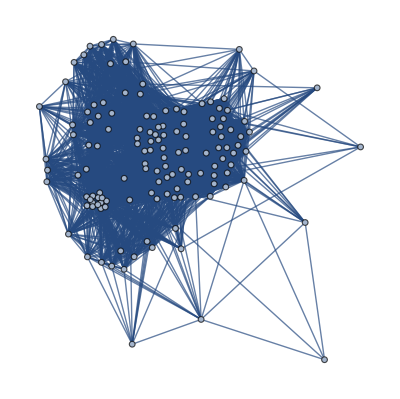

```mathematica
Graph[First /@ chGformulaNetwork,EdgeWeight->1/(Last /@ chGformulaNetwork),
       GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},
       VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

## Dimensional Analysis

## QuantityVariableCanonicalUnit

Identifiers used by QuantityVariablepaclet:ref/QuantityVariable may not be strings:

```mathematica
variables=FormulaData["CylinderMomentOfInertia","QuantityVariables"]
```

{I_∥ MomentOfInertia,m Mass,r Radius,I_⊥ MomentOfInertia,h Height}

```mathematica
QuantityVariableIdentifier[variables[[1]]]
```

I_∥

```mathematica
InputForm[%]
```

Subscript["I", "∥"]

Use the ResourceFunctionpaclet:ref/ResourceFunction "PhysicalQuantityLookup" to find physical quantities and quantity variables from units and quantities:

```mathematica
ResourceFunction["PhysicalQuantityLookup"]["Amperes", "QuantityVariable"]
```

{I ElectricCurrent,{} CriticalCurrent,{} HallCurrent,BatteryCapacityPower,MagnetizationRemanenceThicknessProduct,I ElectricCurrentPhasor,J DisplacementCurrent,ψ MagneticScalarPotential,I_tot TotalCurrent,U_m MagneticTension}

```mathematica
ResourceFunction["PhysicalQuantityLookup"][Quantity[12,"Meter"^3], "Entity"]
```

{critical volume,engine displacement,struck measure,volume,capacity,tonnage,elastic section modulus,volume polarizability,volume of food or beverage,granular potential,plastic section modulus,radar reflectivity factor,section modulus}

## NondimensionalizationTransform

DimensionalCombinationspaclet:ref/DimensionalCombinations derives dimensionless combinations of QuantityVariablepaclet:ref/QuantityVariable objects:

```mathematica
s=QuantityVariable["s","Length"];
s0=QuantityVariable["s0","Length"];
a=QuantityVariable["a","Acceleration"];
t=QuantityVariable["t","Time"];
v=QuantityVariable["v","Speed"];
```

```mathematica
DimensionalCombinations[{s,s0,a,t,v},GeneratedParameters->None]
```

{(s0 Length)/(s Length),(a Acceleration (t Time)^2)/(s Length),(a Acceleration s Length)/(v Speed)^2,(s Length)/(t Time v Speed),(a Acceleration (t Time)^2)/(s0 Length),(a Acceleration s0 Length)/(v Speed)^2,(s0 Length)/(t Time v Speed),(v Speed)/(a Acceleration t Time)}

Compare to the dimensionalization rules for an equation for linear motion:

```mathematica
accelerationSpeedDistance="s" "Length"=="s0" "Length"+1/2 "a" "Acceleration" ("t" "Time")^2+"t" "Time" "v" "Speed";
```

```mathematica
NondimensionalizationTransform[accelerationSpeedDistance, {"a" "Acceleration","t" "Time","s0" "Length"}, {b, u, d0},"DimensionalizationRules"]
```

{b→(a Acceleration s Length)/(v Speed)^2,u→(t Time v Speed)/(s Length),d0→(s0 Length)/(s Length)}